```mathematica
x=Import["C:\\Users\\pc\\Desktop\\150523-Background-200ml+150ml-66hr.txt","Data"][[28;;]][[;;,{1,3}]]
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,1},{10,0},{11,2},{12,4},{13,9},{14,7},{15,4834},{16,15574},{17,18529},{18,17192},{19,13159},{20,8984},{21,6065},{22,4110},{23,3195},{24,2569},{25,2119},{26,1950},{27,1737},{28,1623},{29,1726},{30,1822},{31,1949},{32,1704},{33,1380},{34,1197},8125,{8160,1},{8161,8},{8162,6},{8163,3},{8164,3},{8165,4},{8166,8},{8167,1},{8168,6},{8169,4},{8170,3},{8171,2},{8172,4},{8173,5},{8174,2},{8175,4},{8176,2},{8177,7},{8178,4},{8179,5},{8180,7},{8181,4},{8182,3},{8183,2},{8184,6},{8185,2},{8186,2},{8187,3},{8188,2},{8189,3},{8190,3},{8191,11},{8192,4}}
 |  |  |  |

```mathematica
x=[[6;;]]
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,1},{12,0},{13,4},{14,437},{15,1276},{16,1760},{17,1855},{18,1844},{19,1712},{20,1666},{21,1524},{22,1495},{23,1415},{24,1340},{25,1333},{26,1295},{27,1265},{28,1192},{29,1157},{30,1129},8133,{8164,0},{8165,0},{8166,0},{8167,0},{8168,0},{8169,0},{8170,0},{8171,0},{8172,1},{8173,0},{8174,0},{8175,0},{8176,0},{8177,0},{8178,0},{8179,0},{8180,0},{8181,0},{8182,0},{8183,0},{8184,0},{8185,1},{8186,0},{8187,0},{8188,0},{8189,0},{8190,0},{8191,0},{8192,0}}
 |  |  |  |

```mathematica
y=;
```

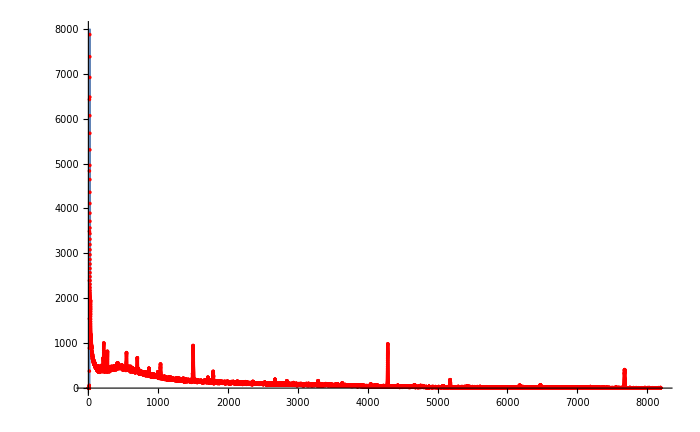

```mathematica
ListPlot[{x},Joined->True,PlotRange->{All,{0,8000}},GridLines->Full,ImageSize->700,Mesh->All,MeshStyle->Red,InterpolationOrder->2]
```

```mathematica
3
```

```mathematica
γ2:=Module[{α,β,γ,γ2},α=(x[[;;,2]]-MeanFilter[x[[;;,2]],5])/.{u_/;u>=0->u^2.,u_/;u<0->0.};
β=(α-MeanFilter[x[[;;,2]],5])/.{u_/;u>=0->0.3u,u_/;u<0->10^-11 u};γ=(β-MeanFilter[x[[;;,2]],5])/.{u_/;u>=0->1.3u,u_/;u<0->10^-15 u};
γ2=(γ-MeanFilter[x[[;;,2]],5])/.{u_/;u>=0->5u,u_/;u<0->10^-10 u}]
```

```mathematica
N@γ2
```

{0.,0.,0.,-1.11111×10^-11,-1.×10^-11,-2.72727×10^-11,-6.36364×10^-11,-1.45455×10^-10,-2.09091×10^-10,-4.41545×10^-8,-1.85736×10^-7,-3.54182×10^-7,-5.10473×10^-7,8166,-4.18182×10^-10,-4.×10^-10,-4.09091×10^-10,-3.63636×10^-10,-3.54545×10^-10,-3.36364×10^-10,-3.72727×10^-10,-3.72727×10^-10,-3.8×10^-10,-4.×10^-10,-3.75×10^-10,41.75,-4.33333×10^-10}
 |  |  |  |

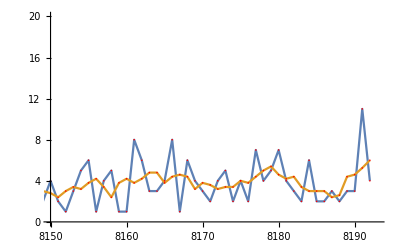

```mathematica
yy=MeanFilter[x[[;;,2]],2];
z=ExponentialMovingAverage[x[[;;,2]],0.01];
ListLinePlot[{x,yy},PlotRange->{{8150,8193},{0,20}},GridLines->Full,ImageSize->Full,Mesh->All,MeshStyle->Red,InterpolationOrder->1.5]
```

```mathematica
Length[x]
```

8192

```mathematica
β1=N@FindPeaks[γ2,1]/.{{_,u_}/;u<0->Nothing,{_,v_}/;v<10->Nothing,{v_,_}/;v<32->Nothing}
```

{{138.,4207.36},{157.,4541.65},{186.,5073.48},{196.,361.739},{214.,29776.3},{221.,234071.},{249.,109822.},{257.,13854.3},{272.,143954.},{411.,3189.26},{422.,1689.29},{546.,103535.},{577.,418.394},{603.,1635.3},{701.,69024.4},{866.,10116.3},{993.,8347.83},{1033.,71046.9},{1499.,139612.},{1711.,4518.21},{1788.,27829.9},{1859.,260.051},{1874.,142.754},{2134.,100.65},{2355.,628.367},{2672.,3755.95},{2830.,40.45},{2842.,1632.5},{2858.,167.583},{2905.,63.0905},{2937.,74.8463},{3152.,89.9905},{3289.,3298.45},{3324.,85.3996},{3335.,411.096},{3399.,213.38},{4044.,1381.57},{4131.,47.6033},{4287.,383977.},{4430.,198.537},{4661.,221.712},{4742.,38.7025},{4757.,428.339},{4786.,230.796},{5079.,106.25},{5092.,31.7938},{5179.,10253.8},{5296.,149.775},{5423.,327.198},{5457.,43.1996},{5526.,81.6343},{5608.,69.2211},{6381.,97.7488},{6409.,52.0665},{6471.,464.15},{6557.,11.4843},{6625.,108.534},{6672.,46.6888},{7001.,34.5996},{7382.,165.56},{7544.,56.4223},{7677.,27652.8},{7753.,71.},{7842.,23.2145},{7966.,37.0802},{8191.,41.75}}

```mathematica
First[Cases[x[[(#-2);;If[(#+2)>Length[x],#,#+2]]],{_,Max[x[[(#-2);;If[(#+2)>Length[x],#,#+2]]][[;;,2]]]}]]&/@β1[[;;,1]]
```

{{138,491},{157,476},{186,503},{196,459},{214,674},{221,969},{249,802},{257,572},{272,817},{411,553},{422,561},{546,778},{577,489},{603,484},{701,660},{866,437},{993,361},{1033,536},{1499,940},{1711,241},{1788,362},{1859,163},{1874,157},{2134,153},{2355,149},{2672,196},{2830,121},{2842,161},{2858,110},{2905,105},{2937,120},{3152,103},{3289,163},{3324,99},{3335,95},{3399,99},{4044,93},{4131,72},{4287,986},{4430,62},{4661,64},{4742,40},{4757,57},{4786,53},{5079,51},{5092,33},{5179,187},{5296,36},{5423,50},{5457,33},{5526,31},{5608,35},{6381,24},{6409,27},{6471,73},{6557,24},{6625,29},{6672,29},{7001,23},{7382,17},{7544,14},{7677,406},{7753,12},{7842,9},{7966,10},{8191,11}}

```mathematica
β2=Module[{β1,β2},
β1=N@FindPeaks[γ2,1]/.{{_,u_}/;u<0->Nothing,{_,v_}/;v<10->Nothing,{v_,_}/;v<32->Nothing};
β2=First[Cases[x[[(#-2);;If[(#+2)>Length[x],#,#+2]]],{_,Max[x[[(#-2);;If[(#+2)>Length[x],#,#+2]]][[;;,2]]]}]]&/@β1[[;;,1]];
β2=DeleteDuplicates[β2]/.{_,u_}/;u<=30->Nothing;
β2=Table[If[Negative[Subtract@@Nearest[β2[[;;,1]],u[[1]],2]],If[Abs[Subtract@@Nearest[β2[[;;,1]],u[[1]],2]]<=3,Nothing,u],u],{u,β2}]]
```

{{138,491},{157,476},{186,503},{196,459},{214,674},{221,969},{249,802},{257,572},{272,817},{411,553},{422,561},{546,778},{577,489},{603,484},{701,660},{866,437},{993,361},{1033,536},{1499,940},{1711,241},{1788,362},{1859,163},{1874,157},{2134,153},{2355,149},{2672,196},{2830,121},{2842,161},{2858,110},{2905,105},{2937,120},{3152,103},{3289,163},{3324,99},{3335,95},{3399,99},{4044,93},{4131,72},{4287,986},{4430,62},{4661,64},{4742,40},{4757,57},{4786,53},{5079,51},{5092,33},{5179,187},{5296,36},{5423,50},{5457,33},{5526,31},{5608,35},{6471,73},{7677,406}}

```mathematica
β2
```

{}

```mathematica
{{175,4843},{220,1156},{227,1617},{248,444},{257,795},{264,488},{547,1274},{600,358},{657,318},{710,1676},{761,313},{807,265},{867,3160},{1033,5348},{1143,168},{1377,127},{1410,125},{1430,129},{1567,91},{1703,86},{1788,3583},{1827,56},{1941,2383},{1952,137},{2027,41},{2112,53},{2255,320},{2306,91},{2334,39},{2365,102},{2462,64},{2624,41},{2741,163},{3288,628},{3326,35},{3391,87},{3633,226},{3759,68},{4043,182},{4066,40},{4114,62},{4133,92},{4430,79},{4648,40},{4876,34},{5077,95},{5180,434},{5424,60},{6470,89},{6473,91},{7187,37}}//Length
```

51

```mathematica
β2//Length
```

50

```mathematica
Abs[Subtract@@Nearest[β2[[;;,1]],6470,2]]<=3
```

True

{{175,4843},{220,1156},{227,1617},{248,444},{257,795},{264,488},{547,1274},{600,358},{657,318},{710,1676},{761,313},{807,265},{867,3160},{1033,5348},{1143,168},{1377,127},{1410,125},{1430,129},{1567,91},{1703,86},{1788,3583},{1827,56},{1941,2383},{1952,137},{2027,41},{2112,53},{2255,320},{2306,91},{2334,39},{2365,102},{2462,64},{2624,41},{2741,163},{3288,628},{3326,35},{3391,87},{3633,226},{3759,68},{4043,182},{4066,40},{4114,62},{4133,92},{4430,79},{4648,40},{4876,34},{5077,95},{5180,434},{5424,60},{6473,91},{7187,37}}

```mathematica
ROI2[ch_]:=Module[{j=ch,
t,
i,
k,l,v},
{ v={x[[j]]};
i=0;
k=1;
While[i<10,If[x[[j-i]][[2]]>=x[[j-i-1]][[2]],v=AppendTo[v,x[[j-i-1]]],If[(x[[j-i-1]][[2]]>=x[[j-i-2]][[2]])&&k<=2,v=AppendTo[v,x[[j-i-1]]];k++;True,Break[]]];i++];v,

v={x[[j]]};
i=0;
k=1;
While[i<10,If[x[[j+i]][[2]]>=x[[j+i+1]][[2]],v=AppendTo[v,x[[j+i+1]]],If[(x[[j+i+1]][[2]]>=x[[j+i+2]][[2]])&&k<=2,v=AppendTo[v,x[[j+i+1]]];k++;True,Break[]]];i++];v}]
```

```mathematica
pol[ch_]:=If[Length[mroi[ch]]==0,Polygon[{{Roi[ch][[1]],0},{Roi[ch][[2]],0},x[[Roi[ch][[2]]]],x[[Roi[ch][[1]]]]}],Polygon[{{mRoi[ch][[1]],0},{mRoi[ch][[2]],0},x[[mRoi[ch][[2]]]],x[[mRoi[ch][[1]]]]}]]
 lin[ch_]:=Line[{{Flatten[Ω2[545]][[1,2]],f[ω,ch]/.Flatten[Ω2[ch]][[1]]},{Flatten[Ω2[545]][[2,2]],f[ω,ch]/.Flatten[Ω2[ch]][[1]]}}]
blin[ch_,t_]:=If[MemberQ[(x[[Roi[ch][[2]]]]-x[[Roi[ch][[1]]]]),0],Last[x[[Roi[ch][[1]]]]],(t-First[x[[Roi[ch][[1]]]]])/(Divide@@(x[[Roi[ch][[2]]]]-x[[Roi[ch][[1]]]])) +Last[x[[Roi[ch][[1]]]]]]
```

```mathematica
mroi[ch_]:=Cases[ROI2[ch][[2,;;]],{_,u_}/;u<=Min[ROI2[ch][[1,;;,2]]]]
mRoi[ch_]:={Min[ROI2[ch][[1,;;,1]]],If[Length[mroi[ch]]!=0,First[Last[mroi[ch]]],Max[ROI2[ch][[2,;;,1]]]]}
Roi[ch_]:={Min[ROI2[ch][[1,;;,1]]],Max[ROI2[ch][[2,;;,1]]]}
cor1Roi[ch_]:={Min[cor1ROI[ch][[1,;;,1]]],Max[cor1ROI[ch][[2,;;,1]]]}
NPA[ch_]:=Total[x[[Roi[ch][[1]];;Roi[ch][[2]]]][[;;,2]]-Table[blin[ch,N@i],{i,Range@@Roi[ch]}]]
```

```mathematica
model[u_]:=a1 (Exp[-(b1(u-x1))^2])
f2[u_,ch_]:=model[u]/.FindFit[x[[Roi[ch][[1]];;Roi[ch][[2]]]],model[uu],{{a1,x[[ch]][[2]]},{b1,1},{x1,ch}},uu]
Ω1[ch_]:=First/@{ROI2[ch][[1]]/.{_,u_}/;!MemberQ[Flatten[Nearest[#,(x[[ch]][[2]])/2]&/@ROI2[ch][[;;,;;,2]]],u]->Nothing,ROI2[ch][[2]]/.{_,u_}/;!MemberQ[Flatten[Nearest[#,(x[[ch]][[2]])/2]&/@ROI2[ch][[;;,;;,2]]],u]->Nothing}
Ω11[ch_]:=First/@{ROI2[ch][[1]]/.{_,u_}/;!MemberQ[Flatten[Nearest[#,(x[[ch]][[2]])/2]&/@ROI2[ch][[;;,;;,2]]],u]->Nothing,ROI2[ch][[2]]/.{_,u_}/;!MemberQ[Flatten[Nearest[#,(x[[ch]][[2]])/2]&/@ROI2[ch][[;;,;;,2]]],u]->Nothing}
```

```mathematica
Ω2[ch_]:=FindRoot[f2[ω,ch]==f2[ch,ch]/2.,{ω,#}]&/@{ch-4,ch+4}  
Ω22[ch_]:=FindRoot[f2[ω,ch]==f2[ch,ch]/2.,{ω,#}]&/@Ω1[ch][[;;,1]]  
Fwhm[ch_]:=If[Abs[Subtract@@Roi[ch]]<=3,0,If[Chop[Abs[Subtract@@Ω22[ch][[;;,1,2]]]]==0,Abs[Subtract@@Ω2[ch][[;;,1,2]]],Abs[Subtract@@Ω22[ch][[;;,1,2]]]]]
Fwhm2[ch_]:=Abs[Subtract@@Ω22[ch][[;;,1,2]]]
Fwhm3[ch_]:=If[Abs[Subtract@@Roi[ch]]<=3,0(*"--the-Point-is-3-or-less"*),If[Chop[Abs[Subtract@@Ω2[ch][[;;,1,2]]]]==0 ||Length[Ω22[ch][[;;,1,2]]]==1,Abs[Subtract@@Ω2[ch][[;;,1,2]]],Abs[Subtract@@Ω22[ch][[;;,1,2]]]]]
```

```mathematica
fw=.
```

```mathematica
PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];
fw=Fwhm3[#]&/@β2[[;;,1]]/.u_/;u<0.01->Style["Erorr",Medium,Underlined,Purple]
fw
```

{3.40456,14.7546,4.48198,14.4533,7.5121,10.1973,8.69627,Erorr,8.51947,4.63476,27.7794,48.7486,Erorr,Erorr,Erorr,Erorr,8.77298,22.6688,16.0919,21.8354,4.31585,Erorr,Erorr,7.14635,Erorr,15.1732,5.51186,9.0541,12.594,10.2983,11.7554,20.7396,6.11852,5.52403,12.9242,8.41531,6.24278,8.57629,6.26235,10.2993,8.39314,7.55101,8.14247,8.32475,7.94111,6.54162,6.17045,6.21983,7.72435,7.17989}

{3.40456,14.7546,4.48198,14.4533,7.5121,10.1973,8.69627,Erorr,8.51947,4.63476,27.7794,48.7486,Erorr,Erorr,Erorr,Erorr,8.77298,22.6688,16.0919,21.8354,4.31585,Erorr,Erorr,7.14635,Erorr,15.1732,5.51186,9.0541,12.594,10.2983,11.7554,20.7396,6.11852,5.52403,12.9242,8.41531,6.24278,8.57629,6.26235,10.2993,8.39314,7.55101,8.14247,8.32475,7.94111,6.54162,6.17045,6.21983,7.72435,7.17989}

```mathematica
Dynamic[t]
```

```mathematica
$Pre=EchoTiming
```

EchoTiming

```mathematica
?$Pre
```

```mathematica
Block[{$ProgressReporting=True},fw]
```

{3.40456,14.7546,4.48198,14.4533,7.5121,10.1973,8.69627,Erorr,8.51947,4.63476,27.7794,48.7486,Erorr,Erorr,Erorr,Erorr,8.77298,22.6688,16.0919,21.8354,4.31585,Erorr,Erorr,7.14635,Erorr,15.1732,5.51186,9.0541,12.594,10.2983,11.7554,20.7396,6.11852,5.52403,12.9242,8.41531,6.24278,8.57629,6.26235,10.2993,8.39314,7.55101,8.14247,8.32475,7.94111,6.54162,6.17045,6.21983,7.72435,7.17989}

```mathematica
PrimePi[10^17+1,ProgressReporting->True]
```

```mathematica
Monitor[
tf=AbsoluteTiming[fw];
t=First[tf],t]
```

2.94403

```mathematica
fun[]:=(LeafCount[])
```

```mathematica
ProgressIndicator[Dynamic[t]]
```

```mathematica
SessionSubmit[fw]
```

TaskObject[<|TaskUUID -> a1312d5f-d920-4e7a-9cee-76d83d7a3faa, TaskEnvironment -> Session, TaskType -> Asynchronous, <<3>>, HandlerFunctionsKeys -> {Task, TaskUUID, TaskType, TaskStatus, TaskEnvironment, HandlerFunctions, HandlerFunctionsKeys, EventName, EvaluationExpression, <<4>>, R<<14>>nt, NextScheduledTime, TotalRunCount, MessageOutput, PrintOutput}, AutoRemove -> True|>]

```mathematica
First[%34]
```

2.55374

```mathematica
fchanll[t_]:=0.026698054890743093+0.34063989839856623 t;
fchtoene[u_]:=(u-0.026698054890743093)/0.34063989839856623;
q:={fchanll/@β2[[;;,1]],NPA/@β2[[;;,1]]}//Transpose
q
```

{{59.6387,15276.},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.},{204.411,291.5},{223.827,126.},{241.881,5430.},{259.254,768.},{274.923,156.5},{295.361,12083.},{351.908,20294.},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5},{622.376,53.5},{661.209,10502.5},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.},{795.08,91.},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5},{1133.,79},{1155.14,445.},{1237.57,1231.5},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5},{1847.66,323.5},{2204.99,674.},{2448.21,235}}

```mathematica
na[#]&/@Range[1,100,3]
```

{3,1,1,2,1,1,1,1,1,1,3,1,1,1,1,2,3,2,2,1,1,1,1,1,1,1,2,7,3,1,1,2,2,2}

```mathematica
Aa[f_]:=Cases[y[[1,;;,{f,f+1}]],{_?NumericQ,_?NumberQ}];
na[f_]:=Module[{naa},
naa=ReplaceAll[PeakDetect[Aa[f][[;;,2]],0,0,(1-1./GoldenRatio)^1.3*Max[Aa[f][[;;,2]]]]*Aa[f],{0.,0.}->Nothing];If[Length[naa]==0,1,Length[naa]]]
df[e_]:=(1.38+0.045 √e);
T[f_,n_,g_]:=Module[{w,mx,t,j,m,c,na},(
w=Cases[y[[1,;;,{f,f+1}]],{_?NumericQ,_?NumberQ}];
na=ReplaceAll[PeakDetect[w[[;;,2]],0,0,5]*w,{0.,0.}->Nothing];
If[n>Length[w],m=Length[w],m=n];
mx=TakeLargest[w[[;;,2]],m];
t=Cases[w,{_,v_/;MemberQ[mx,v]}];
c=Nearest[t[[;;,1]],g];
j=Norm[g-c];
If[Between[j,Flatten[{0,df[c]//First}]],True,False])]
G[f_,g_]:=Module[{α},
α=Nearest[(Select[y[[1,;;,f]],NumericQ]),g];If[Between[Norm[g-α],Flatten[{0,df[α]//First}]],True,False]]
```

```mathematica
na[4]
```

1

```mathematica
y[[1,;;,1]]
```

```mathematica
na=ReplaceAll[PeakDetect[a[[;;,2]],0,0,5]*a,{0.,0.}->Nothing]
```

```mathematica
Cases[y[[1,;;,{1,2}]],{_?NumericQ,_?NumberQ}];
```

```mathematica
G[4,59.63]
```

True

```mathematica
τ={};
ppa;
Do[{
Do[
If[(G[i,g[[1]]]&&(T[i,5,g[[1]]])),g=Append[g,y[[1,1,i]]]];If[!MemberQ[τ,g],τ=Append[τ,g]],{i,1,Length[y[[1,1,;;-3]]],3}]},{g,q}]
```

```mathematica
τ
```

{{59.6387,15276.},{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.},{186.357,3433.,U-235},{186.357,3433.,U-235,Ra-226},{204.411,291.5},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.},{241.881,5430.,Pb-214},{259.254,768.},{259.254,768.,Pa-234m},{274.923,156.5},{274.923,156.5,Cs-136},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.},{295.361,12083.,Pb-214},{295.361,12083.,Pb-214,Au-194},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{768.17,1513.,Zn-65},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.},{785.542,441.,Pb-214},{785.542,441.,Pb-214,Pa-234m},{795.08,91.},{795.08,91.,Cs-134},{805.64,459.5},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
Part
```

```mathematica
ττ={};
Do[
Do[If[SubsetQ[τ[[1+i]],τ[[i]]],ττ=τ/.τ[[i]]->Nothing],{i,Length[τ]-1}];
Do[If[SubsetQ[ττ[[1+i]],ττ[[i]]],τ=ττ/.ττ[[i]]->Nothing],{i,Length[ττ]-1}];
Do[If[SubsetQ[τ[[1+i]],τ[[i]]],ττ=τ/.τ[[i]]->Nothing],{i,Length[τ]-1}];,3]
```

```mathematica
.
```

```mathematica
ττ
```

{{59.6387,15276.},{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.},{186.357,3433.,U-235},{186.357,3433.,U-235,Ra-226},{204.411,291.5},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.},{241.881,5430.,Pb-214},{259.254,768.},{259.254,768.,Pa-234m},{274.923,156.5},{274.923,156.5,Cs-136},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.},{295.361,12083.,Pb-214},{295.361,12083.,Pb-214,Au-194},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{768.17,1513.,Zn-65},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.,Pb-214,Pa-234m},{795.08,91.,Cs-134},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
ττ
```

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.,U-235},{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.,Pb-214},{259.254,768.,Pa-234m},{274.923,156.5,Cs-136},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.,Pb-214},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.,Zn-65},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.,Pb-214,Pa-234m},{795.08,91.,Cs-134},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
τ
```

{{59.6387,15276.},{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.},{186.357,3433.,U-235},{186.357,3433.,U-235,Ra-226},{204.411,291.5},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.},{241.881,5430.,Pb-214},{259.254,768.},{259.254,768.,Pa-234m},{274.923,156.5},{274.923,156.5,Cs-136},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.},{295.361,12083.,Pb-214},{295.361,12083.,Pb-214,Au-194},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{768.17,1513.,Zn-65},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.},{785.542,441.,Pb-214},{785.542,441.,Pb-214,Pa-234m},{795.08,91.},{795.08,91.,Cs-134},{805.64,459.5},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
ContainsAny[τ,τ[[1]]]
```

False

```mathematica
Complement[τ,τ[[1]]]
```

{{59.6387,15276.},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.},{204.411,291.5},{223.827,126.},{241.881,5430.},{259.254,768.},{274.923,156.5},{295.361,12083.},{351.908,20294.},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{622.376,53.5},{661.209,10502.5},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.},{795.08,91.},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1133.,79},{1155.14,445.},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1847.66,323.5},{2448.21,235},{59.6387,15276.,Am-241},{87.5712,1844.,Cd-109},{186.357,3433.,U-235},{204.411,291.5,U-235},{241.881,5430.,Pb-214},{259.254,768.,Pa-234m},{274.923,156.5,Cs-136},{295.361,12083.,Pb-214},{351.908,20294.,Pb-214},{609.091,15844.5,Bi-214},{661.209,10502.5,Cs-137},{768.17,1513.,Zn-65},{785.542,441.,Pb-214},{795.08,91.,Cs-134},{805.64,459.5,Ag-99},{1120.05,3495.5,Bi-214},{1237.57,1231.5,Bi-214},{1385.07,226.5,Y-88},{1764.54,2687.5,Bi-214},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{186.357,3433.,U-235,Ra-226},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.,Pb-214,Au-194},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.,Pb-214,Pa-234m},{1237.57,1231.5,Bi-214,Cs-136},{295.361,12083.,Pb-214,Au-194,Xe-139}}

```mathematica
SubsetQ[]
```

```mathematica
τ/.τ[[1]]->Nothing
```

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.},{186.357,3433.,U-235},{186.357,3433.,U-235,Ra-226},{204.411,291.5},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.},{241.881,5430.,Pb-214},{259.254,768.},{259.254,768.,Pa-234m},{274.923,156.5},{274.923,156.5,Cs-136},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.},{295.361,12083.,Pb-214},{295.361,12083.,Pb-214,Au-194},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{768.17,1513.,Zn-65},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.},{785.542,441.,Pb-214},{785.542,441.,Pb-214,Pa-234m},{795.08,91.},{795.08,91.,Cs-134},{805.64,459.5},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
Select[τ,MemberQ[#,τ[[1]]]&]
```

{}

```mathematica
GatherBy[τ,{#,_}=={#_,___}&]
```

```mathematica
τ[[;;,1]]
```

{59.6387,59.6387,74.9675,77.352,84.5054,87.5712,87.5712,89.9556,186.357,186.357,186.357,204.411,204.411,223.827,241.881,241.881,259.254,259.254,274.923,274.923,274.923,295.361,295.361,295.361,295.361,351.908,351.908,389.378,469.088,480.329,487.142,533.809,580.136,609.091,622.376,661.209,661.209,664.956,690.504,719.458,768.17,768.17,768.17,785.542,785.542,785.542,795.08,795.08,805.64,805.64,838.682,893.866,933.721,1120.05,1133.,1155.14,1237.57,1237.57,1280.49,1377.23,1385.07,1385.07,1401.42,1407.89,1509.06,1583.32,1660.99,1729.46,1764.54,1847.66,1847.66,2204.99,2448.21}

```mathematica
Gather[τ[[;;,1]]]{}
```

{{59.6387,59.6387},{74.9675},{77.352},{84.5054},{87.5712,87.5712},{89.9556},{186.357,186.357,186.357},{204.411,204.411},{223.827},{241.881,241.881},{259.254,259.254},{274.923,274.923,274.923},{295.361,295.361,295.361,295.361},{351.908,351.908},{389.378},{469.088},{480.329},{487.142},{533.809},{580.136},{609.091},{622.376},{661.209,661.209},{664.956},{690.504},{719.458},{768.17,768.17,768.17},{785.542,785.542,785.542},{795.08,795.08},{805.64,805.64},{838.682},{893.866},{933.721},{1120.05},{1133.},{1155.14},{1237.57,1237.57},{1280.49},{1377.23},{1385.07,1385.07},{1401.42},{1407.89},{1509.06},{1583.32},{1660.99},{1729.46},{1764.54},{1847.66,1847.66},{2204.99},{2448.21}}

```mathematica
Partition
```

```mathematica
Commonest[%38]
```

{Pb-214}

```mathematica
na=.
```

```mathematica
na[13]
```

1

```mathematica
PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];
H=Module[{H=q(*/.{{_,g_}/;g<0 ->Nothing};*)},
Do[H=H/.{{g_,gg___}/;(G[i,g]&&(T[i,5,g]))->{g,gg,y[[1,1,i]]}},{i,1,Length[y[[1,1,;;-3]]],3}];
H]
```

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair Am-241 and 2505..

General::stop: Further output of Nearest::neard will be suppressed during this calculation.

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.,Pb-214},{259.254,768.,Pa-234m},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.,Pb-214,Pa-234m},{795.08,91.,Cs-134},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
H
```

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair Am-241 and 2505..

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair Am-241 and 2158.57.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair Am-241 and 1550.95.

General::stop: Further output of Nearest::neard will be suppressed during this calculation.

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.,Pb-214},{259.254,768.,Pa-234m},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.,Pb-214,Pa-234m},{795.08,91.,Cs-134},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
{{59.63868027463983,15276.000000000004,"Am-241"},{74.96747570257531,2018.},{77.35195499136528,3357.},{84.50539285773517,401.5},{87.57115194332226,1844.,"Cd-109"},{89.95563123211222,678.},{186.35672247890648,3433.,"U-235"},{204.41063709403048,291.5,"U-235"},{223.82711130274876,126.},{241.88102591787276,5430.,"Pb-214"},{259.25366073619966,768.,"Pa-234m"},{274.9230960625337,156.5,"Cs-136"},{295.36148996644766,12083.,"Pb-214"},{351.90771310060967,20294.,"Pb-214"},{389.3781019244519,177.},{469.08783814971645,224.},{480.32895479686914,182.},{487.1417527648405,234.},{533.809418845444,257.5},{580.1364450276491,61.5},{609.0908363915272,15844.5,"Bi-214"},{622.3757924290712,53.5},{661.2087408465078,10502.5,"Cs-137"},{664.955779728892,466.},{690.5037721087845,16.5},{719.4581634726626,238.},{768.1696689436576,1513.,"Zn-65"},{785.5423037619845,441.,"Pb-214"},{795.0802209171443,91.,"Cs-134"},{805.6400577674999,459.5,"Ag-99"},{838.6821279121608,237.},{893.8657914527286,41.},{933.7206595653607,791.5},{1120.0506839893765,3495.5,"Bi-214"},{1132.995000128522,79},{1155.1365935244287,445.},{1237.5714489368818,1231.5,"Bi-214"},{1280.4920761351011,403.},{1377.2338072802938,962.5},{1385.068524943461,226.5,"Y-88"},{1401.419240066592,210.},{1407.891398136165,552.5},{1509.061447960539,404.},{1583.3209458114266,190.5},{1660.9868426462995,225},{1729.4554622244113,626},{1764.5413717594638,2687.5,"Bi-214"},{1847.657506968714,323.5,"Bi-203"},{2204.98876038881,674.,"Bi-214"},{2448.2056478453865,235}}
```

```mathematica
p=.
```

```mathematica
Aa[1]
```

{{3269.7,0.0001},{3233.2,0.0001},{3183.6,0.0013},{3160.6,0.0003},{3149.,0.0001},{3142.6,0.0012},{3094.,0.0004},{3081.7,0.0048},{3053.9,0.021},{3000.,0.0088},{2978.9,0.0138},{2934.6,0.0005},{2928.6,0.0011},{2921.9,0.014},{2893.5,0.006},{2880.3,0.0092},{2861.1,0.0004},{2827.,0.0023},{2785.9,0.0055},{2769.9,0.025},{2719.3,0.0018},{2699.4,0.0028},{2694.7,0.031},{2662.4,0.0003},{2630.9,0.0008},{2604.5,0.0004},{2564.,0.0001},{2562.,0.0002},{2553.,0.0001},{2550.7,0.0005},{2505.4,0.0057},{2482.8,0.0015},{2447.86,1.57},{2444.7,0.008},{2423.27,0.0046},{2405.1,0.0004},{2390.8,0.0016},{2376.9,0.0088},{2369.,0.0027},{2361.,0.0017},{2353.5,0.0004},{2348.,0.0001},{2331.3,0.0221},{2325.,0.0017},{2319.3,0.0004},{2312.4,0.009},{2310.2,0.0014},{2293.4,0.305},{2287.65,0.0046},{2284.3,0.0051},{2270.9,0.0013},{2266.51,0.018},{2260.3,0.0087},{2251.6,0.0055},{2204.21,5.08},{2192.58,0.034},{2176.5,0.0032},{2160.4,0.0018},{2147.9,0.014},{2120.,0.007},{2118.55,1.14},{2109.92,0.088},{2089.7,0.05},{2085.1,0.0091},{2052.94,0.069},{2021.6,0.02},{2010.78,0.047},{1994.6,0.005},{1935.5,0.041},{1898.7,0.057},{1895.92,0.16},{1890.3,0.08},{1873.16,0.219},{1847.42,2.11},{1838.36,0.36},{1819.2,0.0014},{1813.73,0.011},{1764.49,15.4},{1751.4,0.0009},{1729.6,2.92},{1711.,0.0018},{1683.99,0.216},{1665.8,0.0083},{1661.28,1.15},{1657.,0.046},{1637.,0.006},{1636.3,0.012},{1599.31,0.23},{1598.,0.006},{1595.,0.005},{1594.73,0.25},{1583.22,0.69},{1543.32,0.2},{1538.5,0.376},{1515.5,0.0069},{1509.23,2.11},{1479.15,0.051},{1470.9,0.0092},{1419.7,0.0051},{1407.98,2.15},{1401.5,1.27},{1392.5,0.019},{1385.31,0.757},{1377.67,4.},{1341.49,0.022},{1330.,0.011},{1316.96,0.08},{1303.76,0.112},{1285.1,0.017},{1284.,0.011},{1280.96,1.43},{1279.,0.012},{1238.11,5.79},{1230.6,0.015},{1226.7,0.018},{1207.68,0.451},{1172.98,0.051},{1167.3,0.012},{1156.,0.007},{1155.6,0.016},{1155.19,1.63},{1133.66,0.248},{1130.29,0.04},{1120.29,15.1},{1118.9,0.04},{1104.79,0.077},{1103.64,0.1},{1069.96,0.275},{1067.2,0.027},{1051.96,0.315},{1045.6,0.026},{1038.,0.0083},{1033.3,0.024},{1032.37,0.078},{1021.,0.014},{1013.8,0.0083},{991.49,0.01},{989.34,0.01},{976.18,0.019},{965.,0.01},{964.08,0.362},{961.61,0.012},{952.2,0.006},{949.8,0.0055},{943.34,0.017},{939.6,0.018},{938.65,0.013},{934.5,0.01},{934.1,0.05},{934.06,3.03},{930.2,0.033},{917.8,0.005},{915.74,0.026},{904.29,0.085},{878.03,0.012},{873.07,0.018},{847.16,0.026},{840.4,0.009},{832.39,0.028},{826.3,0.11},{821.18,0.158},{815.,0.038},{806.17,1.22},{788.6,0.015},{786.1,0.31},{769.7,0.03},{768.36,4.94},{752.84,0.13},{740.73,0.04},{733.8,0.043},{722.98,0.035},{719.86,0.379},{710.67,0.075},{708.8,0.017},{704.9,0.047},{703.11,0.472},{699.82,0.016},{697.9,0.051},{693.3,0.006},{687.6,0.0069},{683.22,0.081},{677.41,0.006},{665.45,1.46},{661.1,0.047},{658.7,0.015},{651.5,0.002},{649.18,0.06},{639.67,0.03},{634.72,0.0065},{633.14,0.055},{630.79,0.018},{626.4,0.005},{617.,0.034},{615.73,0.06},{609.31,46.1},{600.,0.008},{595.23,0.017},{572.76,0.074},{547.6,0.004},{543.,0.084},{536.77,0.068},{528.,0.004},{524.6,0.017},{519.9,0.016},{501.96,0.018},{496.9,0.0069},{494.2,0.012},{487.95,0.028},{486.7,0.006},{485.92,0.022},{474.41,0.11},{469.76,0.129},{461.,0.053},{454.77,0.3},{452.92,0.031},{439.34,0.012},{428.,0.0023},{405.74,0.17},{396.01,0.029},{394.05,0.0148},{388.88,0.37},{386.77,0.31},{375.59,0.0046},{363.47,0.0078},{356.,0.007},{351.9,0.07},{348.92,0.12},{334.78,0.034},{333.31,0.08},{304.2,0.042},{280.95,0.06},{273.8,0.15},{268.8,0.02},{252.8,0.003},{230.,0.004},{221.,0.003}}

```mathematica
w[2]==Aa[2]
```

True

```mathematica
PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];
mx[f_,nn_]:=TakeLargest[Aa[f][[;;,2]],If[nn>Length[Aa[f]],Length[Aa[f]],nn]];
t[f_]:=Cases[Aa[f],{_,v_/;MemberQ[mx[f,3 (*na[f]*)],v]}];
eFil[n_]:=Module[{p1,p2,p,int,mxx,m},
p1=Position[y[[1,1,;;]],n];
p2 =Position[H,n];
p[{r_,c__}]:=H[[r]];
int[{f_}]:=TakeLargest[t[f][[;;,2]],1];
mxx[{f_}]:=TakeLargest[t[f][[;;,1]],1];
m=p/@p2;
Table[If[Between[Norm[i-(mxx@@p1)],Flatten[{0,df[i]}]],True,False],{i,m[[;;,1]]}]]
```

```mathematica
p1[n_]:=Position[y[[1,1,;;]],n]
p2[n_]:=Position[H,n]
p[{r_,c__}]:=H[[r]]
int[{f_}]:=TakeLargest[t[f][[;;,1]],na[f]];
mxx[{f_}]:=TakeLargest[t[f][[;;,1]],1];
m[n_]:=p/@p2[n]
(*e[n_]:=Table[If[Between[Norm[i-(mxx@@p1[n])],Flatten[{0,df[i]}]],True,False],{i,m[n][[;;,1]]}]*)
eeFil[n_]:= Table[If[Length[Select[Apply[t,Flatten@p1[n]][[;;,1]],(Norm[#1-i]<=df[i])&]]==0,False,True],{i,m[n][[;;,1]]}]
```

```mathematica
ee[n_]:= Table[If[Length[Select[Apply[t,Flatten@p1[n]][[;;,1]],(Norm[#1-i]<=df[i])&]]==0,False,True],{i,m[n][[;;,1]]}]
```

```mathematica
ee["Cs-137"]
```

{True}

```mathematica
eFil["Bi-214"]
```

{False,False,True}

```mathematica
na[15]
```

1

```mathematica
p1["Am-241"]
```

{{4}}

```mathematica
Nearest[int[{1}],]
```

```mathematica
int[{4}]
```

```mathematica
Apply[t,Flatten@p1["Am-241"]][[;;,1]]
```

{59.54}

```mathematica
Flatten@p1["Xe-139"]
```

{97}

```mathematica
t@@p1["Am-241"]
```

Part::pkspec1: The expression {{4},{5}} cannot be used as a part specification.

{}

```mathematica
?Aa
```

```mathematica
t[1][[;;,1]]
```

{1764.49,1120.29,609.31}

```mathematica
m["Bi-214"]
```

{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1764.54,2687.5,Bi-214}}

```mathematica
m["Bi-214"][[;;,1]]
```

{609.091,1120.05,1764.54}

```mathematica
Select[t[1][[;;,1]],(Norm[#1-609.1]<=1)&]
```

{609.31}

```mathematica
Table[If[Length[Select[t[1][[;;,1]],(Norm[#1-i]<=df[i])&]]==0,False,True],{i,m["Bi-214"][[;;,1]]}]
```

{True,True,True}

```mathematica
TakeLargest[t[1][[;;,1]],1]
```

{1764.49}

```mathematica
na[1]
```

3

```mathematica
mxx[{4}]
```

{59.54}

```mathematica
p1["Am-241"]
```

{{4}}

```mathematica
na[1]
```

3

```mathematica
e["Bi-214"]
```

{False,False,False}

```mathematica
t[1]
```

{{1764.49,15.4},{1120.29,15.1},{609.31,46.1}}

```mathematica
k0=Cases[H,{_,_,__..?StringQ}];
s=Cases[H,{_,_,__?StringQ}];
k1=Union[Flatten[s[[;;,3;;]]]];
k11=k1;
iff=Table[If[Not[Or@@eFil[k11[[i]]]],k11[[i]]->Nothing],{i,Length[k11]}]/.Null->Nothing;
o=Table[If[Or@@eFil[k11[[i]]],m[k11[[i]]],Nothing],{i,Length[k11]}];
o=o/.iff
```

{{{59.6387,15276.,Am-241}},{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1237.57,1231.5,Bi-214},{1764.54,2687.5,Bi-214},{2204.99,674.,Bi-214}},{{795.08,91.,Cs-134}},{{661.209,10502.5,Cs-137}},{{241.881,5430.,Pb-214},{295.361,12083.,Pb-214,Xe-139},{351.908,20294.,Pb-214},{785.542,441.,Pb-214}},{{186.357,3433.,U-235},{204.411,291.5,U-235}},{{295.361,12083.,Pb-214,Xe-139}}}

```mathematica
Res
```

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.,Pb-214},{259.254,768.},{274.923,156.5},{295.361,12083.,Pb-214},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.,Pb-214},{795.08,91.},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
iff
```

{Ag-99→Nothing,Au-194→Nothing,Ba-133→Nothing,Bi-203→Nothing,Cd-109→Nothing,Cs-134→Nothing,Cs-136→Nothing,Pa-234m→Nothing,Xe-139→Nothing,Y-88→Nothing,Zn-65→Nothing}

```mathematica
Table[If[Or@@eFil[k11[[i]]],m[k11[[i]]],Nothing],{i,Length[k11]}]
```

{{{59.6387,15276.,Am-241}},{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1237.57,1231.5,Bi-214,Cs-136},{1764.54,2687.5,Bi-214},{2204.99,674.,Bi-214}},{{661.209,10502.5,Cs-137}},{{241.881,5430.,Pb-214},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.,Pb-214},{785.542,441.,Pb-214,Pa-234m}},{{186.357,3433.,U-235,Ra-226}},{{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235}}}

```mathematica
k11
```

{Ag-99,Am-241,Au-194,Ba-133,Bi-203,Bi-214,Cd-109,Cs-134,Cs-136,Cs-137,Pa-234m,Pb-214,Ra-226,U-235,Xe-139,Y-88,Zn-65}

```mathematica
m["Pb-214"]/.iff
```

{{241.881,5430.,Pb-214},{295.361,12083.,Pb-214},{351.908,20294.,Pb-214}}

```mathematica
C
```

```mathematica
eFil["Pb-214"]
```

{False,False,True}

```mathematica
m["Bi-214"]
```

{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1764.54,2687.5,Bi-214}}

```mathematica
a=Cases[y[[1,;;,{1,1+1}]],{_?NumericQ,_?NumberQ}]
```

```mathematica
Range[Max[Floor/@a[[;;,1]]]]/.u_/;MemberQ[Floor/@a[[;;,1]],u]->{}
```

```mathematica
a/.{u_,v_}->{α-u,v};
```

```mathematica
a[[1,1]]
```

9598.62

```mathematica
u-a[[;;,1]];
```

```mathematica
fD=Apply[DiracDelta,(u-Floor/@a[[;;,1]])];
```

```mathematica
a
```

{{9598.62,0.0001},{9491.47,0.0001},{9345.86,0.0013},{9278.34,0.0003},{9244.29,0.0001},{9225.5,0.0012},{9082.83,0.0004},{9046.72,0.0048},{8965.11,0.021},{8806.88,0.0088},{8744.93,0.0138},{8614.88,0.0005},{8597.27,0.0011},{8577.6,0.014},{8494.23,0.006},{8455.48,0.0092},{8399.11,0.0004},{8299.01,0.0023},{8178.35,0.0055},{8131.38,0.025},{7982.84,0.0018},{7924.42,0.0028},{7910.62,0.031},{7815.8,0.0003},{7723.33,0.0008},{7645.83,0.0004},{7526.93,0.0001},{7521.06,0.0002},{7494.64,0.0001},{7487.89,0.0005},{7354.9,0.0057},{7288.56,0.0015},{7185.99,1.57},{7176.71,0.008},{7113.8,0.0046},{7060.46,0.0004},{7018.48,0.0016},{6977.67,0.0088},{6954.48,0.0027},{6930.99,0.0017},{6908.98,0.0004},{6892.83,0.0001},{6843.81,0.0221},{6825.31,0.0017},{6808.58,0.0004},{6788.32,0.009},{6781.86,0.0014},{6732.54,0.305},{6715.66,0.0046},{6705.83,0.0051},{6666.49,0.0013},{6653.6,0.018},{6635.37,0.0087},{6609.83,0.0055},{6470.71,5.08},{6436.57,0.034},{6389.37,0.0032},{6342.1,0.0018},{6305.41,0.014},{6223.5,0.007},{6219.25,1.14},{6193.91,0.088},{6134.55,0.05},{6121.05,0.0091},{6026.64,0.069},{5934.63,0.02},{5902.87,0.047},{5855.37,0.005},{5681.87,0.041},{5573.84,0.057},{5565.68,0.16},{5549.18,0.08},{5498.87,0.219},{5423.3,2.11},{5396.71,0.36},{5340.46,0.0014},{5324.4,0.011},{5179.85,15.4},{5141.42,0.0009},{5077.42,2.92},{5022.82,0.0018},{4943.53,0.216},{4890.13,0.0083},{4876.86,1.15},{4864.3,0.046},{4805.58,0.006},{4803.53,0.012},{4694.94,0.23},{4691.09,0.006},{4682.29,0.005},{4681.49,0.25},{4647.7,0.69},{4530.57,0.2},{4516.42,0.376},{4448.9,0.0069},{4430.49,2.11},{4342.19,0.051},{4317.97,0.0092},{4167.67,0.0051},{4133.26,2.15},{4114.24,1.27},{4087.82,0.019},{4066.71,0.757},{4044.28,4.},{3938.07,0.022},{3904.34,0.011},{3866.06,0.08},{3827.31,0.112},{3772.53,0.017},{3769.3,0.011},{3760.37,1.43},{3754.62,0.012},{3634.58,5.79},{3612.53,0.015},{3601.09,0.018},{3545.25,0.451},{3443.38,0.051},{3426.71,0.012},{3393.53,0.007},{3392.36,0.016},{3391.16,1.63},{3327.95,0.248},{3318.06,0.04},{3288.7,15.1},{3284.62,0.04},{3243.2,0.077},{3239.82,0.1},{3140.95,0.275},{3132.85,0.027},{3088.11,0.315},{3069.44,0.026},{3047.13,0.0083},{3033.33,0.024},{3030.6,0.078},{2997.22,0.014},{2976.09,0.0083},{2910.59,0.01},{2904.28,0.01},{2865.65,0.019},{2832.83,0.01},{2830.12,0.362},{2822.87,0.012},{2795.25,0.006},{2788.2,0.0055},{2769.24,0.017},{2758.26,0.018},{2755.47,0.013},{2743.29,0.01},{2742.11,0.05},{2742.,3.03},{2730.66,0.033},{2694.26,0.005},{2688.22,0.026},{2654.6,0.085},{2577.51,0.012},{2562.95,0.018},{2486.89,0.026},{2467.04,0.009},{2443.53,0.028},{2425.65,0.11},{2410.62,0.158},{2392.48,0.038},{2366.56,1.22},{2314.98,0.015},{2307.64,0.31},{2259.49,0.03},{2255.56,4.94},{2210.,0.13},{2174.45,0.04},{2154.1,0.043},{2122.34,0.035},{2113.18,0.379},{2086.2,0.075},{2080.71,0.017},{2069.26,0.047},{2064.01,0.472},{2054.35,0.016},{2048.71,0.051},{2035.21,0.006},{2018.48,0.0069},{2005.62,0.081},{1988.56,0.006},{1953.45,1.46},{1940.68,0.047},{1933.64,0.015},{1912.5,0.002},{1905.69,0.06},{1877.77,0.03},{1863.24,0.0065},{1858.6,0.055},{1851.7,0.018},{1838.81,0.005},{1811.22,0.034},{1807.49,0.06},{1788.64,46.1},{1761.31,0.008},{1747.31,0.017},{1681.35,0.074},{1607.48,0.004},{1593.98,0.084},{1575.69,0.068},{1549.95,0.004},{1539.96,0.017},{1526.17,0.016},{1473.5,0.018},{1458.65,0.0069},{1450.72,0.012},{1432.37,0.028},{1428.7,0.006},{1426.41,0.022},{1392.62,0.11},{1378.97,0.129},{1353.26,0.053},{1334.97,0.3},{1329.54,0.031},{1289.67,0.012},{1256.38,0.0023},{1191.03,0.17},{1162.47,0.029},{1156.72,0.0148},{1141.54,0.37},{1135.34,0.31},{1102.52,0.0046},{1066.94,0.0078},{1045.01,0.007},{1032.98,0.07},{1024.23,0.12},{982.719,0.034},{978.404,0.08},{892.947,0.042},{824.693,0.06},{803.703,0.15},{789.025,0.02},{742.054,0.003},{675.121,0.004},{648.701,0.003}}

```mathematica
Floor/@a[[;;,1]]
```

```mathematica
If[MemberQ[Floor/@a[[;;,1]],9598],1,0]
```

1

```mathematica
Take
```

```mathematica
Cases[a,{v_/;Between[Abs[9598-v],{0,1}],_}]
```

{{9598.62,0.0001}}

```mathematica
Table[If[MemberQ[Floor/@a[[;;,1]],u],First[Cases[a,{v_/;Between[Abs[u-v],{0,1}],_}]],{u,0}],{u,Max[a[[;;,1]]]}]
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},9576,{9588,0},{9589,0},{9590,0},{9591,0},{9592,0},{9593,0},{9594,0},{9595,0},{9596,0},{9597,0},{9598.62,0.0001}}
 |  |  |  |

```mathematica
a:=Cases[y[[1,;;,{4,4+1}]],{_?NumericQ,_?NumberQ}];
```

```mathematica
a;
```

```mathematica
(PeakDetect[a[[;;,2]],0,0,5]*a)/.{0.,0.}->Nothing
```

{{2204.21,5.08},{1764.49,15.4},{1238.11,5.79},{1120.29,15.1},{609.31,46.1}}

```mathematica
na=.
```

```mathematica
a[f_]:=Cases[y[[1,;;,{f,f+1}]],{_?NumericQ,_?NumberQ}];
na[f_]:=(ReplaceAll[PeakDetect[a[f][[;;,2]],0,0,(1-1./GoldenRatio)^□*Max[a[f][[;;,2]]]]*a[f],{0.,0.}->Nothing];
If[Length[na[f]]==0,1,Length[na[f]]])
```

```mathematica
na[1]
```

3

```mathematica
na[#]&/@Range[1,100,3]
```

{3,1,1,2,1,1,1,1,1,1,4,1,2,1,1,3,6,2,2,1,1,1,1,1,1,1,2,9,3,2,3,2,3,2}

```mathematica
na[97]
```

3

```mathematica
{5,1,1,6,0,1,0,1,1,1,3,0,4,0,1,3,3,4,2,1,1,0,1,1,0,1,0,8,5,3,3,3,4,2}
```

```mathematica
(1-1./GoldenRatio)^2*Max[Cases[y[[1,;;,{97,97+1}]],{_?NumericQ,_?NumberQ}][[;;,2]]]
```

8.17029

```mathematica
(1-1./GoldenRatio)^2
```

0.145898

```mathematica
p["Xe-139"]
```

p[Xe-139]

```mathematica
y[[1,;;,{97,98}]]
```

{{Xe-139,},{,},{Gamma Emissions:,},{,},{    Energy  ,   Intensity },{     (keV)  ,      (%)    },{,},{3504.7,0.067},{3424.8,0.073},{3375.51,0.151},{3214.8,0.039},{3168.7,0.062},{3156.3,0.045},{3146.6,0.062},{3130.6,0.08},{3110.8,0.039},{3028.6,0.067},{2989.4,0.073},{2941.8,0.078},{2936.2,0.056},{2918.3,0.123},{2911.7,0.067},{2903.8,0.078},{2886.6,0.084},{2872.65,0.123},{2854.2,0.09},{2832.8,0.062},{2815.03,0.224},{2790.89,0.269},{2769.32,0.297},{2761.6,0.067},{2754.2,0.067},{2736.7,0.118},{2693.4,0.078},{2673.4,0.056},{2640.1,0.034},{2633.75,0.106},{2613.7,0.034},{2578.9,0.062},{2574.04,0.34},{2535.,0.062},{2510.41,0.27},{2507.6,0.078},{2464.6,0.112},{2451.6,0.045},{2437.8,0.095},{2430.3,0.039},{2423.6,0.045},{2403.75,0.263},{2366.97,0.134},{2328.8,0.63},{2304.97,0.29},{2291.61,0.4},{2255.3,0.09},{2249.7,0.067},{2238.4,0.146},{2227.28,0.37},{2204.6,0.045},{2192.32,0.34},{2116.88,0.319},{2110.12,0.34},{2103.7,0.056},{2099.48,0.157},{2085.91,0.627},{2063.9,0.392},{2039.1,0.078},{2025.1,0.056},{2021.8,0.101},{2015.11,0.174},{2007.6,0.112},{2006.8,0.112},{1994.2,0.084},{1979.57,0.521},{1967.3,0.123},{1939.5,0.095},{1935.1,0.112},{1911.7,0.118},{1911.42,0.118},{1895.98,0.599},{1862.4,0.297},{1862.4,0.073},{1857.6,0.112},{1854.5,0.13},{1853.3,0.19},{1852.3,0.095},{1851.8,0.095},{1830.2,0.078},{1830.2,0.034},{1818.5,0.151},{1817.6,0.151},{1814.1,0.123},{1804.1,0.112},{1803.99,0.112},{1793.,0.062},{1790.85,0.431},{1786.6,0.062},{1776.9,0.185},{1773.84,0.302},{1769.,0.039},{1765.2,0.05},{1765.,0.05},{1722.6,0.106},{1711.44,0.28},{1700.2,0.16},{1681.1,0.19},{1670.33,1.103},{1666.2,0.045},{1665.4,0.045},{1653.6,0.26},{1652.8,0.11},{1641.7,0.157},{1635.2,0.073},{1615.,0.16},{1613.8,0.263},{1612.4,0.15},{1611.6,0.09},{1608.7,0.095},{1584.7,0.12},{1579.5,0.2},{1543.6,0.028},{1540.1,0.062},{1520.17,0.71},{1503.1,0.202},{1490.,0.21},{1481.5,0.067},{1458.98,0.25},{1453.32,0.487},{1448.7,0.14},{1437.7,0.11},{1434.13,0.246},{1428.7,0.185},{1416.94,0.157},{1416.5,0.174},{1404.16,0.129},{1386.19,0.515},{1367.19,0.168},{1362.91,0.314},{1351.6,0.095},{1344.93,1.01},{1324.38,0.207},{1316.4,0.151},{1309.4,0.33},{1309.4,0.09},{1299.8,0.05},{1297.85,0.442},{1291.4,0.17},{1289.47,0.493},{1273.1,0.045},{1267.,0.045},{1259.26,0.549},{1242.88,0.65},{1233.8,0.039},{1228.8,0.078},{1219.33,0.19},{1214.9,0.073},{1206.45,0.19},{1199.43,0.18},{1190.6,0.08},{1178.73,0.34},{1178.73,0.028},{1176.3,0.078},{1171.5,0.146},{1149.2,0.14},{1137.52,0.36},{1129.2,0.078},{1115.,0.17},{1114.8,0.134},{1105.6,0.101},{1099.4,0.062},{1067.56,0.017},{1046.31,0.297},{1036.3,0.123},{1022.,0.039},{1017.7,0.09},{1006.25,0.258},{1001.7,0.062},{996.19,0.297},{986.02,0.302},{980.8,0.123},{980.59,0.123},{970.3,0.084},{967.3,0.067},{960.6,0.056},{957.3,0.067},{946.5,0.06},{942.61,0.08},{937.9,0.067},{926.,0.034},{924.5,0.162},{908.9,0.218},{896.3,0.15},{891.76,0.174},{888.6,0.067},{879.74,0.157},{868.7,0.056},{847.45,0.258},{832.41,0.073},{820.5,0.078},{818.29,0.274},{801.62,0.594},{788.04,3.53},{786.7,0.022},{783.1,0.062},{775.6,0.084},{773.4,0.112},{772.,0.056},{761.04,0.196},{745.16,0.47},{732.42,1.91},{730.4,0.151},{723.84,1.803},{719.8,0.07},{716.96,0.162},{710.4,0.196},{699.6,0.084},{675.79,0.162},{672.39,0.146},{652.28,0.269},{646.5,0.622},{634.2,0.034},{626.89,0.95},{624.3,0.095},{612.82,4.5},{601.84,1.2},{595.43,0.28},{589.8,0.084},{585.6,0.045},{579.4,0.056},{569.64,0.15},{565.4,0.09},{549.02,0.062},{523.9,0.045},{518.8,0.05},{515.44,0.37},{513.88,0.84},{505.07,0.358},{498.2,0.045},{491.47,1.46},{491.47,0.34},{482.6,0.022},{466.8,0.073},{454.46,0.258},{446.8,0.101},{442.7,0.179},{441.3,0.095},{427.7,0.073},{393.5,6.7},{388.6,0.062},{356.72,0.526},{338.86,0.622},{326.8,0.09},{305.,0.039},{296.53,21.7},{289.78,9.2},{225.38,3.02},{218.59,56.},{181.3,0.14},{174.97,11.3},{174.97,8.6},{121.37,0.47},{119.4,0.067},{103.75,0.314},{71.,0.202},{55.7,0.11},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,}}

```mathematica
Range[1,100,3][[28]]
```

82

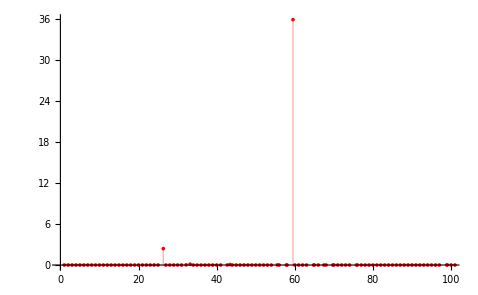

```mathematica
Table[If[MemberQ[Floor/@a[[;;,1]],u],First[Cases[a,{v_/;Between[Abs[u-v],{0,1}],_}]],{u,0}],{u,Max[a[[;;,1]]]}]//ListPlot[#,Filling->Axis,PlotStyle->Red,PlotRange->{{0,100},All}]&
```

```mathematica
Piecewise[{{u,MemberQ[a[[;;,1]],u]}]
```

```mathematica
k11
```

{Ag-99,Am-241,Au-194,Ba-133,Bi-203,Bi-214,Cd-109,Cs-134,Cs-136,Cs-137,Pa-234m,Pb-214,Ra-226,U-235,Xe-139,Y-88,Zn-65}

```mathematica
PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];
o=Module[{k0,s,k11,iff,o},
k0=Cases[H,{_,_,__..?StringQ}];
s=Cases[H,{_,_,__?StringQ}];
k1=Union[Flatten[s[[;;,3;;]]]];
k11=k1;
iff=Table[If[Not[Or@@eFil[k11[[i]]]],k11[[i]]->Nothing],{i,Length[k11]}]/.Null->Nothing;
o=Table[If[Or@@eFil[k11[[i]]],m[k11[[i]]],Nothing],{i,Length[k11]}];
o=o/.iff]
```

{{{59.6387,15276.,Am-241}},{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1237.57,1231.5,Bi-214},{1764.54,2687.5,Bi-214},{2204.99,674.,Bi-214}},{{795.08,91.,Cs-134}},{{661.209,10502.5,Cs-137}},{{241.881,5430.,Pb-214},{295.361,12083.,Pb-214,Xe-139},{351.908,20294.,Pb-214},{785.542,441.,Pb-214}},{{186.357,3433.,U-235},{204.411,291.5,U-235}},{{295.361,12083.,Pb-214,Xe-139}}}

```mathematica
Table[If[Not[Or@@eFil[k11[[i]]]],k11[[i]]->Nothing],{i,Length[k11]}]/.Null->Nothing
```

{Ac-228→Nothing,Ag-99→Nothing,Au-194→Nothing,Bi-203→Nothing,Pa-234m→Nothing}

```mathematica
k1
```

{Ac-228,Ag-99,Am-241,Au-194,Bi-203,Bi-214,Cs-137,Pa-234m,Pb-214,Ra-226,U-235,Xe-139}

```mathematica
iff
```

{Ac-228→Nothing,Ag-99→Nothing,Au-194→Nothing,Bi-203→Nothing,Pa-234m→Nothing,Ra-226→Nothing}

```mathematica
o
```

{{{59.6387,15276.,Am-241}},{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1764.54,2687.5,Bi-214}},{{661.209,10502.5,Cs-137}},{{241.881,5430.,Pb-214},{295.361,12083.,Pb-214,Xe-139},{351.908,20294.,Pb-214}},{{186.357,3433.,U-235,Ra-226}},{{186.357,3433.,U-235,Ra-226}},{{295.361,12083.,Pb-214,Xe-139}}}

```mathematica
o//.{Or->And,eFil->eeFil}
```

{{{59.6387,15276.,Am-241}},{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1764.54,2687.5,Bi-214}},{{661.209,10502.5,Cs-137}},{{241.881,5430.,Pb-214},{295.361,12083.,Pb-214,Xe-139},{351.908,20294.,Pb-214}},{{186.357,3433.,U-235,Ra-226}},{{186.357,3433.,U-235,Ra-226}},{{295.361,12083.,Pb-214,Xe-139}}}

```mathematica
Block[{eFil=eeFil},o]
```

{{{795.08,91.,Ac-228}},{{805.64,459.5,Ag-99}},{{59.6387,15276.,Am-241}},{{295.361,12083.,Pb-214,Au-194,Xe-139}},{{1847.66,323.5,Bi-203}},{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1764.54,2687.5,Bi-214}},{{661.209,10502.5,Cs-137}},{{768.17,1513.,Pa-234m}},{{241.881,5430.,Pb-214},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.,Pb-214}},{{186.357,3433.,U-235,Ra-226}},{{186.357,3433.,U-235,Ra-226}},{{295.361,12083.,Pb-214,Au-194,Xe-139}}}

```mathematica
PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];
Res=(((HH=H /.{u__/;And[StringQ[u],!MemberQ[o,u,3]]->Nothing})/.{u__/;MemberQ[o,u,2]->Framed[u]})/.Map[#->Highlighted[#,Background->RandomColor[RGBColor[RandomReal[],_,_]]]&,k1])
```

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.,U-235},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.,Pb-214},{259.254,768.},{274.923,156.5},{295.361,12083.,Pb-214,Xe-139},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.,Pb-214},{795.08,91.,Cs-134},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
Res
```

$Aborted

```mathematica
H
```

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair Am-241 and 2505..

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair Am-241 and 2158.57.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair Am-241 and 1550.95.

General::stop: Further output of Nearest::neard will be suppressed during this calculation.

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.,Pb-214},{259.254,768.,Pa-234m},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.,Pb-214,Pa-234m},{795.08,91.,Cs-134},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
bb=.
```

```mathematica
PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];
bb:=Module[{bt={},bb,bc,j},
Do[Table[Which[Length[i]==3,bt=Append[bt,{i[[1]],i[[2]]}->i[[3]]],Length[i]>3,j=3;While[j<=Length[i],bt=Append[bt,{i[[1]],i[[2]]}->i[[j]]];j++]],{i,o[[i]]}],{i,Length[o]}];
bb=Union[bt];
bc=Table[bb[[u,1]]=x[[Ceiling[fchtoene[First[bb[[;;,1]][[u]]]]]]],{u,Length[bb[[;;,1]]]}];
bb]
```

```mathematica
bb
```

{{175,4843}→Am-241,{547,1274}→U-235,{600,358}→U-235,{710,1676}→Pb-214,{867,3160}→Pb-214,{867,3160}→Xe-139,{1033,5348}→Pb-214,{1788,3583}→Bi-214,{1941,2383}→Cs-137,{2306,91}→Pb-214,{2334,39}→Cs-134,{3288,628}→Bi-214,{3633,226}→Bi-214,{5180,434}→Bi-214,{6473,91}→Bi-214}

```mathematica
PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];
bsl:=Union[Flatten[Range@@@Roi/@β2[[;;,1]]]];
BeasLine:=x/.{{u_,v_}/;MemberQ[bsl,u]->Nothing,{_,0.}->Nothing};
spectra:=x/.{u_/;MemberQ[BeasLine,u]->Nothing,{_,0.}->Nothing}
```

```mathematica
cor1ROI[ch_]:=Module[{ϵ=1},
While[ϵ<10&&Abs[Subtract@@Roi[ch]]<=3,ROI[ch,{0.8-0.05*ϵ,1.3+0.05*ϵ}];ϵ++];
ROI[ch,{0.8-0.05*ϵ,1.3+0.05*ϵ}]]
cor2ROI[ch_]:=Module[{ϵ=1},
While[ϵ<10&&Abs[Subtract@@Roi[ch]]<=3,ROI[ch,{0.8-0.05*ϵ,1.3+0.05*ϵ}];ϵ++];
ROI[ch,{0.8-0.05*ϵ,1.3+0.05*ϵ}];ϵ]
```

```mathematica
PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];
A[g_]:=Or@@Table[G[i,g]&&T[i,5,g],{i,1,100,3}];
bbb:=Table[If[u=={},"--",(Or@@eFil[#])&/@u],{u,H[[;;,3;;]]}];
bbb
B:=Table[If[A[H[[;;,1]][[ii]]],H[[ii,3;;]],"--"],{ii,Length[H[[;;,1]]]}]
```

{{True},--,--,--,{False},--,{True,False},{True},--,{True},{False},{False,False},{True,False,True},{True},--,--,--,--,--,--,{True},--,{True},--,--,--,{False,False},{True,False},{True},{False},--,--,--,{True},--,--,{True,False},--,--,{False},--,--,--,--,--,--,{True},{False},{True},--}

```mathematica
PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];
spect[c_]:=Module[{ξ,ξ3},
If[MemberQ[bb[[;;,1,1]],β2[[;;,1]][[c]]],
ξ=Position[bb[[;;,1,1]],β2[[;;,1]][[c]]][[1,1]];
ξ3=Position[o,bb[[;;,2]][[ξ]]][[1,1]];Graphics[{Red,Thickness[0.007],Line[{{#,-1},{#,1}}]&/@o[[ξ3,;;,1]]},PlotRange->{{0,8000},{-1,1}},Frame->False,Background->Black,AspectRatio->3/(8GoldenRatio)],Graphics[{Red,Thickness[0.005],Text[Style["..No..Info..",25,Bold,Red]]},Frame->False,Background->Black,AspectRatio->3/(8GoldenRatio)]]]
```

```mathematica
PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];
tabspect=Table[spect[i],{i,Length[β2[[;;,1]]]}];
```

```mathematica
r=;
eff:=Interpolation[r,InterpolationOrder->2];
Activc1:=Module[{τ=24*3600,wight=0.2,ee,Eff},
ee=A/@H[[;;,1]];
Eff:=Table[If[ee[[i]],(H[[;;,2]][[i]])/(eff[H[[;;,1]][[i]]]*τ*wight),"--"] ,{i,Length[ee]}];Eff]
```

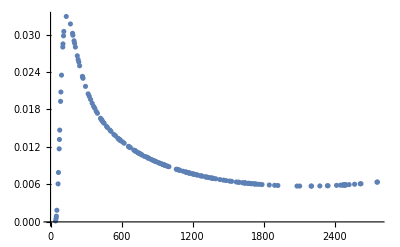

```mathematica
ListPlot[r]
```

```mathematica
r
```

{{42.09,0.000153},{47.01,0.000555},{49.42,0.000917},{53.54,0.00186},{63.66,0.00609},{66.86,0.00791},{73.,0.0117},{75.21,0.0132},{77.6,0.0147},{84.93,0.0193},{87.57,0.0208},{92.69,0.0235},{103.48,0.028},{105.06,0.0285},{109.67,0.0298},{112.28,0.0305},{132.82,0.0329},{168.02,0.0317},{185.98,0.0302},{188.86,0.0299},{198.71,0.029},{203.49,0.0286},{209.73,0.028},{226.11,0.0266},{233.26,0.026},{238.76,0.0256},{245.51,0.025},{269.2,0.0233},{271.46,0.0232},{274.32,0.023},{295.4,0.0217},{318.07,0.0205},{327.57,0.0201},{338.58,0.0196},{351.77,0.019},{363.95,0.0185},{373.78,0.0182},{386.05,0.0177},{396.37,0.0174},{422.34,0.0166},{428.29,0.0164},{430.4,0.0164},{433.81,0.0163},{439.15,0.0161},{447.4,0.0159},{452.84,0.0158},{472.85,0.0153},{481.28,0.0151},{502.21,0.0147},{511.1,0.0145},{535.23,0.014},{548.29,0.0138},{568.74,0.0134},{575.6,0.0133},{578.63,0.0132},{583.22,0.0132},{589.23,0.0131},{591.5,0.013},{609.53,0.0128},{621.96,0.0126},{659.54,0.0121},{661.57,0.012},{665.4,0.012},{674.68,0.0119},{703.84,0.0115},{712.93,0.0114},{716.67,0.0114},{718.52,0.0113},{736.56,0.0111},{745.23,0.011},{751.66,0.011},{754.92,0.0109},{768.16,0.0108},{772.68,0.0107},{792.77,0.0105},{812.02,0.0104},{819.38,0.0103},{825.29,0.0102},{831.11,0.0102},{850.6,0.01},{860.34,0.00991},{870.82,0.00982},{882.47,0.00972},{884.83,0.00971},{893.13,0.00964},{911.08,0.00949},{921.39,0.00941},{927.32,0.00937},{943.06,0.00925},{946.33,0.00922},{949.08,0.0092},{954.11,0.00917},{960.46,0.00912},{965.76,0.00908},{968.92,0.00905},{983.27,0.00895},{990.45,0.00891},{1000.68,0.00884},{1062.7,0.00844},{1068.35,0.0084},{1074.93,0.00836},{1077.84,0.00835},{1088.08,0.00829},{1093.26,0.00826},{1120.3,0.00811},{1140.72,0.00799},{1145.6,0.00797},{1149.09,0.00795},{1165.97,0.00786},{1168.42,0.00785},{1170.99,0.00784},{1179.52,0.00779},{1198.71,0.0077},{1202.62,0.00768},{1213.,0.00763},{1217.49,0.00761},{1236.69,0.00752},{1238.39,0.00752},{1263.51,0.0074},{1274.78,0.00736},{1281.09,0.00733},{1307.75,0.00722},{1316.06,0.00719},{1319.05,0.00718},{1336.04,0.00711},{1346.39,0.00707},{1363.,0.00701},{1366.07,0.007},{1369.4,0.00699},{1377.76,0.00696},{1396.07,0.0069},{1431.29,0.00678},{1461.21,0.00669},{1482.76,0.00662},{1512.85,0.00654},{1530.44,0.00649},{1570.28,0.00639},{1588.99,0.00635},{1593.02,0.00634},{1623.27,0.00627},{1630.43,0.00626},{1642.2,0.00623},{1644.27,0.00623},{1647.75,0.00622},{1668.52,0.00618},{1674.44,0.00617},{1677.15,0.00616},{1690.18,0.00614},{1696.38,0.00613},{1698.2,0.00612},{1720.07,0.00609},{1724.88,0.00608},{1731.26,0.00607},{1746.53,0.00604},{1765.45,0.00602},{1787.24,0.00598},{1848.56,0.00591},{1893.67,0.00586},{1921.05,0.00583},{2082.78,0.00574},{2105.18,0.00574},{2201.82,0.00573},{2205.63,0.00574},{2275.76,0.00576},{2339.43,0.00579},{2345.1,0.00579},{2416.86,0.00585},{2449.76,0.00588},{2467.92,0.0059},{2474.,0.00591},{2479.06,0.00591},{2484.67,0.00592},{2487.65,0.00592},{2489.08,0.00592},{2491.67,0.00593},{2495.04,0.00593},{2523.13,0.00597},{2569.3,0.00603},{2616.81,0.0061},{2623.53,0.00611},{2758.43,0.00637},{2762.68,0.00638}}

```mathematica
RM=Import["C:\\Users\\pc\\Desktop\\RM - Kh-1.xlsx","Data"];
```

```mathematica
RM
```

```mathematica
RM=;
```

```mathematica
Dataset[]
```

```mathematica
ds=Dataset[RM];
```

```mathematica
ds[[3]];
```

```mathematica
RM[[2,5;;,3]]
```

{59.54,88.03,122.1,165.9,279.2,391.7,514.,661.62,898.,1173.24,1332.5,1836.,}

```mathematica
RM[[2,4]]
```

{M.w gm/mole,isotopes,Ennergy,half life (Y),intensity %,flux/gm   (ɤCPS)/gm,reference time,Reference material in the sample (gm),flux  (ɤCPS),measuring date,∆t (Year),flux on measure date  (cps),Bq,Bq/kg,ppm}

```mathematica
Association[
Thread[RM[[3,4;;,2]]->Map[Association,Map[Thread,Map[RM[[3,3]]->#&,RM[[3,4;;]]]]]]]
```

```mathematica
ds150ml=Dataset[Association[Thread[RM[[2,5;;,2]]->Map[Association,Map[Thread,Map[RM[[2,4]]->#&,RM[[2,5;;]]]]]]],DatasetTheme->"Scientific"]
```

```mathematica
ds200ml=Dataset[Association[Thread[RM[[3,4;;,2]]->Map[Association,Map[Thread,Map[RM[[3,3]]->#&,RM[[3,4;;]]]]]]],DatasetTheme->"Scientific"]
```

```mathematica
ds200ml[;;,"half life (Y)"]
```

```mathematica
ds200ml["Am-241","half life (Y)"]
```

431.

```mathematica
ds150ml[All,{9}]
```

```mathematica
ds200ml[All,"flux"]
```

```mathematica
q
```

{{59.6387,15276.},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.},{204.411,291.5},{223.827,126.},{241.881,5430.},{259.254,768.},{274.923,156.5},{295.361,12083.},{351.908,20294.},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5},{622.376,53.5},{661.209,10502.5},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.},{795.08,91.},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5},{1133.,79},{1155.14,445.},{1237.57,1231.5},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5},{1847.66,323.5},{2204.99,674.},{2448.21,235}}

```mathematica
Values[Normal@ds150ml[All,7,Now-#&]]
```

{5479.52 days,5479.52 days,5479.52 days,5479.52 days,5479.52 days,5479.52 days,5479.52 days,5479.52 days,5479.52 days,5479.52 days,5479.52 days,-+Wed 6 Dec 2023 12:30:05GMT+3}

```mathematica
UnitConvert[
Values[Normal@ds150ml[All,7,Now-#&]],"Years"]/Quantity[Values[Normal@ds200ml[All,4]],"Years"]
```

Thread::tdlen: Objects of unequal length in {15.0124,15.0124,15.0124,15.0124,15.0124,15.0124,15.0124,15.0124,15.0124,15.0124,«2»} {0.00232019,0.806322,1.35278,2.65366,7.83595,0.932474,5.6331,0.0332557,3.42475,0.189703,«1»} cannot be combined.

{0.00232019 per year,0.806322 per year,1.35278 per year,2.65366 per year,7.83595 per year,0.932474 per year,5.6331 per year,0.0332557 per year,3.42475 per year,0.189703 per year,0.189703 per year} {15.0124 yr,15.0124 yr,15.0124 yr,15.0124 yr,15.0124 yr,15.0124 yr,15.0124 yr,15.0124 yr,15.0124 yr,15.0124 yr,15.0124 yr,UnitConvert[-+Wed 6 Dec 2023 12:29:44GMT+3,Years]}

```mathematica
UnitConvert[Values[Normal@ds200ml[All,"reference time",Now-#&]],"Years"]
```

{15.0123 yr,15.0123 yr,15.0123 yr,15.0123 yr,15.0123 yr,15.0123 yr,15.0123 yr,15.0123 yr,15.0123 yr,15.0123 yr,15.0123 yr}

```mathematica
15.0123/431
```

0.0348313

```mathematica
HL=(Values[
Normal@ds200ml[All,"flux"]]*
Exp[-Log[2]*

(UnitConvert[
Values[Normal@ds200ml[All,"reference time",Now-#&]],"Years"]/Quantity[Values[Normal@ds200ml[All,"half life (Y)"]],"Years"])
])/.u_->u/Quantity[1,"Seconds"]
```

{1189.52 per second,0.153495 per second,0.000458345 per second,7.42868×10^-10 per second,6.11028×10^-33 per second,0.131201 per second,1.20378×10^-22 per second,1900.71 per second,2.13911×10^-12 per second,502.337 per second,503.081 per second}

```mathematica
Exp[-Log[2]*

(UnitConvert[
Values[Normal@ds200ml[All,"reference time",Now-#&]],"Years"]/Quantity[Values[Normal@ds200ml[All,"half life (Y)"]],"Years"])
]
```

{0.976116,0.000224619,7.56429×10^-7,9.82551×10^-13,3.49008×10^-36,0.0000603412,3.24009×10^-26,0.707164,3.18578×10^-16,0.13855,0.13855}

```mathematica
eFil["Am-241"]
```

{True}

```mathematica
Values[
Normal@ds200ml[All,"flux"]]
```

{1218.68,693.923,621.729,795.21,2032.2,2213.23,4135.52,2689.49,7166.59,3638.79,3644.17}

```mathematica
HL
```

{1189.57 per second,0.155869 per second,0.000470298 per second,7.81346×10^-10 per second,7.09287×10^-33 per second,0.133549 per second,1.33999×10^-22 per second,1901.91 per second,2.28316×10^-12 per second,504.154 per second,504.9 per second}

```mathematica
Res
```

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.,Pb-214},{259.254,768.},{274.923,156.5},{295.361,12083.,Pb-214},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.,Pb-214},{795.08,91.},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
q
```

{{59.6387,15276.},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.},{204.411,291.5},{223.827,126.},{241.881,5430.},{259.254,768.},{274.923,156.5},{295.361,12083.},{351.908,20294.},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5},{622.376,53.5},{661.209,10502.5},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.},{795.08,91.},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5},{1133.,79},{1155.14,445.},{1237.57,1231.5},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5},{1847.66,323.5},{2204.99,674.},{2448.21,235}}

```mathematica
y[[1,;;,1;;3]]//MatrixForm
```

```mathematica
Block[{,y=}]
```

```mathematica
ds200ml[All,{"Ennergy","intensity %"}]
```

```mathematica
y[[1,;;,{1,2}]]
```

```mathematica
Select[y[[1,;;,{1,2}]],NumericQ]
```

{}

```mathematica
q;
```

```mathematica
?G
```

```mathematica
qlib=Block[{x=q,y=lib},Map[If[G[1,#],1,0]&,x[[;;,1]]]]
```

{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
qlib*q/.{_,u_}->{_,u/UnitConvert[Quantity[15,"Minutes"],"Seconds"]}
```

{{_,16.9733 per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,2.04889 per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,11.6694 per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0 per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0 per second},{_,0 per second},{_,0. per second},{_,0. per second},{_,0. per second},{_,0 per second}}

```mathematica
q/.{_,u_}->{_,u/Quantity[15,"Minutes"]}
```

{{_,1018.4 per minute},{_,134.533 per minute},{_,223.8 per minute},{_,26.7667 per minute},{_,122.933 per minute},{_,45.2 per minute},{_,228.867 per minute},{_,19.4333 per minute},{_,8.4 per minute},{_,362. per minute},{_,51.2 per minute},{_,10.4333 per minute},{_,805.533 per minute},{_,1352.93 per minute},{_,11.8 per minute},{_,14.9333 per minute},{_,12.1333 per minute},{_,15.6 per minute},{_,17.1667 per minute},{_,4.1 per minute},{_,1056.3 per minute},{_,3.56667 per minute},{_,700.167 per minute},{_,31.0667 per minute},{_,1.1 per minute},{_,15.8667 per minute},{_,100.867 per minute},{_,29.4 per minute},{_,6.06667 per minute},{_,30.6333 per minute},{_,15.8 per minute},{_,2.73333 per minute},{_,52.7667 per minute},{_,233.033 per minute},{_,79/15 per minute},{_,29.6667 per minute},{_,82.1 per minute},{_,26.8667 per minute},{_,64.1667 per minute},{_,15.1 per minute},{_,14. per minute},{_,36.8333 per minute},{_,26.9333 per minute},{_,12.7 per minute},{_,15 per minute},{_,626/15 per minute},{_,179.167 per minute},{_,21.5667 per minute},{_,44.9333 per minute},{_,47/3 per minute}}

```mathematica
libq=Block[{x=lib[[1]],y={q}},Map[If[G[1,#],First@Cases[y[[1,;;]],{First@Nearest[y[[1,;;,1]],#],_}],{False}]&,x[[;;,1]]]]
```

{{59.6387,15276.},{87.5712,1844.},{False},{False},{False},{False},{False},{661.209,10502.5},{False},{False},{False}}

```mathematica
mlibq=libq/.{v_,u_}:>{v,u/UnitConvert[Quantity[15,"Minutes"],"Seconds"]}
```

{{59.6387,16.9733 per second},{87.5712,2.04889 per second},{False},{False},{False},{False},{False},{661.209,11.6694 per second},{False},{False},{False}}

```mathematica
libqE=Block[{x=lib[[1]],y={q}},Map[If[G[1,#],1,0]&,x[[;;,1]]]]
```

{1,1,0,0,0,0,0,1,0,0,0}

```mathematica
Table[Append[mlibq[[h]],(libqE*HL)[[h]]],{h,Length[libqE*HL]}]
```

{{59.6387,16.9733 per second,1189.52 per second},{87.5712,2.04889 per second,0.153495 per second},{False,0. per second},{False,0. per second},{False,0. per second},{False,0. per second},{False,0. per second},{661.209,11.6694 per second,1900.71 per second},{False,0. per second},{False,0. per second},{False,0. per second}}

```mathematica
ac=Table[Append[mlibq[[h]],(libqE*HL)[[h]]],{h,Length[libqE*HL]}]/.{v_,u_,ω_}:>{v,u,u/ω}
```

{{59.6387,16.9733 per second,0.0142691},{87.5712,2.04889 per second,13.3482},{False,0. per second},{False,0. per second},{False,0. per second},{False,0. per second},{False,0. per second},{661.209,11.6694 per second,0.00613953},{False,0. per second},{False,0. per second},{False,0. per second}}

```mathematica
act=ac/.{{v_,u_,ω_}:>{v,ω},{u_,v_}:>Nothing}
```

{{59.6387,0.0142691},{87.5712,13.3482},{661.209,0.00613953}}

```mathematica
Thread[{β2[[;;,1]],fw}]
```

{{175,3.40456},{220,14.7546},{227,4.48198},{248,14.4533},{257,7.5121},{264,10.1973},{547,8.69627},{600,Erorr},{657,8.51947},{710,4.63476},{761,27.7794},{807,48.7486},{867,Erorr},{1033,Erorr},{1143,Erorr},{1377,Erorr},{1410,8.77298},{1430,22.6688},{1567,16.0919},{1703,21.8354},{1788,4.31585},{1827,Erorr},{1941,Erorr},{1952,7.14635},{2027,Erorr},{2112,15.1732},{2255,5.51186},{2306,9.0541},{2334,12.594},{2365,10.2983},{2462,11.7554},{2624,20.7396},{2741,6.11852},{3288,5.52403},{3326,12.9242},{3391,8.41531},{3633,6.24278},{3759,8.57629},{4043,6.26235},{4066,10.2993},{4114,8.39314},{4133,7.55101},{4430,8.14247},{4648,8.32475},{4876,7.94111},{5077,6.54162},{5180,6.17045},{5424,6.21983},{6473,7.72435},{7187,7.17989}}

```mathematica
fww=Cases[Thread[{β2[[;;,1]],fw}],{_,_?NumericQ}]/.{_,u_}/;u>10->Nothing
```

{{175,3.40456},{227,4.48198},{257,7.5121},{547,8.69627},{657,8.51947},{710,4.63476},{1410,8.77298},{1788,4.31585},{1952,7.14635},{2255,5.51186},{2306,9.0541},{2741,6.11852},{3288,5.52403},{3391,8.41531},{3633,6.24278},{3759,8.57629},{4043,6.26235},{4114,8.39314},{4133,7.55101},{4430,8.14247},{4648,8.32475},{4876,7.94111},{5077,6.54162},{5180,6.17045},{5424,6.21983},{6473,7.72435},{7187,7.17989}}

```mathematica
ListPlot[act,Joined->True,Epilog->{BezierCurve[act],BSplineCurve[act],Green,Line[act],Red,Point[act]},AspectRatio->1/GoldenRatio,PlotStyle->Blue]
```

-Graphics-

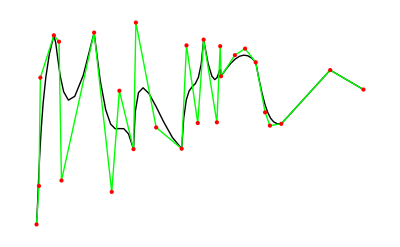

```mathematica
Graphics[{BezierCurve[fww,SplineDegree->30],Green,Line[fww],Red,Point[fww]},AspectRatio->1/GoldenRatio]
```

```mathematica
Line
```

```mathematica
Append[mlibq,libqE*HL]
```

```mathematica
libqE*HL
```

{1189.6 per second,0.157549 per second,0. per second,0. per second,0. per second,0. per second,0. per second,1902.75 per second,0. per second,0. per second,0. per second}

```mathematica
(libqE*HL)/.u_?QuantityQ:>{1,u}
```

{{1,1189.6 per second},{1,0.157549 per second},{1,0. per second},{1,0. per second},{1,0. per second},{1,0. per second},{1,0. per second},{1,1902.75 per second},{1,0. per second},{1,0. per second},{1,0. per second}}

```mathematica
15276/(15*60.)
```

16.9733

```mathematica
q
```

{{59.6387,15276.},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.},{204.411,291.5},{223.827,126.},{241.881,5430.},{259.254,768.},{274.923,156.5},{295.361,12083.},{351.908,20294.},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5},{622.376,53.5},{661.209,10502.5},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.},{795.08,91.},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5},{1133.,79},{1155.14,445.},{1237.57,1231.5},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5},{1847.66,323.5},{2204.99,674.},{2448.21,235}}

```mathematica
NPA[175]
```

15276.

```mathematica
y[[1,;;,1]];
```

```mathematica
lib[[1]][[;;,1]]
```

{59.54,88.03,122.1,165.9,279.2,391.7,514.,661.62,1836.,1173.24,1332.5}

```mathematica
{q}[[1,;;]]
```

{{59.6387,15276.},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.},{204.411,291.5},{223.827,126.},{241.881,5430.},{259.254,768.},{274.923,156.5},{295.361,12083.},{351.908,20294.},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5},{622.376,53.5},{661.209,10502.5},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.},{795.08,91.},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5},{1133.,79},{1155.14,445.},{1237.57,1231.5},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5},{1847.66,323.5},{2204.99,674.},{2448.21,235}}

```mathematica
Select[y⟦1,1;;All,4⟧,NumericQ]
```

{1014.7,955.7,945.7,928.8,921.5,912.4,902.5,898.4,887.3,870.7,862.7,860.7,854.7,851.6,847.4,841.5,835.6,828.5,822.6,819.,812.01,806.3,801.94,794.92,789.17,786.,782.2,780.7,777.2,772.4,770.57,767.,763.9,759.38,755.9,742.9,737.34,731.5,729.72,722.01,722.01,709.45,696.6,696.6,693.62,688.72,680.1,676.03,669.83,666.5,662.4,653.02,641.47,632.93,627.18,619.01,597.48,590.28,590.28,586.59,582.6,573.94,563.05,545.4,529.17,522.06,514.,512.5,487.3,487.3,485.91,468.12,463.22,459.68,454.66,454.66,452.6,446.43,442.81,429.94,426.47,419.33,415.88,406.35,401.,398.64,390.62,389.,383.81,376.65,370.94,368.59,358.25,340.56,337.7,335.38,332.36,322.52,322.52,316.8,309.1,304.21,300.13,292.77,291.3,278.04,275.77,270.63,267.54,264.89,264.89,260.8,260.8,249.,246.73,234.4,232.81,221.8,221.46,208.,204.06,201.7,197.,191.96,190.4,175.07,169.56,165.81,164.61,161.54,159.26,156.4,154.27,150.04,146.55,138.5,136.7,135.3,129.2,128.05,125.3,123.01,120.36,115.5,109.7,106.42,102.98,98.97,96.7,92.1,79.1,78.1,75.8,69.76,67.45,64.83,61.46,59.54,57.85,56.8,55.56,54.,51.01,43.42,42.73,38.54,33.2,32.18,31.4,27.03,26.34,13.81}

```mathematica
lib:={Values[Map[Values,Normal[ds200ml[All,{"Ennergy","intensity %"}]]]]}
```

```mathematica
lib[[1,;;,1]]
```

{59.54,88.03,122.1,165.9,279.2,391.7,514.,661.62,1836.,1173.24,1332.5}

```mathematica
ds200ml[All,{"Ennergy","intensity %"}]
```

```mathematica
Values[Normal@ds200ml[All,"reference time",Now-#&]]
```

{5479.4 days,5479.4 days,5479.4 days,5479.4 days,5479.4 days,5479.4 days,5479.4 days,5479.4 days,5479.4 days,5479.4 days,5479.4 days}

```mathematica
Quantity[Values[Normal@ds200ml[All,"half life (Y)"]],"Years"]//ListPlot
```

{431. yr,1.2402 yr,0.73922 yr,0.376838 yr,0.127617 yr,1.07242 yr,0.177522 yr,30.07 yr,0.291992 yr,5.2714 yr,5.2714 yr}

```mathematica
Values[Normal@ds200ml[All,"reference time",Now-#&]]/Quantity[Values[Normal@ds200ml[All,"half life (Y)"]],"Years"]
```

{0.0348253,12.1026,20.3048,39.8306,117.615,13.9962,84.5512,0.499158,51.4045,2.84738,2.84738,51.4045}

```mathematica
ds200ml[All,"reference time",Now-#&]
```

```mathematica
Normal[%121]
```

<|Am-241→5478.5 days,Cd-109→5478.5 days,Co-57→5478.5 days,cerium - 139→5478.5 days,mercury -203→5478.5 days,Tin -113→5478.5 days,Sr-85→5478.5 days,Cs-137→5478.5 days,Yttrium -88→5478.5 days,Co-60→5478.5 days,Co60→5478.5 days|>

```mathematica
Values[%133]
```

{5478.5 days,5478.5 days,5478.5 days,5478.5 days,5478.5 days,5478.5 days,5478.5 days,5478.5 days,5478.5 days,5478.5 days,5478.5 days}

```mathematica
ds200ml[All,{"half life (Y)","reference time"}]
```

```mathematica
Now-Normal[%79]
```

{5478.47 days,5478.47 days,5478.47 days,5478.47 days,5478.47 days,5478.47 days,5478.47 days,5478.47 days,5478.47 days,5478.47 days,5478.47 days,5478.47 days}

```mathematica
Dataset[%137,DatasetTheme->"Scientific"]
```

```mathematica
Head[""]
```

String

```mathematica
RM[[3]]//TableForm
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  | 200 ml |  |  |  |  |  |  |  |  |  | 
M.w gm/mole | isotopes | Ennergy | half life (Y) | intensity % | flux/gm | reference time | Reference material in the sample (gm) | flux | measuring date | ∆t (Year) | flux on measure date  (cps) | Bq | Bq/kg | ppm | % | 
243.132 | Am-241 | 59.54 | 431. | 0.363 | 1131. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 1218.68 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 1194.12 | 3289.59 | 10275.5 | 8.14239×10^-8 | 8.14239×10^-12 | 
109. | Cd-109 | 88.03 | 1.2402 | 0.05 | 644. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 693.923 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 0.588121 | 11.7624 | 36.7415 | 3.75582×10^-13 | 3.75582×10^-17 | 
57. | Co-57 | 122.1 | 0.73922 | 0.87 | 577. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 621.729 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 0.00436439 | 0.00501654 | 0.0156698 | 4.99278×10^-17 | 4.99278×10^-21 | 8.37544×10^-12
139. | cerium - 139 | 165.9 | 0.376838 | 0.8 | 738. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 795.21 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 6.17771×10^-8 | 7.72214×10^-8 | 2.41211×10^-7 | 9.55426×10^-22 | 9.55426×10^-26 | 100.
203. | mercury -203 | 279.2 | 0.127617 | 0.81 | 1886. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 2032.2 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 2.8533×10^-27 | 3.52259×10^-27 | 1.10033×10^-26 | 2.15554×10^-41 | 2.15554×10^-45 | 
113. | Tin -113 | 391.7 | 1.07242 | 0.64 | 2054. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 2213.23 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 0.620266 | 0.969166 | 3.02732 | 2.77415×10^-14 | 2.77415×10^-18 | 
85. | Sr-85 | 514. | 0.177522 | 0.96 | 3838. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 4135.52 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 1.43246×10^-18 | 1.49214×10^-18 | 4.6609×10^-18 | 5.31828×10^-33 | 5.31828×10^-37 | 
132.981 | Cs-137 | 661.62 | 30.07 | 0.8512 | 2496. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 2689.49 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 2008.98 | 2360.17 | 7372.32 | 2.22923×10^-9 | 2.22923×10^-13 | 
88. | Yttrium -88 | 898. | 0.291992 | 0.937 | 6288. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 6775.45 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 6.07654×10^-10 | 6.4851×10^-10 | 2.02571×10^-9 | 3.93605×10^-24 | 3.93605×10^-28 | 
58.9661 | Co-60 | 1173.24 | 5.2714 | 0.999736 | 3377. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 3638.79 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 689.041 | 689.223 | 2152.88 | 5.06032×10^-11 | 5.06032×10^-15 | 
58.9661 | Co60 | 1332.5 | 5.2714 | 0.999856 | 3382. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 3644.17 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 690.061 | 690.16 | 2155.81 | 5.0672×10^-11 | 5.0672×10^-15 | 
88. | Yttrium -88 | 1836. | 0.291992 | 0.992 | 6651. | Fri 5 Dec 2008 00:00:00GMT+3 | 1.07752 | 7166.59 | Sun 1 Aug 2021 00:00:00GMT+3 | 12.6556 | 6.42733×10^-10 | 6.47917×10^-10 | 2.02385×10^-9 | 3.93245×10^-24 | 3.93245×10^-28 |

```mathematica
RM[[3,4]]
```

{243.132,Am-241,59.54,431.,0.363,1131.,Fri 5 Dec 2008 00:00:00GMT+3,1.07752,1218.68,Sun 1 Aug 2021 00:00:00GMT+3,12.6556,1194.12,3289.59,10275.5,8.14239×10^-8,8.14239×10^-12,}

```mathematica
thf=Now-DateObject[{2008,12,5}]
```

5478. days

```mathematica
.
```

```mathematica
Activc[c_]:=Module[{τ=24*3600,wight=0.2,ξ,ee,ξ2,Acti},
If[MemberQ[bb[[;;,1,1]],β2[[;;,1]][[c]]],
ξ=Position[bb[[;;,1,1]],β2[[;;,1]][[c]]][[1,1]];
ξ2=Position[o,bb[[;;,2]][[ξ]]][[1,1]];
ee=A/@o[[ξ2,;;,1]];
Acti:=Table[If[ee[[i]],(o[[ξ2,;;,2]][[i]])/(eff[o[[ξ2,;;,1]][[i]]]*τ*wight),"--"] ,{i,Length[ee]}];Acti,"--"]]
```

```mathematica
tab1[c_]:=Module[{ξ,ξ3,bbb,fwh,ξ2,Γ1,oo},
If[MemberQ[bb[[;;,1,1]],β2[[;;,1]][[c]]],
ξ=Position[bb[[;;,1,1]],β2[[;;,1]][[c]]][[1,1]];
ξ3=Position[o,bb[[;;,2]][[ξ]]][[1,1]];
bbb=Table[If[u=={},"--",(Or@@eFil[#])&/@u],{u,o[[ξ3,;;,3;;]]}];
fwh=(Position[q,#]&/@o[[ξ3,;;,1]])[[;;,1,1]];
Γ1=Position[o[[ξ3,;;]],q[[;;,1]][[c]]][[1,1]];
oo=Table[If[Γ1==δδ,o[[ξ3,Γ1]]/.Thread[o[[ξ3,Γ1]]->Map[Style[#,15,Red]&,o[[ξ3,Γ1]]]],o[[ξ3,δδ]]],{δδ,Length[o[[ξ3]]]}];
ξ2=TableForm[{A/@o[[ξ3,;;,1]],oo[[;;,3;;]],ToString/@bbb,ToString/@Activc[c],ToString/@(Ceiling[fchtoene[#]]&/@o[[ξ3,;;,1]]),ToString/@(fw[[fwh]]),ToString/@(Roi/@(Ceiling[fchtoene[#]]&/@o[[ξ3,;;,1]]))}//Thread,TableHeadings->{o[[ξ3,;;,1]]/.Thread[o[[ξ3,Γ1]]->Map[Style[#,15,Red]&,o[[ξ3,Γ1]]]],{"G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}}],"--NO-INFORMATION--"]]
```

```mathematica
PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];
tab11=Table[tab1[i],{i,Length[β2[[;;,1]]]}];
tab11[[34]]
```

| G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI
609.091 | True | Bi-214 | {True} | Activc[34] | 1788 | 4.31585 | {1778, 1798}
1120.05 | True | Bi-214 | {True} | Activc[34] | 3288 | 5.52403 | {3278, 3296}
1237.57 | True | Bi-214 | {True} | Activc[34] | 3633 | 6.24278 | {3627, 3643}
1764.54 | True | Bi-214 | {True} | Activc[34] | 5180 | 6.17045 | {5170, 5190}
2204.99 | True | Bi-214 | {True} | Activc[34] | 6473 | 7.72435 | {6463, 6482}

```mathematica
tab1[7]
```

| G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI
186.357 | True | U-235
Ra-226 | {True, True} | 6.58721 | 547 | 8.69627 | {538, 553}

```mathematica
tab11[[7]]
```

| G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI
186.357 | True | U-235 | {True} | 6.58721 | 547 | 8.69627 | {538, 553}
204.411 | True | U-235 | {True} | 0.591549 | 600 | Erorr | {593, 607}

```mathematica
β2[[;;,1]][[21]]
```

1788

```mathematica
MemberQ[bb[[;;,1,1]],β2[[;;,1]][[2]]]
```

False

```mathematica
MemberQ[o[[2]][[Γ1]],q[[21,1]],1]
```

True

```mathematica
bb[[;;,1]]
```

{{175,4843},{547,1274},{547,1274},{600,358},{710,1676},{867,3160},{1033,5348},{1788,3583},{1941,2383},{2306,91},{3288,628},{3633,226},{5180,434},{6473,91}}

```mathematica
q[[34]]
```

{1120.05,3495.5}

```mathematica
o[[2,;;,3;;]]
```

{{Bi-214},{Bi-214},{Bi-214},{Bi-214},{Bi-214}}

```mathematica
o[[2,;;,1]]/.Thread[o[[2,Γ1]]->Map[Style[#,15,Red]&,o[[2,Γ1]]]]
```

{609.091,1120.05,1237.57,1764.54,2204.99}

```mathematica
q
```

{{59.6387,15276.},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.},{204.411,291.5},{223.827,126.},{241.881,5430.},{259.254,768.},{274.923,156.5},{295.361,12083.},{351.908,20294.},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5},{622.376,53.5},{661.209,10502.5},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.},{795.08,91.},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5},{1133.,79},{1155.14,445.},{1237.57,1231.5},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5},{1847.66,323.5},{2204.99,674.},{2448.21,235}}

```mathematica
cc=8;
ξ=Position[bb[[;;,1,1]],β2[[;;,1]][[cc]]][[1,1]]
f=Position[o,bb[[;;,2]][[ξ]]][[1,1]]
Γ1=Position[o[[f,;;]],q[[;;,1]][[cc]]][[1,1]]
oo=Table[If[u==Γ1,o[[f,Γ1]]/.Thread[o[[f,Γ1]]->Map[Style[#,15,Red]&,o[[f,Γ1]]]],o[[f,u]]],{u,Length[o[[f]]]}]
```

4

5

Part::partw: Part 1 of {} does not exist.

{}⟦1,1⟧

{If[1=={}⟦1,1⟧,o⟦f,Γ1⟧/.Thread[o⟦f,Γ1⟧→(Style[#1,15,Red]&)/@o⟦f,Γ1⟧],o⟦f,u⟧]}

```mathematica
o
```

{{{59.6387,15276.,Am-241}},{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1237.57,1231.5,Bi-214},{1764.54,2687.5,Bi-214},{2204.99,674.,Bi-214}},{{661.209,10502.5,Cs-137}},{{241.881,5430.,Pb-214},{295.361,12083.,Pb-214},{351.908,20294.,Pb-214},{785.542,441.,Pb-214}},{{186.357,3433.,U-235,Ra-226}},{{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235}}}

```mathematica
ξ
```

4

```mathematica
Position[o,bb[[;;,2]][[ξ]]]
```

{{5,1,3},{6,1,3},{6,2,3}}

```mathematica
bb
```

{{175,4843}→Am-241,{547,1274}→Ra-226,{547,1274}→U-235,{600,358}→U-235,{710,1676}→Pb-214,{867,3160}→Pb-214,{1033,5348}→Pb-214,{1788,3583}→Bi-214,{1941,2383}→Cs-137,{2306,91}→Pb-214,{3288,628}→Bi-214,{3633,226}→Bi-214,{5180,434}→Bi-214,{6473,91}→Bi-214}

```mathematica
β2[[;;,1]][[8]]
```

600

```mathematica
fchanll[β2[[;;,1]][[8]]]
```

204.411

```mathematica
o[[4]]
```

{{241.881,5430.,Pb-214},{295.361,12083.,Pb-214},{351.908,20294.,Pb-214},{785.542,441.,Pb-214}}

```mathematica
f
```

```mathematica
Position[o,bb[[;;,2]][[ξ]]][[1,1]]
```

1

```mathematica
o[[1,;;]]
```

{{59.6387,15276.,Am-241}}

```mathematica
oo[[;;,3;;]]
```

{{Bi-214},{Bi-214},{Bi-214},{Bi-214},{Bi-214}}

```mathematica
o[[2,2]]
```

{1120.05,3495.5,Bi-214}

```mathematica
H[[21]]
```

{609.091,15844.5,Bi-214}

```mathematica
cc=7;
f=5;
Γ1=Position[o[[f,;;]],q[[;;,1]][[cc]]][[1,1]]
o[[f,;;]][[Γ1,3;;]]
o[[f,;;]]/.Thread[o[[f,;;]][[Γ1,3;;]]->Map[Style[#,15,Red]&,o[[f,;;]][[Γ1,3;;]]]]
```

1

{U-235,Ra-226}

{{186.357,3433.,U-235,Ra-226}}

```mathematica
1
```

```mathematica
o[[5]]
```

{{186.357,3433.,U-235,Ra-226}}

```mathematica
q[[7]]
```

{186.357,3433.}

```mathematica
k11
```

{Ag-99,Am-241,Au-194,Ba-133,Bi-203,Bi-214,Cd-109,Cs-134,Cs-136,Cs-137,Pa-234m,Pb-214,Ra-226,U-235,Xe-139,Y-88,Zn-65}

```mathematica
bbb
```

{{True},--,--,--,{False},--,{True,False},{True},--,{True},{False},{False,False},{True,False,True},{True},--,--,--,--,--,--,{True},--,{True},--,--,--,{False,False},{True,False},{True},{False},--,--,--,{True},--,--,{True,False},--,--,{False},--,--,--,--,--,--,{True},{False},{True},--}

```mathematica
c=1;
tab12:=TableForm[Thread[{A/@H[[;;,1]],((ToString/@(B/.{}->"--"))/.{ToString[B[[c]]]->Style[ToString[B[[c]]],18,Bold,Darker[Red]]}),((ToString/@bbb)/.{ToString[bbb[[c]]]->Style[ToString[bbb[[c]]],18,Bold,Darker[Green]]}),ToString/@Activc1,ToString/@β2[[;;,1]],(ToString/@(fw)/.{ToString[fw[[c]]]->Style[ToString[fw[[c]]],18,Bold,Red]}),ToString/@(Roi/@β2[[;;,1]])}],TableHeadings->{H[[;;,1]],{"G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}},TableAlignments->Center]
```

```mathematica
αα1=Table[ListLinePlot[{x[[(-16+Roi[ii][[1]]);;(16+Roi[ii][[2]])]]},Epilog->{ Opacity[0.5],pol[ii],Green},GridLines->Full,ImageSize->700,InterpolationOrder->1,Mesh->Full,MeshStyle->Red,PlotRange->All,AspectRatio->1/(1.5*GoldenRatio),Filling->Axis],{ii,β2[[;;,1]]}];
```

```mathematica
αα2=Table[Plot[{f2[u,ii],f2[ii,ii]/2,blin[ii,u]},{u,-16+Roi[ii][[1]],16+Roi[ii][[2]]},PlotPoints->2,ImageSize->200,PlotRange->{Automatic,All}],{ii,β2[[;;,1]]}];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
αα3=Table[N@DistributionFitTest[x[[Roi[ii][[1]];;Roi[ii][[2]]]][[;;,2]],Automatic,"HypothesisTestData"]["TestDataTable",All],{ii,β2[[;;,1]]}];
```

```mathematica
name[u_]:=Module[{c=u,ξ},
If[MemberQ[bb[[;;,1,1]],β2[[;;,1]][[c]]],ξ=Position[bb[[;;,1,1]],β2[[;;,1]][[c]]][[1,1]];Text[Style[Highlighted[bb[[ξ,2]],Background->RandomColor[RGBColor[RandomReal[],_,_]]],50,Bold,Red]],Text[Style[Highlighted["Knwon",Background->RandomColor[RGBColor[RandomReal[],_,_]]],50,Bold,Black]]]]
```

```mathematica
a11=Show[ListPlot[x,PlotTheme->"Default",GridLines->Full,ImageSize->700,Axes->True,PlotRange->Full,Joined->True,InterpolationOrder->1,Mesh->Full],ListPlot[bb,PlotStyle->Red,PlotRange->All]];
```

```mathematica
DynamicModule[{c=0,min=0,max=10},
{Button["Prevus", c--, Enabled->Dynamic[c>min]], Dynamic[c],Button["+", c++, Enabled->Dynamic[c<max]]}]
```

```mathematica
vv:=Dynamic[ξ]
```

```mathematica
CreateWindow[DialogNotebook[{TextCell["Enter a name: "],InputField[Dynamic[nm],String],DefaultButton[DialogReturn[ret=nm]]}]];
```

```mathematica
CreateDocument[{{TextCell["Center"],CancelButton[]},

DynamicModule[{c=1,min=1,max=Length[β2[[;;,1]]],a1=αα1,a2=αα2,a3=αα3},
Dynamic[{Column[{Button["Prevus", c--, Enabled->Dynamic[c>min]],{ Dynamic[c], "channl="<>ToString[β2[[;;,1]][[c]]],"Energy="<>ToString[fchanll[β2[[;;,1]][[c]]]],"Fwhm="<>ToString[fw[[c]]],"NPA="<>ToString[NPA[β2[[;;,1]][[c]]]]},Button["+", c++, Enabled->Dynamic[c<max]],a1[[c]],tab11[[c]]}],Column[{name[c],a2[[c]],a3[[c]],tabspect[[c]]}]}]]

},WindowSize->{850,530},WindowFrame->"ThinFrame",WindowElements->{"HorizontalScrollBar", "MagnificationPopUp"},DockedCells->Cell["Show Information","DockedCell"],Magnification->0.82,WindowMargins->Automatic]
```

6xrek_shm26FrontEndObject[LinkObject["6xrek_shm", 3, 1]]26Untitled-1

```mathematica
Row[Table[Button["y",ImageSize->{Automatic,70},Alignment->a],{a,{Top,Center,Bottom}}],"xxx"]
```

xxxxxxyyy

```mathematica
Length[β2[[;;,1]]]
```

52

```mathematica
P
```

```mathematica
fchanll/@β2[[;;,1]]
```

{59.6387,74.9675,77.352,84.5054,87.5712,89.9556,186.357,204.411,223.827,241.881,259.254,274.923,295.361,351.908,389.378,469.088,480.329,487.142,533.809,580.136,609.091,622.376,661.209,664.956,690.504,719.458,768.17,785.542,795.08,805.64,838.682,893.866,933.721,1120.05,1133.,1155.14,1237.57,1280.49,1377.23,1385.07,1401.42,1407.89,1509.06,1583.32,1660.99,1729.46,1764.54,1847.66,2204.99,2448.21}

```mathematica
H
```

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.,Pb-214},{259.254,768.,Pa-234m},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.,Pb-214,Pa-234m},{795.08,91.,Cs-134},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
First[p2["U-235"][[1]]]
```

7

```mathematica
?bb
```

```mathematica
m["Bi-214"]
```

{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1237.57,1231.5,Bi-214,Cs-136},{1764.54,2687.5,Bi-214},{2204.99,674.,Bi-214}}

```mathematica
eFil["Bi-214"]/.{True->1,False->0}
```

{0,0,0,1,0}

```mathematica
?p2
```

```mathematica
Dynamic[First[Position[H,ToString["Am-241"]][[1]]]]
```

```mathematica
ns="";
{InputField[Dynamic[ns],String,FieldHint->"Name Elmaint",ImageSize->{60,20}],Dynamic[cs=First[Position[H,ToString[ns]][[1]]]]}
```

{,}

```mathematica
Dynamic[cs]
```

```mathematica
{,{}}
```

{,{}}

```mathematica
nb:=CreateDialog[{DynamicModule[{c=1,min=1,max=Length[β2[[;;,1]]],a1=αα1,a2=αα2,a3=αα3,fff="",nm,ns,qq,xyx={"..."},xxx,xx,xzx},


TabView[{"Show"->Dynamic[Grid[{{Column[{Row[{CancelButton[],Button["PrintPDF",FrontEndTokenExecute["PrintDialog"]],


Button["Find",


Dynamic[If[Or[1<=nm<=max ,NumberQ[nm]],c=nm,CreateDialog[{TextCell["Not-Found"],ChoiceButtons[]}]]]],




InputField[Dynamic[nm],Number,FieldHint->"N.Peak",ImageSize->{60,20}],"n",

InputField[Dynamic[nm],Number,FieldHint->"chnall",ImageSize->{60,20}],"ch",

InputField[Dynamic[nm],Number,FieldHint->"Energy (kev)",ImageSize->{60,20}],"Energy",


Button["Find",Dynamic[If[MemberQ[H,ns,2],c=First[Position[H,ToString[ns]][[1]]],CreateDialog[{TextCell["Not-Found"],ChoiceButtons[]}]]]],

InputField[Dynamic[ns],String,FieldHint->"Name Elmaint",ImageSize->{60,20}],"Name",


FileNameSetter[Dynamic[fff]],InputField[Text[Dynamic[fff]],Enabled->False,Appearance->"Framed"]}],


Button["Prevus", c--, Enabled->Dynamic[c>min],Alignment->Center],{ Dynamic[c], "channl="<>ToString[β2[[;;,1]][[c]]],"Energy="<>ToString[fchanll[β2[[;;,1]][[c]]]],"Fwhm="<>ToString[fw[[c]]],"NPA="<>ToString[NPA[β2[[;;,1]][[c]]]]},Button["+", c++, Enabled->Dynamic[c<max]],a1[[c]],tab11[[c]]}],Column[{name[c],a2[[c]],a3[[c]],tabspect[[c]]}]}}]]


,"Spectrum"->b,"Decy Elemnt"->ccc,



"Generetor"->Row@{Button["Add",xyx=Append[xyx,RandomReal[]]],Dynamic[ListPicker[Dynamic[xx],xyx,ImageSize->450,FieldSize->{60,25},BaseStyle->{"DisplayFormulaNumbered"}]],
Column[{Button["LodeCNF",qq=Flatten[{SystemDialogInput["FileOpen",".CNF"]}];xyx=Join[xyx,qq],Method->"Queued"]
,Button["Analysis",Dynamic[xxx=xx],ImageSize->50],InputField[Style[Text[Dynamic[xxx]],25,Red],Enabled->False,Appearance->"Framed",ImageSize->{350,35}]}],{ColorSetter[Dynamic[xa]]}}



}]
,DynamicUpdating->False]




,Row[{CancelButton[],Button["PrintPDF",FrontEndTokenExecute["PrintDialog"]],FileNameSetter[Dynamic[fff]],InputField[Text[Dynamic[fff]],Enabled->False,Appearance->"Framed"]}]}

,Enabled->True,WindowSize->{940,500},Background->Lighter[Orange,0.97],WindowElements->"VerticalScrollBar"];
```

```mathematica
Button["Show",nb,ImageSize->{300,300}]
```

Show

```mathematica
Timing[RunProcess[{"C:\\Users\\pc\\Desktop\\cnfconv-master\\cnf2txt.exe",#},"StandardOutput"]&/@qq]
```

{0.,C:\Users\pc\Desktop\_\220423-01-200ml.CNF}

```mathematica
InputField["",String,FieldCompletionFunction->(FileNames[FileNameTake[#]<>"*",{DirectoryName[#]}]&)]
```

```mathematica
AbsoluteTiming[(RunProcess[{"C:\\Users\\pc\\Desktop\\cnfconv-master\\cnf2txtall.bat",#1},"StandardOutput"]&)/@dir];
```

```mathematica
Timing[ParallelMap[RunProcess[{"C:\\Users\\ObidahPhysics\\Desktop\\cnfconv-master\\cnf2txtall.bat",#},"StandardOutput"]&,dir]];
```

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
Button["LodeCNF",qq=Flatten[{SystemDialogInput["FileOpen",".CNF"]}];Return[qq],Method->"Queued"];
```

```mathematica
Information[$Canceled]
```

```mathematica
Map[RunProcess[{"C:\\Users\\pc\\Desktop\\cnfconv-master\\cnf2txt.exe",#1},"StandardOutput"]&,qq]
```

{,}

```mathematica
Button["Analy",{qa=Map[RunProcess[{"C:\\Users\\pc\\Desktop\\cnfconv-master\\cnf2txt.exe",#1},"StandardOutput"]&,qq],qb=Import[qa,"Data"],Iconize[qa]},Method->"Queued"];
```

```mathematica
dir=.
```

```mathematica
lodcnf:=Module[{qq,dir},{
qq=Flatten[{SystemDialogInput["FileOpen",".CNF"]}],Map[RunProcess[{"C:\\Users\\alshrafi\\Desktop\\cnfconv-master\\cnf2txt.exe",#1},"StandardOutput"]&,ToString/@qq],Print[qq],dir=Map[FileNames[#,Map[FileNameJoin,Table[ud[[All;;-2]],{ud,Map[FileNameSplit,qq]}]]]&,Map[StringJoin[#,".txt"]&,Map[FileBaseName,qq]]],Print[dir],
imp=Map[Import[#,"Table"]&,Flatten[dir]]};


]
```

```mathematica
lodeCNF[]:=Module[{},
Button["LodeCNF",
lodcnf ,Method->"Queued"]]
```

```mathematica
lodeCNF[]
```

LodeCNF

RunProcess::pnfd: Program C:\Users\alshrafi\Desktop\cnfconv-master\cnf2txt.exe not found.  Check Environment["PATH"].

{C:\Users\pc\Desktop\_\الكفاءة  ml 200\041115(200)-SMR-E.CAL}

{{}}

RunProcess::pnfd: Program C:\Users\alshrafi\Desktop\cnfconv-master\cnf2txt.exe not found.  Check Environment["PATH"].

{C:\Users\pc\Desktop\_\الكفاءة  ml 200\13102022(200)-equaivalen QCY48-200 ml-Am+Cs+Ra.CAL}

{{}}

```mathematica
imp[[1]]
```

{{#},{#,Sample,name:,Am241+Cs137+Ra226},{#,Sample,id:,131022-,Am+Ra+Cs},{#,Sample,type:,sand,MRS8},{#,User,name:,zae},{#,Sample,description:,125,ml,Am241=90,ml,=,200,ml,Ra226=125,ml,=,200,ml,Cs137=125,ml,=,200,ml},{#},{#,Start,time:,2022-10-13,,20:51:46},{#,Real,time,(s):,188.6},{#,Live,time,(s):,180.},{#},8197,{8182,2787.14,0,0},{8183,2787.48,0,0},{8184,2787.82,0,0},{8185,2788.16,1,0.00555556},{8186,2788.51,0,0},{8187,2788.85,0,0},{8188,2789.19,0,0},{8189,2789.53,0,0},{8190,2789.87,0,0},{8191,2790.21,0,0},{8192,2790.55,0,0}}
 |  |  |  |

```mathematica
Cases[imp[[1]],{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}][[;;,{1,3}]]
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,1},{12,0},{13,4},{14,437},{15,1276},{16,1760},{17,1855},{18,1844},{19,1712},{20,1666},{21,1524},{22,1495},{23,1415},{24,1340},{25,1333},{26,1295},{27,1265},{28,1192},{29,1157},{30,1129},{31,1120},{32,1098},{33,1025},{34,1038},{35,956},{36,980},{37,926},8119,{8157,0},{8158,1},{8159,1},{8160,1},{8161,0},{8162,0},{8163,0},{8164,0},{8165,0},{8166,0},{8167,0},{8168,0},{8169,0},{8170,0},{8171,0},{8172,1},{8173,0},{8174,0},{8175,0},{8176,0},{8177,0},{8178,0},{8179,0},{8180,0},{8181,0},{8182,0},{8183,0},{8184,0},{8185,1},{8186,0},{8187,0},{8188,0},{8189,0},{8190,0},{8191,0},{8192,0}}
 |  |  |  |

```mathematica
DynamicModule[{BE=False},Row[{Button["Activ",BE=True],Button["SB",BE=True,Enabled->Dynamic[BE]]}]]
```

```mathematica
Row[Table[DefaultButton[],10]]
```

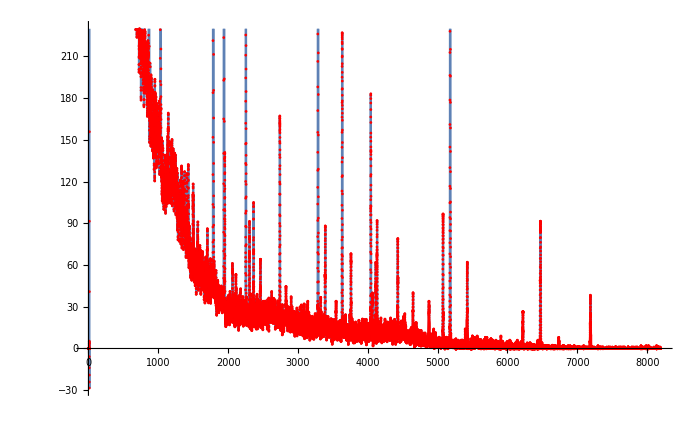

```mathematica
ListPlot[{Cases[imp[[1]],{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}][[;;,{1,3}]]},Joined->True,PlotRange->Full,GridLines->Full,ImageSize->700,Mesh->All,MeshStyle->Red,InterpolationOrder->2]
```

```mathematica
CreateDialog[{DynamicModule[{},

Cell[lodcnf:=Module[{qq,dir},{
qq=Flatten[{SystemDialogInput["FileOpen",".CNF"]}],Map[RunProcess[{"C:\\Users\\alshrafi\\Desktop\\cnfconv-master\\cnf2txt.exe",#1},"StandardOutput"]&,ToString/@qq],Print[qq],dir=Map[FileNames[#,Map[FileNameJoin,Table[ud[[All;;-2]],{ud,Map[FileNameSplit,qq]}]]]&,Map[StringJoin[#,".txt"]&,Map[FileBaseName,qq]]],Print[dir],
imp=Map[Import[#,"Table"]&,Flatten[dir]]}];Echo["lodecnf"]]]},Selectable->True,Deployed->False,WindowSize->Large];
```

lodecnf

```mathematica
listplot[]:=Module[{out},
out=ListPlot[{Cases[imp[[1]],{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}][[;;,{1,3}]]},Joined->True,PlotRange->Full,GridLines->Full,ImageSize->700,Mesh->All,MeshStyle->Red,InterpolationOrder->2]
;out]
```

```mathematica
RandomReal[1000,{2}]
```

{416.695,918.651}

```mathematica
Show[listplot[],ListPlot[bb]]
```

-Graphics-

```mathematica
ListPlot[bb]
```

-Graphics-

```mathematica
DynamicModule[{plot=listplot[],pp=bb,pE=False},
Column[{Row[{Button["Show",plot=listplot[];pE=True,Method->"Queued"],
Button["PointShow",If[pE,plot=Show[plot,ListPlot[pp]],MessageDialog["Activ Button first"]],Method->"Queued",Enabled->Dynamic[pE]]}],Dynamic[Echo[plot]]
}]]
```

```mathematica
Button["Show",Pane[Echo[listplot[]]],Method->"Queued"]
Button["PointShow",,Method->"Queued"]
```

Show

Show

SetOptions::optnf: Epilog is not a known option for listplot.

```mathematica
CellPrint
```

```mathematica
listplot[]
```

Show

```mathematica
bb
```

{{175,4843}→Am-241,{547,1274}→U-235,{600,358}→U-235,{710,1676}→Pb-214,{867,3160}→Pb-214,{867,3160}→Xe-139,{1033,5348}→Pb-214,{1788,3583}→Bi-214,{1941,2383}→Cs-137,{2306,91}→Pb-214,{2334,39}→Cs-134,{3288,628}→Bi-214,{3633,226}→Bi-214,{5180,434}→Bi-214,{6473,91}→Bi-214}

```mathematica
?bb
```

```mathematica
?o
```

```mathematica
Canvas
```

```mathematica
pp:=Module[{bb1,x,y,a1,b1,x1,f,γ2,β2},
x=[[6;;]];
y=;
γ2:=;β2=;


ROI2[ch_]:=;

mroi[ch_]:=Cases[ROI2[ch][[2,;;]],{_,u_}/;u<=Min[ROI2[ch][[1,;;,2]]]];
mRoi[ch_]:={Min[ROI2[ch][[1,;;,1]]],If[Length[mroi[ch]]!=0,First[Last[mroi[ch]]],Max[ROI2[ch][[2,;;,1]]]]};
pol[ch_]:=If[Length[mroi[ch]]==0,Polygon[{{Roi[ch]⟦1⟧,0},{Roi[ch]⟦2⟧,0},x⟦Roi[ch]⟦2⟧⟧,x⟦Roi[ch]⟦1⟧⟧}]
,Polygon[{{mRoi[ch]⟦1⟧,0},{mRoi[ch]⟦2⟧,0},x⟦mRoi[ch]⟦2⟧⟧,x⟦mRoi[ch]⟦1⟧⟧}]];





lin[ch_]:=Line[{{Flatten[Ω2[545]]⟦1,2⟧,f[ω,ch]/.Flatten[Ω2[ch]]⟦1⟧},{Flatten[Ω2[545]]⟦2,2⟧,f[ω,ch]/.Flatten[Ω2[ch]]⟦1⟧}}];blin[ch_,t_]:=;Roi[ch_]:=;NPA[ch_]:=;model[u_]:=a1 Exp[-(b1 (u-x1))^2];f2[u_,ch_]:=;Ω1[ch_]:=;Ω11[ch_]:=;Ω2[ch_]:=Module[{},(FindRoot[f2[ω,ch]==f2[ch,ch]/2.,{ω,#1}]&)/@{ch-4,ch+4}];Ω22[ch_]:=Module[{},(FindRoot[f2[ω,ch]==f2[ch,ch]/2.,{ω,#1}]&)/@Ω1[ch]⟦1;;All,1⟧];Fwhm[ch_]:=If[Abs[Subtract@@Roi[ch]]≤3,0,If[Chop[Abs[Subtract@@Ω22[ch]⟦1;;All,1,2⟧]]==0,Abs[Subtract@@Ω2[ch]⟦1;;All,1,2⟧],Abs[Subtract@@Ω22[ch]⟦1;;All,1,2⟧]]];Fwhm2[ch_]:=Abs[Subtract@@Ω22[ch]⟦1;;All,1,2⟧];Fwhm3[ch_]:=If[Abs[Subtract@@Roi[ch]]≤3,0,If[Chop[Abs[Subtract@@Ω2[ch]⟦1;;All,1,2⟧]]==0||Length[Ω22[ch]⟦1;;All,1,2⟧]==1,Abs[Subtract@@Ω2[ch]⟦1;;All,1,2⟧],Abs[Subtract@@Ω22[ch]⟦1;;All,1,2⟧]]];PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];fw=(Fwhm3[#1]&)/@β2⟦1;;All,1⟧/.u_/;u<0.01->Style["Erorr",Medium,Underlined,Purple];fchanll[t_]:=0.026698054890743093+0.34063989839856623 t;fchtoene[u_]:=(u-0.026698054890743093)/0.34063989839856623;q:=Transpose[{fchanll/@β2⟦1;;All,1⟧,NPA/@β2⟦1;;All,1⟧}];Aa[f_]:=Cases[y⟦1,1;;All,{f,f+1}⟧,{_?NumericQ,_?NumberQ}];na[f_]:=Module[{naa},naa=PeakDetect[Aa[f]⟦1;;All,2⟧,0,0,(1-1./GoldenRatio)^1.3 Max[Aa[f]⟦1;;All,2⟧]] Aa[f]/.{0.,0.}->Nothing;If[Length[naa]==0,1,Length[naa]]];df[e_]:=1.38+0.045 √e;T[f_,n_,g_]:=Module[{w,mx,t,j,m,c,na},w=Cases[y⟦1,1;;All,{f,f+1}⟧,{_?NumericQ,_?NumberQ}];na=PeakDetect[w⟦1;;All,2⟧,0,0,5] w/.{0.,0.}->Nothing;If[n>Length[w],m=Length[w],m=n];mx=TakeLargest[w⟦1;;All,2⟧,m];t=Cases[w,{_,v_/;MemberQ[mx,v]}];c=Nearest[t⟦1;;All,1⟧,g];j=Norm[g-c];If[Between[j,Flatten[{0,First[df[c]]}]],True,False]];G[f_,g_]:=Module[{α},α=Nearest[Select[y⟦1,1;;All,f⟧,NumericQ],g];If[Between[Norm[g-α],Flatten[{0,First[df[α]]}]],True,False]];H=Module[{H=q},Do[H=H/.{{g_,gg___}/;G[i,g]&&T[i,5,g]->{g,gg,y⟦1,1,i⟧}},{i,1,Length[y⟦1,1,1;;-3⟧],3}];H];mx[f_,nn_]:=TakeLargest[Aa[f]⟦1;;All,2⟧,If[nn>Length[Aa[f]],Length[Aa[f]],nn]];t[f_]:=Cases[Aa[f],{_,v_/;MemberQ[mx[f,3],v]}];eFil[n_]:=Module[{p1,p2,p,int,mxx,m},p1=Position[y⟦1,1,1;;All⟧,n];p2=Position[H,n];p[{r_,c__}]:=H⟦r⟧;int[{f_}]:=TakeLargest[t[f]⟦1;;All,2⟧,1];mxx[{f_}]:=TakeLargest[t[f]⟦1;;All,1⟧,1];m=p/@p2;Table[If[Between[Norm[i-mxx@@p1],Flatten[{0,df[i]}]],True,False],{i,m⟦1;;All,1⟧}]];p1[n_]:=Position[y⟦1,1,1;;All⟧,n];p2[n_]:=Position[H,n];p[{r_,c__}]:=H⟦r⟧;int[{f_}]:=TakeLargest[t[f]⟦1;;All,1⟧,na[f]];mxx[{f_}]:=TakeLargest[t[f]⟦1;;All,1⟧,1];m[n_]:=p/@p2[n];eeFil[n_]:=Table[If[Length[Select[(t@@Flatten[p1[n]])⟦1;;All,1⟧,Norm[#1-i]≤df[i]&]]==0,False,True],{i,m[n]⟦1;;All,1⟧}];o=Module[{k0,s,k11,iff,o},k0=Cases[H,{_,_,((__)..)?StringQ}];s=Cases[H,{_,_,__?StringQ}];k1=Union[Flatten[s⟦1;;All,3;;All⟧]];k11=k1;iff=Table[If[!Or@@eFil[k11⟦i⟧],k11⟦i⟧->Nothing],{i,Length[k11]}]/.Null->Nothing;o=Table[If[Or@@eFil[k11⟦i⟧],m[k11⟦i⟧],Nothing],{i,Length[k11]}];o=o/.iff];Res=(HH=H/.{u__/;StringQ[u]&&!MemberQ[o,u,3]->Nothing})/.{u__/;MemberQ[o,u,2]->Framed[u]}/.(#1->Highlighted[#1,Background->RandomColor[RGBColor[RandomReal[],_,_]]]&)/@k1;A[g_]:=Or@@Table[G[i,g]&&T[i,5,g],{i,1,100,3}];bbb:=Table[If[u=={},"--",(Or@@eFil[#1]&)/@u],{u,H⟦1;;All,3;;All⟧}];B:=Table[If[A[H⟦1;;All,1⟧⟦ii⟧],H⟦ii,3;;All⟧,"--"],{ii,Length[H⟦1;;All,1⟧]}];bb1:=Module[{bt={},bb,bc,j},Do[Table[Which[Length[i]==3,
bt=Append[bt,{i⟦1⟧,i⟦2⟧}->i⟦3⟧],Length[i]>3,j=3;While[j≤Length[i],bt=Append[bt,{i⟦1⟧,i⟦2⟧}->i⟦j⟧];j++]],{i,o⟦i⟧}],{i,Length[o]}];bb=Union[bt];bc=Table[bb⟦u,1⟧=x⟦Ceiling[fchtoene[First[bb⟦1;;All,1⟧⟦u⟧]]]⟧,{u,Length[bb⟦1;;All,1⟧]}];bb];
γ2]
```

```mathematica
pp
```

{5,5,5,5,5,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,8145,1/10000000000,1/10000000000,5,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,5,5,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,5,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000,5,5}
 |  |  |  |

```mathematica
x=.
```

```mathematica
lodcnf:=Module[{qq,dir},{
qq=Flatten[{SystemDialogInput["FileOpen",".CNF"]}],Map[RunProcess[{"C:\\Users\\alshrafi\\Desktop\\cnfconv-master\\cnf2txt.exe",#1},"StandardOutput"]&,ToString/@qq],Print[qq],dir=Map[FileNames[#,Map[FileNameJoin,Table[ud[[All;;-2]],{ud,Map[FileNameSplit,qq]}]]]&,Map[StringJoin[#,".txt"]&,Map[FileBaseName,qq]]],Print[dir],
imp=Map[Import[#,"Table"]&,Flatten[dir]]}]
```

```mathematica
CreatePalette[{TextCell["Click OK to close"],
DynamicModule[{plot=None,xbkg,y,γ22={},pp,xx,γg,bb,pE={False,False,False},listplots={}},
Column[{Column[{Row[{


Button["lodeCNF",lodcnf;
x=Cases[imp[[1]],{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}][[;;,{1,3}]]
;xx=x;
(*
Echo[Row[{"The BackGraund is Loded sucssfliy and length is "<>ToString[5],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo["Show"],Appearance->None]}],"x"];*)

(*
Echo[Row[{"The BackGraund is Loded sucssfliy and length is "<>ToString[Length[x]],Button["Show"]}],"x"];*)

(*Echo[ChoiceButtons[{"Skip>>","Shaw autput"},{sup=True,sup=$Failed}]];*)
(*Echo[Short[x],"x"];*)
Echo[Row[{"The Spectrum is Loded sucssfliy and length is "<>ToString[Length[x]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Short[x],"x"],Appearance->None]}],"x"];

pE[[1]]=True,Method->"Queued"]

,Button["Library Connect",y=;


Echo[Row[{"The Library is Connected sucssfliy and length is "<>ToString[Length[y]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Short[First@y],"y"],Appearance->None]}],"y"];(*Echo["The Library is Connected sucssfliy"];*)

pE[[1]]=True,Method->"Queued"]

,Button["Lode BackGraund Spectrum ",

lodcnfBKG;

xbkg=Cases[impBKG[[1]],{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}][[;;,{1,3}]];
xxbkg=xbkg;

(*Echo["The BackGraund is Loded sucssfliy"];*)

Echo[Row[{"The BackGraund is Loded sucssfliy and length is "<>ToString[Length[xbkg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Short[xbkg],"xbkg"],Appearance->None]}],"xbkg"]


;pE[[3]]=True,Method->"Queued"],

Button[" Calibration Calcute  ",lodcnf;MessageDialog["The Calibration is Loded sucssfliy"];pE[[1]]=True,Method->"Queued"]

,
Button["Init All ",
{x=xx;Echo[Row[{"The Spectrum is Loded sucssfliy and length is "<>ToString[Length[x]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Short[x],"x"],Appearance->None]}],"x"]


,γ2=;

Echo[Row[{"The γ2 is Alrady sucssfliy and length is "<>ToString[Length[γ2]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Short@γ2,"γ2:"],Appearance->None]}],"γ2:"](*;
Echo[Short@γ2,"γ2:"]*)


,β2=;
Echo[Row[{"The β2 is Alrady sucssfliy and length is "<>ToString[Length[β2]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[β2,"β2:"],Appearance->None]}],"β2:"]
(*Echo[β2=,"β2:"]*),





q=;(*Echo[q=,"q:"];*)Echo[Row[{"The q is Alrady sucssfliy and length is "<>ToString[Length[q]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[q,"q:"],Appearance->None]}],"q:"],


H=;(*Echo[H=,"H:"];*)Echo[Row[{"The H is Alrady sucssfliy and length is "<>ToString[Length[H]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[H,"H:"],Appearance->None]}],"H:"],



o=;(*Echo[o=,"o:"];*)Echo[Row[{"The o is Alrady sucssfliy and length is "<>ToString[Length[o]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[o,"o:"],Appearance->None]}],"o:"],


Res=;(*Echo[Res=,"Res:"];*)Echo[Row[{"The Res is Alrady sucssfliy and length is "<>ToString[Length[Res]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Res,"Res:"],Appearance->None]}],"Res:"],


bb3=;
(*Echo[bb3=,"bb3 :"];*)Echo[Row[{"The bb3 is Alrady sucssfliy and length is "<>ToString[Length[bb3]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[bb3,"bb3:"],Appearance->None]}],"bb3:"],

If[pE[[3]],
Block[{x=xbkg},

{(*Echo[Short[x],"xkg"]*)
Echo[Row[{"The BackGraung is Loded sucssfliy and length is "<>ToString[Length[x]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Short[x],"xkg:"],Appearance->None]}],"xkg"],

γ2kg=;

Echo[Row[{"The γ2kg is Loded sucssfliy and length is "<>ToString[Length[γ2kg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Short[γ2kg],"γ2kg:"],Appearance->None]}],"γ2kg"]
(*Echo[Short@γ2kg,"γ2kg:"]*),
β2kg=;
(*Echo[β2kg=,"β2kg:"];*)
Echo[Row[{"The β2kg is Loded sucssfliy and length is "<>ToString[Length[β2kg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[β2kg,"β2kg:"],Appearance->None]}],"β2kg"]

,qkg=;(*Echo[qkg=,"qkg:"];*)

Echo[Row[{"The qkg is Loded sucssfliy and length is "<>ToString[Length[qkg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[qkg,"qkg"],Appearance->None]}],"qkg"],

Hkg=;
(*Echo[Hkg=,"Hkg:"]*)
Echo[Row[{"The Hkg is Loded sucssfliy and length is "<>ToString[Length[Hkg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Short[Hkg],"Hkg:"],Appearance->None]}],"Hkg"],
okg=;
(*Echo[okg=,"okg:"];*)
Echo[Row[{"The okg is Loded sucssfliy and length is "<>ToString[Length[okg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[okg,"okg:"],Appearance->None]}],"okg"],

Reskg=;
(*Echo[Reskg=,"Reskg:"];*)
Echo[Row[{"The Reskg is Loded sucssfliy and length is "<>ToString[Length[Reskg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Reskg,"Reskg:"],Appearance->None]}],"Reskg"],
bb3kg=;
(*Echo[bb3kg=,"bb3kg :"]*)
Echo[Row[{"The bb3kg is Loded sucssfliy and length is "<>ToString[Length[bb3kg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[bb3kg,"bb3kg:"],Appearance->None]}],"bb3kg"]

,x=xx}],MessageDialog["BackGraund Spectrum not loded "]]},



Method->"Queued"]  ,


Button["Init2 All",{r=;
Echo[Row[{"The r is alrdy sucssfliy and length is "<>ToString[Length[r]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[r,"r:"],Appearance->None]}],"r"]
(*Echo[Short[r],"r :"]*),
fw=;
Echo[Row[{"The fw is alrdy sucssfliy and length is "<>ToString[Length[fw]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[fw,"fwhm:"],Appearance->None]}],"fwhm"];

(*Echo[fw,"fwhm:"]*)


,
αα1=;
(*Echo[αα1=,"αα1:"];*)
Echo[Row[{"The αα1 is alrdy sucssfliy and length is "<>ToString[Length[αα1]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[αα1,"αα1:"],Appearance->None]}],"αα1"],

αα2=;

(*Echo[ αα2=,"αα2:"];*)
Echo[Row[{"The αα2 is alrdy sucssfliy and length is "<>ToString[Length[αα2]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[αα2,"αα2:"],Appearance->None]}],"αα2"]
,


αα3=;
(*Echo[αα3=,"αα3 :"];*)

Echo[Row[{"The αα3 is alrdy sucssfliy and length is "<>ToString[Length[αα3]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[αα3,"αα3:"],Appearance->None]}],"αα3"]
,



	a11=;(*Echo[Short[a11],"a11"];*)
Echo[Row[{"The a11 is alrdy sucssfliy and length is "<>ToString[Length[a11]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[a11,"a11:"],Appearance->None]}],"a11"],




tab11=;(*Echo[Short[tab11],"tab11 :"]*)

Echo[Row[{"The tab11 is alrdy sucssfliy and length is "<>ToString[Length[tab11]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[tab11,"tab11:"],Appearance->None]}],"tab11"]


	  }                 ],

Button["Init2 BK All",Block[{x=xbkg,β2=β2kg,o=okg,bb3=bb3kg,q=qkg},
{

fwkg=;(*Echo[fwkg,"fwhmkg:"];*)

Echo[Row[{"The fwhmkg is alrdy sucssfliy and length is "<>ToString[Length[fwkg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[fwkg,"fwhmkg:"],Appearance->None]}],"fwkg"],



αα1kg=;
(*Echo[αα1kg=,"αα1kg:"]*)
Echo[Row[{"The αα1kg is alrdy sucssfliy and length is "<>ToString[Length[αα1kg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[αα1kg,"αα1kg:"],Appearance->None]}],"αα1kg"],


αα2kg=;
(*Echo[αα2kg=,"αα2kg:"]*)
Echo[Row[{"The αα2kg is alrdy sucssfliy and length is "<>ToString[Length[αα2kg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[αα2kg,"αα2kg:"],Appearance->None]}],"αα2kg"],


αα3kg=;
(*Echo[αα3kg=,"αα3kg :"];*)
Echo[Row[{"The αα3kg is alrdy sucssfliy and length is "<>ToString[Length[αα3kg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[αα3kg,"αα3kg:"],Appearance->None]}],"αα3kg"],

a11kg=;(*Echo[Short[a11kg],"a11kg"]*)
Echo[Row[{"The a11kg is alrdy sucssfliy and length is "<>ToString[Length[a11kg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[a11kg,"αα3kg:"],Appearance->None]}],"a11kg"],


tab11kg=Table[tab1[iϕ],{iϕ,Length[β2⟦1;;All,1⟧]}];
(*Echo[Short[tab11kg],"tab11kg :"]*)
Echo[Row[{"The tab11kg is alrdy sucssfliy and length is "<>ToString[Length[tab11kg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[tab11kg,"tab11kg:"],Appearance->None]}],"tab11kg"],


A[g_]:=Or@@Table[G[i,g]&&T[i,5,g],{i,1,100,3}];bbbkg=Table[If[uπ=={},"--",(Or@@eFil[#1]&)/@uπ],{uπ,Hkg⟦1;;All,3;;All⟧}];(*Echo[bbbkg,"bbbkg :"]*)
Echo[Row[{"The bbbkg is alrdy sucssfliy and length is "<>ToString[Length[bbbkg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[bbbkg,"bbbkg:"],Appearance->None]}],"bbbkg"],

Bkg=Table[If[A[Hkg⟦1;;All,1⟧⟦ii⟧],Hkg⟦ii,3;;All⟧,"--"],{ii,Length[Hkg⟦1;;All,1⟧]}];(*Echo[Bkg,"Bkg :"]*)
Echo[Row[{"The Bkg is alrdy sucssfliy and length is "<>ToString[Length[Bkg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Bkg,"Bkg:"],Appearance->None]}],"Bkg"]

,Activc1kg=;
(*Echo[Activc1kg,"Activc1kg :"]*)
Echo[Row[{"The Activc1kg is alrdy sucssfliy and length is "<>ToString[Length[Activc1kg]],,"-->",Button[Mouseover[Style["Show","Hyperlink"],Style["Show","HyperlinkActive"]],Echo[Activc1kg,"Activc1kg:"],Appearance->None]}],"Activc1kg"]}],Method->"Queued"]





,
Button["tab11",tab11=Table[tab1[iϕ],{iϕ,Length[β2[[;;,1]]]}];Echo[Short[tab11],"tab11 :"],Method->"Queued"]
,
Button["tabspect",tabspect=Table[spect[i],{i,Length[β2⟦1;;All,1⟧]}];Echo[Short[tabspect],"tabspect"],Method->"Queued"],


Button["αα2",Echo[ αα2=Table[Plot[{f2[ρ,ϕ],1/2 f2[ϕ,ϕ],blin[ϕ,ρ]},{ρ,-16+Roi[ϕ]⟦1⟧,16+Roi[ϕ]⟦2⟧},PlotPoints->2,ImageSize->200,PlotRange->{Automatic,All}],{ϕ,β2⟦1;;All,1⟧}];,"αα2:"],Method->"Queued"]
,
Button["Analysis",nb,Method->"Queued"]
,

,Button["Show", {










(*lpdl={{,}};*)
CreatePalette@

,



     plot=ListPlot[,]};pE[[2]]=True,Method->"Queued",Enabled->Dynamic[pE[[1]]]],


Button["PointShow",If[pE[[2]],plot=Apply[Show,{plot,ListPlot[bb3,PlotStyle->Red]}],MessageDialog["Activ Button first"]],Method->"Queued",Enabled->Dynamic[pE[[2]]]],

(*ActionMenu["PointShow",{"Show":>If[pE[[2]],showList1=True,MessageDialog["Activ Button first"]],"PointShow":>If[pE[[2]],showList2=True,MessageDialog["Activ Button first"]],"Show BKG":>If[pE[[2]],showList3=True,MessageDialog["Activ Button first"]],"BKGPointShow":>If[pE[[2]],plot=Show[ListLogLinearPlot[DeleteCases[,{_,0}],],ListLogLinearPlot[bb3,PlotStyle->Red]],MessageDialog["Activ Button first"]]},Enabled->Dynamic[pE[[2]]]]

,Button["Cansel",Echo[Abort[],"Abort[]"]]
}]*)
(*
Row[{(*RadioButton[Dynamic[plot],ListPlot[,],Enabled->Dynamic[pE[[2]]]],"Not Show BKG",*)(*RadioButton[Dynamic[plot],Show[ListPlot[,],ListPlot[,]],Enabled->Dynamic[pE[[2]]]],"Show BKG"}*)
Checkbox[Dynamic@showList1 ,{False,True},Enabled->Dynamic[pE[[2]]]],"Show",Checkbox[Dynamic@showList2,{False,True},Enabled->Dynamic[pE[[2]]]],"PointShow",Checkbox[Dynamic@showList3,{False,True},Enabled->Dynamic[pE[[2]]]],"Show BKG",Checkbox[Dynamic@showList4,{False,True},Enabled->Dynamic[pE[[2]]]],"BKGPointShow"






}]*),


ActionMenu["PointShow",{"Normal":>If[pE[[2]],plot=Show[ListPlot[{Cases[imp⟦1⟧,{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}]⟦1;;All,{1,3}⟧},],ListPlot[bb3,PlotStyle->Red]],MessageDialog["Activ Button first"]],"LogYaxis":>If[pE[[2]],plot=Show[ListLogPlot[DeleteCases[,{_,0}],],ListLogPlot[bb3,PlotStyle->Red]],MessageDialog["Activ Button first"]],"LogXYLog":>If[pE[[2]],plot=Show[ListLogLogPlot[DeleteCases[,{_,0}],],ListLogLogPlot[bb3,PlotStyle->Red]],MessageDialog["Activ Button first"]],"LogXaxis":>If[pE[[2]],plot=Show[ListLogLinearPlot[DeleteCases[,{_,0}],],ListLogLinearPlot[bb3,PlotStyle->Red]],MessageDialog["Activ Button first"]]},Enabled->Dynamic[pE[[2]]]]

,Button["Cansel",Echo[Abort[],"Abort[]"]]
}](*,Row[{Canvas[],Canvas[]}]*)}],Dynamic[Echo[plot]]

(*Dynamic[Check[listplots={};
If[showList1,AppendTo[listplots,ListPlot[{},]]];
If[showList2,AppendTo[listplots,ListPlot[bb3,PlotStyle->Red]]];
If[showList3,AppendTo[listplots,ListPlot[,]]];
If[showList4,AppendTo[listplots,ListPlot[bb3kg,MeshStyle->Lighter[Darker[Red],0.4]]]];
plot=Echo[Show[listplots]],"Eror her"];



]*)}],



Initialization:>{

lodcnf:=Module[{qq,dir},{
qq=Flatten[{SystemDialogInput["FileOpen",".CNF"]}],Map[RunProcess[{"C:\\Users\\alshrafi\\Desktop\\cnfconv-master\\cnf2txt.exe",#1},"StandardOutput"]&,ToString/@qq],Print[qq],dir=Map[FileNames[#,Map[FileNameJoin,Table[ud[[All;;-2]],{ud,Map[FileNameSplit,qq]}]]]&,Map[StringJoin[#,".txt"]&,Map[FileBaseName,qq]]],Echo[dir],
imp=Map[Import[#,"Table"]&,Flatten[dir]]}],

lodcnfBKG:=Module[{qq,dir},{
qq=Flatten[{SystemDialogInput["FileOpen",".CNF"]}],Map[RunProcess[{"C:\\Users\\alshrafi\\Desktop\\cnfconv-master\\cnf2txt.exe",#1},"StandardOutput"]&,ToString/@qq],Print[qq],dir=Map[FileNames[#,Map[FileNameJoin,Table[ud[[All;;-2]],{ud,Map[FileNameSplit,qq]}]]]&,Map[StringJoin[#,".txt"]&,Map[FileBaseName,qq]]],Echo[dir],
impBKG=Map[Import[#,"Table"]&,Flatten[dir]]}],

(*x:=Cases[imp[[1]],{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}][[;;,{1,3}]];Echo[Short[x]],*)


γ2:=,β2=Module[{β1,β23},β1=N[FindPeaks[γ2,1]]/.{{_,u_}/;u<0->Nothing,{_,v_}/;v<10->Nothing,{v_,_}/;v<32->Nothing};β23=First[Cases[x[[(#-2);;If[(#+2)>Length[x],#,#+2]]],{_,Max[x[[(#-2);;If[(#+2)>Length[x],#,#+2]]][[;;,2]]]}]]&/@β1[[;;,1]];β23=DeleteDuplicates[β23]/.{_,u_}/;u≤30->Nothing;β23=Table[If[Negative[Subtract@@Nearest[β23⟦1;;All,1⟧,u⟦1⟧,2]],If[Abs[Subtract@@Nearest[β23⟦1;;All,1⟧,u⟦1⟧,2]]≤3,Nothing,u],u],{u,β23}]],


Aa[f_]:=Cases[y⟦1,1;;All,{f,f+1}⟧,{_?NumericQ,_?NumberQ}];na[f_]:=Module[{naa},naa=PeakDetect[Aa[f]⟦1;;All,2⟧,0,0,(1-1./GoldenRatio)^1.3 Max[Aa[f]⟦1;;All,2⟧]] Aa[f]/.{0.,0.}->Nothing;If[Length[naa]==0,1,Length[naa]]],


df[e_]:=1.38+0.045 √e;T[f_,n_,g_]:=Module[{w,mx,t,j,m,c,na},w=Cases[y⟦1,1;;All,{f,f+1}⟧,{_?NumericQ,_?NumberQ}];na=PeakDetect[w⟦1;;All,2⟧,0,0,5] w/.{0.,0.}->Nothing;If[n>Length[w],m=Length[w],m=n];mx=TakeLargest[w⟦1;;All,2⟧,m];t=Cases[w,{_,v_/;MemberQ[mx,v]}];c=Nearest[t⟦1;;All,1⟧,g];j=Norm[g-c];If[Between[j,Flatten[{0,First[df[c]]}]],True,False]];G[f_,g_]:=Module[{α},α=Nearest[Select[y⟦1,1;;All,f⟧,NumericQ],g];If[Between[Norm[g-α],Flatten[{0,First[df[α]]}]],True,False]],

ROI2[ch_]:=;

mroi[ch_]:=Cases[ROI2[ch][[2,;;]],{_,uτ_}/;uτ<=Min[ROI2[ch][[1,;;,2]]]];
mRoi[ch_]:={Min[ROI2[ch][[1,;;,1]]],If[Length[mroi[ch]]!=0,First[Last[mroi[ch]]],Max[ROI2[ch][[2,;;,1]]]]};
pol[ch_]:=If[Length[mroi[ch]]==0,Polygon[{{Roi[ch]⟦1⟧,0},{Roi[ch]⟦2⟧,0},x⟦Roi[ch]⟦2⟧⟧,x⟦Roi[ch]⟦1⟧⟧}],Polygon[{{mRoi[ch]⟦1⟧,0},{mRoi[ch]⟦2⟧,0},x⟦mRoi[ch]⟦2⟧⟧,x⟦mRoi[ch]⟦1⟧⟧}]];

lin[ch_]:=Line[{{Flatten[Ω2[545]]⟦1,2⟧,f[ω,ch]/.Flatten[Ω2[ch]]⟦1⟧},{Flatten[Ω2[545]]⟦2,2⟧,f[ω,ch]/.Flatten[Ω2[ch]]⟦1⟧}}];blin[ch_,t_]:=;Roi[ch_]:=;NPA[ch_]:=Module[{},Total[x⟦Roi[ch]⟦1⟧;;Roi[ch]⟦2⟧⟧⟦1;;All,2⟧-Table[blin[ch,N[i]],{i,Range@@Roi[ch]}]]];model[ut_]:=a1 Exp[-(b1 (ut-x1))^2];f2[uτ_,ch_]:=Module[{},a1 Exp[-(b1 (uτ-x1))^2]/.FindFit[x⟦Roi[ch]⟦1⟧;;Roi[ch]⟦2⟧⟧,a1 Exp[-(b1 (uτuτ-x1))^2],{{a1,x⟦ch⟧⟦2⟧},{b1,1},{x1,ch}},uτuτ]];Ω1[ch_]:=;Ω11[ch_]:=;Ω2[ch_]:=Module[{},(FindRoot[f2[ω,ch]==f2[ch,ch]/2.,{ω,#1}]&)/@{ch-4,ch+4}];Ω22[ch_]:=Module[{},(FindRoot[f2[ω,ch]==f2[ch,ch]/2.,{ω,#1}]&)/@Ω1[ch]⟦1;;All,1⟧];Fwhm[ch_]:=If[Abs[Subtract@@Roi[ch]]≤3,0,If[Chop[Abs[Subtract@@Ω22[ch]⟦1;;All,1,2⟧]]==0,Abs[Subtract@@Ω2[ch]⟦1;;All,1,2⟧],Abs[Subtract@@Ω22[ch]⟦1;;All,1,2⟧]]];Fwhm2[ch_]:=Abs[Subtract@@Ω22[ch]⟦1;;All,1,2⟧];Fwhm3[ch_]:=If[Abs[Subtract@@Roi[ch]]≤3,0,If[Chop[Abs[Subtract@@Ω2[ch]⟦1;;All,1,2⟧]]==0||Length[Ω22[ch]⟦1;;All,1,2⟧]==1,Abs[Subtract@@Ω2[ch]⟦1;;All,1,2⟧],Abs[Subtract@@Ω22[ch]⟦1;;All,1,2⟧]]];PrintTemporary[ProgressIndicator[Appearance->"Percolate"]];fw=(Fwhm3[#1]&)/@β2⟦1;;All,1⟧/.uρρ_/;uρρ<0.01->Style["Erorr",Medium,Underlined,Purple];fchanll[tρ_]:=0.026698054890743093+0.34063989839856623 tρ;fchtoene[uρ_]:= (uρ-0.026698054890743093)/0.34063989839856623;q:=Transpose[{fchanll/@β2⟦1;;All,1⟧,NPA/@β2⟦1;;All,1⟧}],

H=Module[{H=q},Do[H=H/.{{g_,gg___}/;G[i,g]&&T[i,5,g]->{g,gg,y⟦1,1,i⟧}},{i,1,Length[y⟦1,1,1;;-3⟧],3}];H],


mx[f_,nn_]:=TakeLargest[Aa[f]⟦1;;All,2⟧,If[nn>Length[Aa[f]],Length[Aa[f]],nn]];t[f_]:=Cases[Aa[f],{_,v_/;MemberQ[mx[f,3],v]}];eFil[n_]:=Module[{p1,p2,p,int,mxx,m},p1=Position[y⟦1,1,1;;All⟧,n];p2=Position[H,n];p[{r_,c__}]:=H⟦r⟧;int[{f_}]:=TakeLargest[t[f]⟦1;;All,2⟧,1];mxx[{f_}]:=TakeLargest[t[f]⟦1;;All,1⟧,1];m=p/@p2;Table[If[Between[Norm[i-mxx@@p1],Flatten[{0,df[i]}]],True,False],{i,m⟦1;;All,1⟧}]],

p1[n_]:=Position[y⟦1,1,1;;All⟧,n];p2[n_]:=Position[H,n];p[{r_,c__}]:=H⟦r⟧;int[{f_}]:=TakeLargest[t[f]⟦1;;All,1⟧,na[f]];mxx[{f_}]:=TakeLargest[t[f]⟦1;;All,1⟧,1];m[n_]:=p/@p2[n];eeFil[n_]:=Table[If[Length[Select[(t@@Flatten[p1[n]])⟦1;;All,1⟧,Norm[#1-i]≤df[i]&]]==0,False,True],{i,m[n]⟦1;;All,1⟧}],

o=Module[{k0,s,k11,iff,o},

k0=Cases[H,{_,_,((__)..)?StringQ}];s=Cases[H,{_,_,__?StringQ}];k1=Union[Flatten[s⟦1;;All,3;;All⟧]];k11=k1;iff=Table[If[!Or@@eFil[k11⟦i⟧],k11⟦i⟧->Nothing],{i,Length[k11]}]/.Null->Nothing;o=Table[If[Or@@eFil[k11⟦i⟧],m[k11⟦i⟧],Nothing],{i,Length[k11]}];o=o/.iff],


Res:=(HH=H/.{uτ__/;StringQ[uτ]&&!MemberQ[o,uτ,3]->Nothing})/.{uτ__/;MemberQ[o,uτ,2]->Framed[uτ]}/.(#1->Highlighted[#1,Background->RandomColor[RGBColor[RandomReal[],_,_]]]&)/@k1,



A[g_]:=Or@@Table[G[i,g]&&T[i,5,g],{i,1,100,3}];bbb:=Table[If[uπ=={},"--",(Or@@eFil[#1]&)/@uπ],{uπ,H⟦1;;All,3;;All⟧}];B:=Table[If[A[H⟦1;;All,1⟧⟦ii⟧],H⟦ii,3;;All⟧,"--"],{ii,Length[H⟦1;;All,1⟧]}],

bb3:=Module[{bt={},bb2,bc,j},Do[Table[Which[Length[i]==3,bt=Append[bt,{i⟦1⟧,i⟦2⟧}->i⟦3⟧],Length[i]>3,j=3;While[j≤Length[i],bt=Append[bt,{i⟦1⟧,i⟦2⟧}->i⟦j⟧];j++]],{i,o⟦i⟧}],{i,Length[o]}];bb2=Union[bt];bc=Table[bb2⟦uτ,1⟧=x⟦Ceiling[fchtoene[First[bb2⟦1;;All,1⟧⟦uτ⟧]]]⟧,{uτ,Length[bb2⟦1;;All,1⟧]}];bb2],



spect[c_]:=Module[{ξ,ξ3},
If[MemberQ[bb3[[;;,1,1]],β2[[;;,1]][[c]]],
ξ=Position[bb3[[;;,1,1]],β2[[;;,1]][[c]]][[1,1]];
ξ3=Position[o,bb3[[;;,2]][[ξ]]][[1,1]];Graphics[{Red,Thickness[0.007],Line[{{#,-1},{#,1}}]&/@o[[ξ3,;;,1]]},PlotRange->{{0,8000},{-1,1}},Frame->False,Background->Black,AspectRatio->3/(8GoldenRatio)],Graphics[{Red,Thickness[0.005],Text[Style["..No..Info..",25,Bold,Red]]},Frame->False,Background->Black,AspectRatio->3/(8GoldenRatio)]]],


tabspect=Table[spect[i],{i,Length[β2[[;;,1]]]}],


r=;
eff:=Interpolation[r,InterpolationOrder->2],





Activc1:=Module[{τ=24*3600,wight=0.2,ee,Eff},
ee=A/@H[[;;,1]];
Eff:=Table[If[ee[[i]],(H[[;;,2]][[i]])/(eff[H[[;;,1]][[i]]]*τ*wight),"--"] ,{i,Length[ee]}];Eff],





Activc[c_]:=Module[{τ=24 3600,wight=0.2,ξ,ee,ξ2,Acti},If[MemberQ[bb3⟦1;;All,1,1⟧,β2⟦1;;All,1⟧⟦c⟧],ξ=Position[bb3⟦1;;All,1,1⟧,β2⟦1;;All,1⟧⟦c⟧]⟦1,1⟧;ξ2=Position[o,bb3⟦1;;All,2⟧⟦ξ⟧]⟦1,1⟧;ee=A/@o⟦ξ2,1;;All,1⟧;Acti:=Table[If[ee⟦i⟧,(o⟦ξ2,1;;All,2⟧⟦i⟧)/((eff[o⟦ξ2,1;;All,1⟧⟦i⟧] τ) wight),"--"],{i,Length[ee]}];Acti,"--"]],

	tab1[c_]:=Module[{ξ,ξ3,bbb,fwh,ξ2,Γ1,oo},

If[MemberQ[bb3⟦1;;All,1,1⟧,β2⟦1;;All,1⟧⟦c⟧],ξ=Position[bb3⟦1;;All,1,1⟧,β2⟦1;;All,1⟧⟦c⟧]⟦1,1⟧;ξ3=Position[o,bb3⟦1;;All,2⟧⟦ξ⟧]⟦1,1⟧;bbb=Table[If[uπ=={},"--",(Or@@eFil[#1]&)/@uπ],{uπ,o⟦ξ3,1;;All,3;;All⟧}];fwh=(((Position[q,#1]&/@o⟦ξ3,1;;All,1⟧)/.{{}->Nothing})⟦1;;All,1,1⟧);Γ1=Position[o⟦ξ3,1;;All⟧,q⟦1;;All,1⟧⟦c⟧]⟦1,1⟧;oo=Table[If[Γ1==j,o⟦ξ3,Γ1⟧/.Thread[o⟦ξ3,Γ1⟧->((Style[#1,15,Red]&)/@o⟦ξ3,Γ1⟧)],o⟦ξ3,j⟧],{j,Length[o⟦ξ3⟧]}];ξ2=TableForm[Thread[{A/@o⟦ξ3,1;;All,1⟧,oo⟦1;;All,3;;All⟧,ToString/@bbb,ToString/@Activc[c],ToString/@(Ceiling[fchtoene[#1]]&)/@o⟦ξ3,1;;All,1⟧,ToString/@fw⟦fwh⟧,ToString/@Roi/@(Ceiling[fchtoene[#1]]&)/@o⟦ξ3,1;;All,1⟧}],TableHeadings->{o⟦ξ3,1;;All,1⟧/.Thread[o⟦ξ3,Γ1⟧->(Style[#1,15,Red]&)/@o⟦ξ3,Γ1⟧],{"G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}}],"--NO-INFORMATION--"]],



tab11=Table[tab1[iτi],{iτi,Length[β2[[;;,1]]]}]


,
αα1:=Table[ListLinePlot[{x⟦-16+Roi[ii]⟦1⟧;;16+Roi[ii]⟦2⟧⟧},Epilog->{Opacity[0.5],pol[ii],Green},GridLines->Full,ImageSize->700,InterpolationOrder->1,Mesh->Full,MeshStyle->Red,PlotRange->All,AspectRatio->1/(1.5 GoldenRatio),Filling->Axis],{ii,β2⟦1;;All,1⟧}],

	   αα2:=Table[Plot[{f2[uρ,iτi],1/2 f2[iτi,iτi],blin[iτi,uρ]},{uρ,-16+Roi[iτi]⟦1⟧,16+Roi[iτi]⟦2⟧},PlotPoints->2,ImageSize->200,PlotRange->{Automatic,All}],{iτi,β2⟦1;;All,1⟧}],


αα3:=Table[N[DistributionFitTest[x⟦Roi[ii]⟦1⟧;;Roi[ii]⟦2⟧⟧⟦1;;All,2⟧,Automatic,"HypothesisTestData"]["TestDataTable",All]],{ii,β2⟦1;;All,1⟧}],


		name[ψ_]:=Module[{c=ψ,ξ},If[MemberQ[bb3⟦1;;All,1,1⟧,β2⟦1;;All,1⟧⟦c⟧],ξ=Position[bb3⟦1;;All,1,1⟧,β2⟦1;;All,1⟧⟦c⟧]⟦1,1⟧;Text[Style[Highlighted[bb3⟦ξ,2⟧,Background->Black],20,Bold,Red]],Text[Style[Highlighted["Knwon",Background->Black],20,Bold,White]]]],


		a11:=Show[ListPlot[x,PlotTheme->"Default",GridLines->Full,ImageSize->700,Axes->True,PlotRange->Full,Joined->True,InterpolationOrder->1,Mesh->Full],ListPlot[bb,PlotStyle->Red,PlotRange->All]],

nb:=CreateDialog[{DynamicModule[{c=1,min=1,max=Length[β2⟦1;;All,1⟧],a1=αα1,a2=αα2,a3=αα3,fff="",nm,ns,qq,xyx={"..."},xxx,xax,xzx},TabView[{"Show"->Dynamic[Grid[{{Column[{Row[{CancelButton[],Button["PrintPDF",FrontEndTokenExecute["PrintDialog"]],Button["Find",Dynamic[If[1≤nm≤max||NumberQ[nm],c=nm,CreateDialog[{TextCell["Not-Found"],ChoiceButtons[]}]]]],InputField[Dynamic[nm],Number,FieldHint->"N.Peak",ImageSize->{60,20}],"n",InputField[Dynamic[nm],Number,FieldHint->"chnall",ImageSize->{60,20}],"ch",InputField[Dynamic[nm],Number,FieldHint->"Energy (kev)",ImageSize->{60,20}],"Energy",Button["Find",Dynamic[If[MemberQ[H,ns,2],c=First[Position[H,ToString[ns]]⟦1⟧],CreateDialog[{TextCell["Not-Found"],ChoiceButtons[]}]]]],InputField[Dynamic[ns],String,FieldHint->"Name Elmaint",ImageSize->{60,20}],"Name",FileNameSetter[Dynamic[fff]],InputField[Text[Dynamic[fff]],Enabled->False,Appearance->"Framed"]}],Button["Prevus",c--,Enabled->Dynamic[c>min],Alignment->Center],{Dynamic[c],"channl="<>ToString[β2⟦1;;All,1⟧⟦c⟧],"Energy="<>ToString[fchanll[β2⟦1;;All,1⟧⟦c⟧]],"Fwhm="<>ToString[fw⟦c⟧],"NPA="<>ToString[NPA[β2⟦1;;All,1⟧⟦c⟧]]},Button["+",c++,Enabled->Dynamic[c<max]],a1⟦c⟧,tab11⟦c⟧}],Column[{name[c],a2⟦c⟧,a3⟦c⟧,tabspect⟦c⟧}]}}]],"Spectrum"->b,"Decy Elemnt"->ccc,"Generetor"->Row[{Button["Add",xyx=Append[xyx,RandomReal[]]],Dynamic[ListPicker[Dynamic[xax],xyx,ImageSize->450,FieldSize->{60,25},BaseStyle->{"DisplayFormulaNumbered"}]],Column[{Button["LodeCNF",qq=Flatten[{SystemDialogInput["FileOpen",".CNF"]}];xyx=Join[xyx,qq],Method->"Queued"],Button["Analysis",Dynamic[xxx=xax],ImageSize->50],InputField[Style[Text[Dynamic[xxx]],25,Red],Enabled->False,Appearance->"Framed",ImageSize->{350,35}]}],{ColorSetter[Dynamic[xa]]}}]}],DynamicUpdating->False],Row[{CancelButton[],Button["PrintPDF",FrontEndTokenExecute["PrintDialog"]],FileNameSetter[Dynamic[fff]],InputField[Text[Dynamic[fff]],Enabled->False,Appearance->"Framed"]}]},Enabled->True,WindowSize->{940,500},Background->Lighter[Orange,0.97],WindowElements->"VerticalScrollBar"]



}]},WindowSize->{940,500},Background->Lighter[Orange,0.97],Selectable->True,Deployed->False,WindowElements->{"VerticalScrollBar", "HorizontalScrollBar", "StatusArea"}]
```

jk6wt_shm37FrontEndObject[LinkObject["jk6wt_shm", 3, 1]]37Untitled-4

```mathematica
x[[540;;550]]
```

{{540,377},{541,333},{542,360},{543,376},{544,427},{545,731},{546,1022},{547,1274},{548,961},{549,587},{550,418}}

```mathematica
xb[[540;;550]]
```

Part::take: Cannot take positions 540 through 550 in xbkg.

xbkg⟦540;;550⟧

```mathematica
β2kg
```

{{138,491},{157,476},{186,503},{196,459},{214,674},{221,969},{249,802},{257,572},{272,817},{411,553},{422,561},{546,778},{577,489},{603,484},{701,660},{866,437},{993,361},{1033,536},{1499,940},{1711,241},{1788,362},{1859,163},{1874,157},{2134,153},{2355,149},{2672,196},{2830,121},{2842,161},{2858,110},{2905,105},{2937,120},{3152,103},{3289,163},{3324,99},{3335,95},{3399,99},{4044,93},{4131,72},{4287,986},{4430,62},{4661,64},{4742,40},{4757,57},{4786,53},{5079,51},{5092,33},{5179,187},{5296,36},{5423,50},{5457,33},{5526,31},{5608,35},{6471,73},{7677,406}}

```mathematica
Cases[impBKG[[1]],{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}][[;;,{1,3}]][[540;;550]]
```

{{540,412},{541,479},{542,428},{543,530},{544,598},{545,737},{546,778},{547,595},{548,465},{549,459},{550,426}}

```mathematica
bb3
```

{{175,4843}→Am-241,{547,1274}→U-235,{600,358}→U-235,{710,1676}→Pb-214,{867,3160}→Pb-214,{867,3160}→Xe-139,{1033,5348}→Pb-214,{1788,3583}→Bi-214,{1941,2383}→Cs-137,{2306,91}→Pb-214,{2334,39}→Cs-134,{3288,628}→Bi-214,{3633,226}→Bi-214,{5180,434}→Bi-214,{6473,91}→Bi-214}

```mathematica
bb3kg
```

{{547,595}→U-235,{600,458}→U-235,{710,441}→Pb-214,{867,434}→Pb-214,{867,434}→Xe-139,{1033,536}→Pb-214,{1788,362}→Bi-214,{2306,100}→Pb-214,{2334,121}→Cs-134,{3288,148}→Bi-214,{3633,104}→Bi-214,{3633,104}→Cs-136,{5180,164}→Bi-214,{6473,61}→Bi-214}

ListPlot::lpn: FE`bb$$180 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[FE`bb$$180,PlotStyle→color,PlotRange→All]].

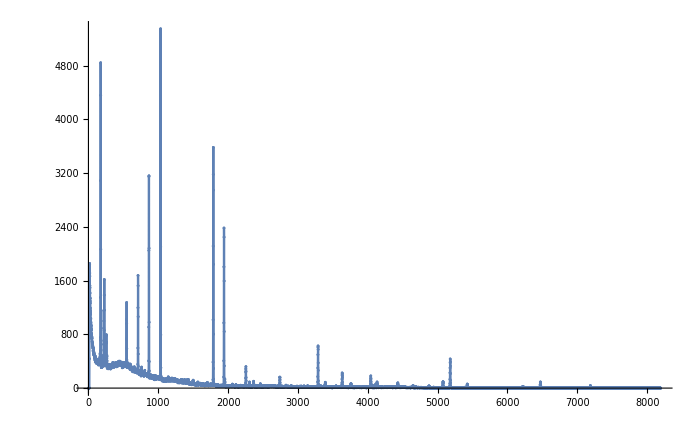
Show[-Graphics-,ListPlot[FE`bb$$180,PlotStyle→RGBColor[1, 0, 0],PlotRange→All]]

```mathematica
a11
```

```mathematica
ClearAll
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
γ2
```

```mathematica
γ2=.
```

```mathematica
β2=.
```

```mathematica
pp=Block[{},]
```

```mathematica
pp=Module[{γ2,β2},
γ2:=Module[{α,β,γ,γ23},α=x⟦1;;All,2⟧-MeanFilter[x⟦1;;All,2⟧,5]/.{u_/;u≥0->u^2.,u_/;u<0->0.};β=α-MeanFilter[x⟦1;;All,2⟧,5]/.{u_/;u≥0->0.3 u,u_/;u<0->u/10^11};γ=β-MeanFilter[x⟦1;;All,2⟧,5]/.{u_/;u≥0->1.3 u,u_/;u<0->u/10^15};γ23=γ-MeanFilter[x⟦1;;All,2⟧,5]/.{u_/;u≥0->5 u,u_/;u<0->u/10^10}];β2=Module[{β1,β23},β1=N[FindPeaks[γ2,1]]/.{{_,u_}/;u<0->Nothing,{_,v_}/;v<10->Nothing,{v_,_}/;v<32->Nothing};β23=(First[Cases[x⟦#1-2;;#1+2⟧,{_,Max[x⟦#1-2;;#1+2⟧⟦1;;All,2⟧]}]]&)/@β1⟦1;;All,1⟧;β23=DeleteDuplicates[β2]/.{_,u_}/;u≤30->Nothing;β23=Table[If[Negative[Subtract@@Nearest[β23⟦1;;All,1⟧,u⟦1⟧,2]],If[Abs[Subtract@@Nearest[β23⟦1;;All,1⟧,u⟦1⟧,2]]≤3,Nothing,u],u],{u,β23}]];Aa[f_]:=Cases[y⟦1,1;;All,{f,f+1}⟧,{_?NumericQ,_?NumberQ}];na[f_]:=Module[{naa},naa=PeakDetect[Aa[f]⟦1;;All,2⟧,0,0,(1-1./GoldenRatio)^1.3 Max[Aa[f]⟦1;;All,2⟧]] Aa[f]/.{0.,0.}->Nothing;If[Length[naa]==0,1,Length[naa]]];df[e_]:=1.38+0.045 √e;T[f_,n_,g_]:=Module[{w,mx,t,j,m,c,na},w=Cases[y⟦1,1;;All,{f,f+1}⟧,{_?NumericQ,_?NumberQ}];na=PeakDetect[w⟦1;;All,2⟧,0,0,5] w/.{0.,0.}->Nothing;If[n>Length[w],m=Length[w],m=n];mx=TakeLargest[w⟦1;;All,2⟧,m];t=Cases[w,{_,v_/;MemberQ[mx,v]}];c=Nearest[t⟦1;;All,1⟧,g];j=Norm[g-c];If[Between[j,Flatten[{0,First[df[c]]}]],True,False]];G[f_,g_]:=Module[{α},α=Nearest[Select[y⟦1,1;;All,f⟧,NumericQ],g];If[Between[Norm[g-α],Flatten[{0,First[df[α]]}]],True,False]];H=Module[{H=q},Do[H=H/.{{g_,gg___}/;G[i,g]&&T[i,5,g]->{g,gg,y⟦1,1,i⟧}},{i,1,Length[y⟦1,1,1;;-3⟧],3}];H];mx[f_,nn_]:=TakeLargest[Aa[f]⟦1;;All,2⟧,If[nn>Length[Aa[f]],Length[Aa[f]],nn]];t[f_]:=Cases[Aa[f],{_,v_/;MemberQ[mx[f,3],v]}];eFil[n_]:=Module[{p1,p2,p,int,mxx,m},p1=Position[y⟦1,1,1;;All⟧,n];p2=Position[H,n];p[{r_,c__}]:=H⟦r⟧;int[{f_}]:=TakeLargest[t[f]⟦1;;All,2⟧,1];mxx[{f_}]:=TakeLargest[t[f]⟦1;;All,1⟧,1];m=p/@p2;Table[If[Between[Norm[i-mxx@@p1],Flatten[{0,df[i]}]],True,False],{i,m⟦1;;All,1⟧}]];p1[n_]:=Position[y⟦1,1,1;;All⟧,n];p2[n_]:=Position[H,n];p[{r_,c__}]:=H⟦r⟧;int[{f_}]:=TakeLargest[t[f]⟦1;;All,1⟧,na[f]];mxx[{f_}]:=TakeLargest[t[f]⟦1;;All,1⟧,1];m[n_]:=p/@p2[n];eeFil[n_]:=Table[If[Length[Select[(t@@Flatten[p1[n]])⟦1;;All,1⟧,Norm[#1-i]≤df[i]&]]==0,False,True],{i,m[n]⟦1;;All,1⟧}];o=Module[{k0,s,k11,iff,o},k0=Cases[H,{_,_,((__)..)?StringQ}];s=Cases[H,{_,_,__?StringQ}];k1=Union[Flatten[s⟦1;;All,3;;All⟧]];k11=k1;iff=Table[If[!Or@@eFil[k11⟦i⟧],k11⟦i⟧->Nothing],{i,Length[k11]}]/.Null->Nothing;o=Table[If[Or@@eFil[k11⟦i⟧],m[k11⟦i⟧],Nothing],{i,Length[k11]}];o=o/.iff];bb3:=Module[{bt={},bb2,bc,j},Do[Table[Which[Length[i]==3,bt=Append[bt,{i⟦1⟧,i⟦2⟧}->i⟦3⟧],Length[i]>3,j=3;While[j≤Length[i],bt=Append[bt,{i⟦1⟧,i⟦2⟧}->i⟦j⟧];j++]],{i,o⟦i⟧}],{i,Length[o]}];bb2=Union[bt];bc=Table[bb2⟦u,1⟧=x⟦Ceiling[fchtoene[First[bb2⟦1;;All,1⟧⟦u⟧]]]⟧,{u,Length[bb2⟦1;;All,1⟧]}];bb2]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

MeanFilter::arg1: The first argument Symbol[] is neither a rectangular array nor an image.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

MeanFilter::arg1: The first argument Symbol[] is neither a rectangular array nor an image.

General::stop: Further output of MeanFilter::arg1 will be suppressed during this calculation.

FindPeaks::arg: The argument 5+(50000000001 MeanFilter[Symbol[],5])/10000000000+Symbol[] at position 1 is not a consistent list of real values.

FindPeaks::arg: The argument 5.+5. MeanFilter[Symbol[],5.]+Symbol[] at position 1 is not a consistent list of real values.

Part::partd: Part specification FindPeaks[5.+5. MeanFilter[Symbol[],5.]+Symbol[],1.]⟦1;;All,1⟧ is longer than depth of object.

Part::span: -2+FindPeaks[5.+5. MeanFilter[Symbol[],5.]+Symbol[],1.];;2+FindPeaks[5.+5. MeanFilter[Symbol[],5.]+Symbol[],1.] is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partd: Part specification x⟦-2+FindPeaks[5.+5. MeanFilter[«2»]+Symbol[],1.];;2+FindPeaks[5.+5. MeanFilter[«2»]+Symbol[],1.]⟧⟦1;;All,2⟧ is longer than depth of object.

First::nofirst: {} has zero length and no first element.

Part::span: -2+1;;All;;2+1;;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Part::partd: Part specification x⟦-2+1;;All;;2+1;;All⟧⟦1;;All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

Part::take: Cannot take positions -1 through 3 in x.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Part::pkspec1: The expression First[{}] cannot be used as a part specification.

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[β2$15401].

Table::iterb: Iterator {u,DeleteDuplicates[β2$15401]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of DeleteDuplicates[β2$15401].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Hold[DeleteDuplicates[β2$15401]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Floor[0.5].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{Symbol::argx,Symbol::argx,MeanFilter::arg1,MeanFilter::arg1,Symbol::argx,General::stop,MeanFilter::arg1,General::stop,FindPeaks::arg,FindPeaks::arg,«25»}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[Table::iterb :  Iterator {u,Table[If[Negative[Subtract@@Nearest[β23$15402⟦Span[«2»],1⟧,u⟦1⟧,2]],If[Abs[Subtract@@Nearest[«3»]]≤3,Nothing,u],u],{u,Hold[Table[If[Negative[Apply[«2»]],If[LessEqual[«2»],Nothing,u],u],{u,Hold[Hold[«1»]]}]]}]} does not have appropriate bounds.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Table::iterb,Table::iterb,Table::iterb}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Table::iterb: Iterator {u,Table[If[Negative[Subtract@@Nearest[β23$15402⟦Span[«2»],1⟧,u⟦1⟧,2]],If[Abs[Subtract@@Nearest[«3»]]≤3,Nothing,u],u],{u,Table[If[Negative[Subtract@@Nearest[«3»]],If[Abs[«1»]≤3,Nothing,u],u],{u,Hold[Table[If[«3»],{«2»}]]}]}]} does not have appropriate bounds.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Table::iterb: Iterator {u,Table[If[Negative[Subtract@@Nearest[β23$15402⟦Span[«2»],1⟧,u⟦1⟧,2]],If[Abs[Subtract@@Nearest[«3»]]≤3,Nothing,u],u],{u,Table[If[Negative[Subtract@@Nearest[«3»]],If[Abs[«1»]≤3,Nothing,u],u],{u,Hold[Table[If[«3»],{«2»}]]}]}]} does not have appropriate bounds.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit::itlim will be suppressed during this calculation.

Table::iterb: Iterator {u,Table[If[Negative[Subtract@@Nearest[β23$15402⟦Span[«2»],1⟧,u⟦1⟧,2]],If[Abs[Subtract@@Nearest[«3»]]≤3,Nothing,u],u],{u,Table[If[Negative[Subtract@@Nearest[«3»]],If[Abs[«1»]≤3,Nothing,u],u],{u,Hold[Table[If[«3»],{«2»}]]}]}]} does not have appropriate bounds.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

Hold[General::stop :  Further output of Table::iterb will be suppressed during this calculation.]

Table::iterb: Iterator {u,Table[If[Negative[Subtract@@Nearest[β23$15402⟦Span[«2»],1⟧,u⟦1⟧,2]],If[Abs[Subtract@@Nearest[«3»]]≤3,Nothing,u],u],{u,Table[If[Negative[Subtract@@Nearest[«3»]],If[Abs[«1»]≤3,Nothing,u],u],{u,Table[If[Negative[«1»],If[«3»],u],{u,Hold[«1»]}]}]}]} does not have appropriate bounds.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

```mathematica
NotebookEventActions->"WindowSelected":>NotebookWrite[EvaluationNotebook[],Cell[




Echo[lodcnf:=Module[{qq,dir},{
qq=Flatten[{SystemDialogInput["FileOpen",".CNF"]}],Map[RunProcess[{"C:\\Users\\alshrafi\\Desktop\\cnfconv-master\\cnf2txt.exe",#1},"StandardOutput"]&,ToString/@qq],Print[qq],dir=Map[FileNames[#,Map[FileNameJoin,Table[ud[[All;;-2]],{ud,Map[FileNameSplit,qq]}]]]&,Map[StringJoin[#,".txt"]&,Map[FileBaseName,qq]]],Print[dir],
imp=Map[Import[#,"Table"]&,Flatten[dir]]}],"OK.."],"Output"]
```

```mathematica
DeleteCases[x,{_,0}]
```

DeleteCases[{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,1},{12,0},{13,4},{14,437},{15,1276},{16,1760},{17,1855},{18,1844},{19,1712},{20,1666},{21,1524},{22,1495},{23,1415},{24,1340},{25,1333},{26,1295},{27,1265},{28,1192},8136,{8165,0},{8166,0},{8167,0},{8168,0},{8169,0},{8170,0},{8171,0},{8172,1},{8173,0},{8174,0},{8175,0},{8176,0},{8177,0},{8178,0},{8179,0},{8180,0},{8181,0},{8182,0},{8183,0},{8184,0},{8185,1},{8186,0},{8187,0},{8188,0},{8189,0},{8190,0},{8191,0},{8192,0}}]
 |  |  |  |

```mathematica
ActionMenu["PointShow",{"Normal":>If[pE[[2]],plot=Show[ListPlot[a,],ListPlot[pp,PlotStyle->Red]],MessageDialog["Activ Button first"]],"Log":>If[pE[[2]],plot=Show[ListLogPlot[a,],ListLogPlot[pp,PlotStyle->Red]],MessageDialog["Activ Button first"]],"LogLog":>If[pE[[2]],plot=Show[ListLogLogPlot[a,],ListLogLogPlot[pp,PlotStyle->Red]],MessageDialog["Activ Button first"]]}]
```

PointShow

24

```mathematica
ListPlot[{Cases[imp[[1]],{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}][[;;,{1,3}]]},Joined->True,PlotRange->Full,GridLines->Full,ImageSize->700,Mesh->All,MeshStyle->Red,InterpolationOrder->2]
```

```mathematica
MenuView
```

```mathematica
RadioButtonBar[u,{1->"Ein",2->"Zwei",3->"Drei"}]
```

```mathematica
RadioButton[]
```

```mathematica
DynamicModule[{plot=None,pp=bb,pE={False,False}},
Column[{Row[{Button["lodeCNF",lodcnf;pE[[1]]=True,Method->"Queued"],Button["Show",plot=listplot[];pE[[2]]=True,Method->"Queued",Enabled->Dynamic[pE[[1]]]],
Button["PointShow",If[pE[[2]],plot=Show[plot,ListPlot[pp,PlotStyle->Red]],MessageDialog["Activ Button first"]],Method->"Queued",Enabled->Dynamic[pE[[2]]]]}],Dynamic[Echo[plot]]}]]
```

{C:\Users\alshrafi\Desktop\cnfconv-master\131022-3+44sourcel-MRS8 Am241+Ra226+cs137 125 ml vol.CNF}

{{C:\Users\alshrafi\Desktop\cnfconv-master\131022-3+44sourcel-MRS8 Am241+Ra226+cs137 125 ml vol.txt}}

```mathematica
Module[{x=[[6;;]],y=},
;
bb]
```

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair Am-241 and 2505..

General::stop: Further output of Nearest::neard will be suppressed during this calculation.

{{175,4843}→Am-241,{547,1274}→U-235,{600,358}→U-235,{710,1676}→Pb-214,{867,3160}→Pb-214,{867,3160}→Xe-139,{1033,5348}→Pb-214,{1788,3583}→Bi-214,{1941,2383}→Cs-137,{2306,91}→Pb-214,{2334,39}→Cs-134,{3288,628}→Bi-214,{3633,226}→Bi-214,{5180,434}→Bi-214,{6473,91}→Bi-214}

```mathematica
ΔΓ=Map[Cases[#,{_?NumberQ,_?NumberQ,_?NumberQ,_?NumberQ}]&,imp]
```

{{{1,0.374,0,0},{2,0.715,0,0},{3,1.055,0,0},{4,1.396,0,0},{5,1.737,0,0},{6,2.078,0,0},{7,2.418,0,0},{8,2.759,0,0},{9,3.1,0,0},{10,3.441,0,0},{11,3.781,0,0},{12,4.122,0,0},{13,4.463,0,0},8166,{8180,2787.53,0,0},{8181,2787.87,0,0},{8182,2788.21,1,0.000833333},{8183,2788.55,0,0},{8184,2788.89,0,0},{8185,2789.23,0,0},{8186,2789.57,0,0},{8187,2789.91,0,0},{8188,2790.26,0,0},{8189,2790.6,0,0},{8190,2790.94,0,0},{8191,2791.28,0,0},{8192,2791.62,0,0}},3,{1}}
 |  |  |  |

```mathematica
x
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,1},{12,0},{13,4},{14,437},{15,1276},{16,1760},{17,1855},{18,1844},{19,1712},{20,1666},{21,1524},{22,1495},{23,1415},{24,1340},{25,1333},{26,1295},{27,1265},{28,1192},{29,1157},{30,1129},8133,{8164,0},{8165,0},{8166,0},{8167,0},{8168,0},{8169,0},{8170,0},{8171,0},{8172,1},{8173,0},{8174,0},{8175,0},{8176,0},{8177,0},{8178,0},{8179,0},{8180,0},{8181,0},{8182,0},{8183,0},{8184,0},{8185,1},{8186,0},{8187,0},{8188,0},{8189,0},{8190,0},{8191,0},{8192,0}}
 |  |  |  |

```mathematica
ΔΓ[[2]][[;;,{1,3}]]
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,1},{12,0},{13,0},{14,7},8164,{8179,0},{8180,0},{8181,0},{8182,0},{8183,0},{8184,0},{8185,0},{8186,0},{8187,1},{8188,0},{8189,0},{8190,0},{8191,0},{8192,0}}
 |  |  |  |

```mathematica
Block[{x=ΔΓ[[1]][[;;,{1,3}]]},β2]
```

{{175,1815},{221,170},{355,157},{427,154},{538,169},{570,185},{872,123},{1043,114},{1115,110},{1395,125},{1770,45},{1834,48},{1942,6423},{3443,934},{3911,776},{4288,38}}

```mathematica
β2
```

{{175,4843},{220,1156},{227,1617},{248,444},{257,795},{264,488},{547,1274},{600,358},{657,318},{710,1676},{761,313},{807,265},{867,3160},{1033,5348},{1143,168},{1377,127},{1410,125},{1430,129},{1567,91},{1703,86},{1788,3583},{1827,56},{1941,2383},{1952,137},{2027,41},{2112,53},{2255,320},{2306,91},{2334,39},{2365,102},{2462,64},{2624,41},{2741,163},{3288,628},{3326,35},{3391,87},{3633,226},{3759,68},{4043,182},{4066,40},{4114,62},{4133,92},{4430,79},{4648,40},{4876,34},{5077,95},{5180,434},{5424,60},{6473,91},{7187,37}}

```mathematica
γ2
```

{0.,0.,0.,0.,0.,-9.09091×10^-12,-9.09091×10^-12,-4.54545×10^-11,-4.01818×10^-9,-1.56182×10^-8,-3.16182×10^-8,-4.84818×10^-8,-6.52455×10^-8,8166,-9.09091×10^-12,-9.09091×10^-12,-9.09091×10^-12,-9.09091×10^-12,-9.09091×10^-12,0.388843,-9.09091×10^-12,-9.09091×10^-12,-1.×10^-11,-1.11111×10^-11,-1.25×10^-11,0.,0.}
 |  |  |  |

```mathematica
γ2
```

{0.,0.,0.,0.,0.,-9.09091×10^-12,-9.09091×10^-12,-4.54545×10^-11,-4.01818×10^-9,-1.56182×10^-8,-3.16182×10^-8,8170,-9.09091×10^-12,-9.09091×10^-12,-9.09091×10^-12,0.388843,-9.09091×10^-12,-9.09091×10^-12,-1.×10^-11,-1.11111×10^-11,-1.25×10^-11,0.,0.}
 |  |  |  |

```mathematica
?γ2
```

```mathematica
ΔΓ[[1]]//Short
```

{{1,0.374,0,0},{2,0.715,0,0},{3,1.055,0,0},«8187»,{8191,2791.28,0,0},{8192,2791.62,0,0}}

```mathematica
β2:=Module[{β1,β2},
β1=N@FindPeaks[γ2,1]/.{{_,u_}/;u<0->Nothing,{_,v_}/;v<10->Nothing,{v_,_}/;v<32->Nothing};
β2=First[Cases[x[[(#-2);;(#+2)]],{_,Max[x[[(#-2);;(#+2)]][[;;,2]]]}]]&/@β1[[;;,1]];
β2=DeleteDuplicates[β2]/.{_,u_}/;u<=30->Nothing;
β2=Table[If[Negative[Subtract@@Nearest[β2[[;;,1]],u[[1]],2]],If[Abs[Subtract@@Nearest[β2[[;;,1]],u[[1]],2]]<=3,Nothing,u],u],{u,β2}]]
```

```mathematica
x=ΔΓ[[2]];
Goto[g2];
Goto[be2];
```

Goto::nolabel: Label g2 not found.

Hold[Goto[g2]]

Goto::nolabel: Label be2 not found.

Hold[Goto[be2]]

```mathematica
Goto
```

```mathematica
Button["Analys",Module[{x=ΔΓ[[1]],γ2,β2},;
]
```

```mathematica
Map[FileNames[#,Map[FileNameJoin,Table[ud[[All;;-2]],{ud,Map[FileNameSplit,qq]}]]]&,Map[StringJoin[#,".txt"]&,Map[FileBaseName,qq]]]
```

```mathematica
?/:
```

```mathematica
{{"C:\\Users\\pc\\Desktop\\_\\220423-01-200ml.txt"}}
```

```mathematica
Map[StringJoin[#,".txt"]&,Map[FileBaseName,qq]]
```

```mathematica
Iconize/@Map[Import[#,"Table"]&,Flatten[dir]]
```

{,}

```mathematica
lodcnf:=Module[{qq,qa,dir,imp,icodata},
Button["LodeCNF",
qq=Flatten[{SystemDialogInput["FileOpen",".CNF"]}];qa=Map[RunProcess[{"C:\\Users\\pc\\Desktop\\cnfconv-master\\cnf2txt.exe",#1},"StandardOutput"]&,ToString/@qq];dir=FileNames["*.txt",Map[FileNameJoin,Table[ud[[All;;-2]],{ud,Map[FileNameSplit,qq]}]]];
icodata=Map[Import[#,"Table"]&,dir]
,Method->"Queued"]


]
```

```mathematica
dd=FileNames["*.txt",Map[FileNameJoin,Table[u[[All;;-2]],{u,Map[FileNameSplit,qq]}]]]
```

```mathematica
{"C:\\Users\\pc\\Desktop\\_\\220423-01-200ml.txt","C:\\Users\\pc\\Desktop\\_\\220423-02-200ml.txt"}
```

{C:\Users\pc\Desktop\_\220423-01-200ml.txt,C:\Users\pc\Desktop\_\220423-02-200ml.txt}

```mathematica
Map[Iconize,Map[Import[#,"Table"]&,dd]]
```

{,}

```mathematica
qq={"C:\\Users\\pc\\Desktop\\_\\220423-01-200ml.CNF","C:\\Users\\pc\\Desktop\\_\\220423-02-200ml.CNF"}
```

{C:\Users\pc\Desktop\_\220423-01-200ml.CNF,C:\Users\pc\Desktop\_\220423-02-200ml.CNF}

```mathematica
Table[u[[All;;-2]],{u,Map[FileNameSplit,qq]}]
```

{{C:,Users,pc,Desktop,_},{C:,Users,pc,Desktop,_}}

```mathematica
{"C:\\Users\\pc\\Desktop\\_\\220423-01-200ml.CNF","C:\\Users\\pc\\Desktop\\_\\220423-02-200ml.CNF"}
```

```mathematica
"\\n{C:\\Users\\pc\\Desktop\\_\\220423-01-200ml.CNF, C:\\Users\\pc\\Desktop\\_\\220423-02-200ml.CNF}"
```

```mathematica
lodcnf=.
```

```mathematica
qa
```

C:\Users\pc\Desktop\_\220423-01-200ml.CNF

```mathematica
FileNameJoin[FileNameSplit["C:\\Users\\pc\\Desktop\\_\\220423-01-200ml.txt"][[All;;-2]]]
```

C:\Users\pc\Desktop\_

```mathematica
"C:\\Users\\pc\\Desktop\\_"
```

```mathematica
FileNameTake["C:\\Users\\pc\\Desktop\\_\\220423-01-200ml.txt",-1;;]
```

FileNameTake::seqso: Sequence specification (+n, -n, {+n}, {-n}, or {m, n}) expected at position 2 in -1;;All.

FileNameTake[C:\Users\pc\Desktop\_\220423-01-200ml.txt,-1;;All]

```mathematica
qq
```

{C:\Users\pc\Documents\obidah.mo,C:\Users\pc\Documents\البحث.nb,C:\Users\pc\Documents\المصنف1.xlsx}

```mathematica
dir=FileNames["*.CNF","C:\\Users\\pc\\Desktop\\_"]
```

{C:\Users\pc\Desktop\_\220423-01-200ml.CNF,C:\Users\pc\Desktop\_\220423-02-200ml.CNF,C:\Users\pc\Desktop\_\220723-01-200ml.CNF,C:\Users\pc\Desktop\_\240423-01-200ml.CNF,C:\Users\pc\Desktop\_\250223-01-200ml.CNF,C:\Users\pc\Desktop\_\250723-01-200ml.CNF,C:\Users\pc\Desktop\_\260223-01-200ml.CNF,C:\Users\pc\Desktop\_\260223-02-200ml.CNF,C:\Users\pc\Desktop\_\260423-01-200ml.CNF,C:\Users\pc\Desktop\_\280423-01-200ml.CNF,C:\Users\pc\Desktop\_\280423-02-200ml.CNF}

```mathematica
dir2=FileNames["*.txt","C:\\Users\\pc\\Desktop\\_"]
```

{C:\Users\pc\Desktop\_\220423-01-200ml.txt,C:\Users\pc\Desktop\_\220423-02-200ml.txt,C:\Users\pc\Desktop\_\220723-01-200ml.txt,C:\Users\pc\Desktop\_\240423-01-200ml.txt,C:\Users\pc\Desktop\_\250223-01-200ml.txt,C:\Users\pc\Desktop\_\250723-01-200ml.txt,C:\Users\pc\Desktop\_\260223-01-200ml.txt,C:\Users\pc\Desktop\_\260223-02-200ml.txt,C:\Users\pc\Desktop\_\260423-01-200ml.txt,C:\Users\pc\Desktop\_\280423-01-200ml.txt,C:\Users\pc\Desktop\_\280423-02-200ml.txt}

```mathematica
Iconize/@(Import[#,"Table"]&/@dir2)
```

{,,,,,,,,,,}

```mathematica
vals=Table[IsotopeData[#,prop],{prop,{"Symbol","HalfLife","BindingEnergy"}}]&/@IsotopeData["TwoNeutronEmission"]
```

{{^5H,8.×10^-23 s,1.33636 MeV},{^7H,2.3×10^-23 s,0.9401 MeV},{^10He,1.5×10^-21 s,3.033927 MeV},{^16Be,2.×10^-7 s,4.271 MeV},{^25N,2.6×10^-7 s,5.592 MeV},{^26O,4.×10^-8 s,6.457 MeV},{^27O,2.6×10^-7 s,6.175 MeV},{^28O,1.×10^-7 s,5.925 MeV}}

```mathematica
{FileNameSetter[Dynamic[f],"OpenList"],Dynamic[aq=f]}
```

```mathematica
SystemDialogInput
```

```mathematica
Needs["SciPhon"]
```

Needs::cxt: Invalid context specified at position 1 in Needs[SciPhon]. A context must consist of valid symbol names separated by and ending with `.

Needs[SciPhon]

```mathematica
IsotopeData
```

```mathematica
Tooltip[xxy+yyx,"label"]
```

xxy+yyx

```mathematica
ListPicker
```

```mathematica
Button["Show",nb,ImageSize->{300,300}]
```

Show

```mathematica
nm=.
```

```mathematica
CreateDialog[{TextCell["Enter a name: "],InputField[Dynamic[nm],String],Button["ok",Dynamic[If[TrueQ[nm=="obidah"],nb,nc]]]}];
```

```mathematica
nc:=CreateDialog[{TextCell["Your name is Fals "],ChoiceButtons[]}]
```

```mathematica
nc
```

isc8f_shm169FrontEndObject[LinkObject["isc8f_shm", 3, 1]]169169

```mathematica
DialogInput[DynamicModule[{name=""},Column[{"Enter username:",
InputField[Dynamic[name],String],
ChoiceButtons[{DialogReturn[name],DialogReturn[]}]}]]]
```

```mathematica
FrontEndTokenExecutepaclet:ref/FrontEndTokenExecute["PrintDialog"]
```

```mathematica
FrontEndTokenExecute["PrintDialog"]
```

```mathematica
Open
```

```mathematica
Grid[]
```

Grid[]

```mathematica
PaletteNotebook[{TextCell["Center"],

DynamicModule[{c=1,min=1,max=Length[β2[[;;,1]]],a1=αα1,a2=αα2,a3=αα3},
Dynamic[{Column[{Button["Prevus", c--, Enabled->Dynamic[c>min]],{ Dynamic[c], "channl="<>ToString[β2[[;;,1]][[c]]],"Energy="<>ToString[fchanll[β2[[;;,1]][[c]]]],"Fwhm="<>ToString[fw[[c]]],"NPA="<>ToString[NPA[β2[[;;,1]][[c]]]]},Button["+", c++, Enabled->Dynamic[c<max]],a1[[c]],tab11[[c]]}],Column[{name[c],a2[[c]],a3[[c]],tabspect[[c]]}]}]]}]
```

Center

```mathematica
n=1;Do[CreateDocument[TextCell["abcd","Text"],WindowFrame->wf,WindowSize->{200,200},WindowTitle->wf],{wf,{"Normal","Palette","ModelessDialog","Frameless"}}]
```

```mathematica
Button["Show",PaletteNotebook[{TextCell["Center"],

DynamicModule[{c=1,min=1,max=Length[β2[[;;,1]]],a1=αα1,a2=αα2,a3=αα3},
Dynamic[{Column[{Button["Prevus", c--, Enabled->Dynamic[c>min]],{ Dynamic[c], "channl="<>ToString[β2[[;;,1]][[c]]],"Energy="<>ToString[fchanll[β2[[;;,1]][[c]]]],"Fwhm="<>ToString[fw[[c]]],"NPA="<>ToString[NPA[β2[[;;,1]][[c]]]]},Button["+", c++, Enabled->Dynamic[c<max]],a1[[c]],tab11[[c]]}],Column[{name[c],a2[[c]],a3[[c]],tabspect[[c]]}]}]]

,CancelButton[]},WindowSize->{600,400},WindowMargins->Automatic]]
```

Show

```mathematica
Button["Show",δ]
```

Show

```mathematica
DynamicModule[{c=1,min=1,max=Length[β2[[;;,1]]],a1=αα1,a2=αα2,a3=αα3},
Dynamic[{Column[{Button["Prevus", c--, Enabled->Dynamic[c>min]],{ Dynamic[c], "channl="<>ToStrin]غg[β2[[;;,1]][[c]]],"Energy="<>ToString[fchanll[β2[[;;,1]][[c]]]],"Fwhm="<>ToString[fw[[c]]],"NPA="<>ToString[NPA[β2[[;;,1]][[c]]]]},Button["+", c++, Enabled->Dynamic[c<max]],a1[[c]],tab11[[c]]}],Column[{name[c],a2[[c]],a3[[c]],tabspect[[c]]}]}]]
```

```mathematica
Fwhm[547]
```

8.69627

```mathematica
Fwhm[1827]
```

Subtract::argr: Subtract called with 1 argument; 2 arguments are expected.

If[Abs[Subtract[1823.48]]==0,Abs[Subtract@@Ω2[1827]⟦1;;All,1,2⟧],Abs[Subtract@@Ω22[1827]⟦1;;All,1,2⟧]]

```mathematica
DynamicModule[{c=1,min=1,max=Length[β2[[;;,1]]],a1=αα1,a2=αα2,a3=αα3},
Dynamic[{Column[{Button["Prevus", c--, Enabled->Dynamic[c>min]],{ Dynamic[c], "channl="<>ToString[β2[[;;,1]][[c]]],"Energy="<>ToString[fchanll[β2[[;;,1]][[c]]]],"Fwhm="<>ToString[fw[[c]]],"NPA="<>ToString[NPA[β2[[;;,1]][[c]]]]},Button["+", c++, Enabled->Dynamic[c<max]],a1[[c]],tab11[[c]]}],Column[{name[c],a2[[c]],a3[[c]],Graphics[{Red,Thickness[0.01],Line[{{0,-1},{0,1}}]},Frame->False,Background->Black,AspectRatio->1/(2GoldenRatio)]}]}]]
```

```mathematica
Fwhm[5180]
```

6.17045

```mathematica
ROI[6470]
```

ROI[6470]

```mathematica
δ=DynamicModule[{c=1,min=1,max=Length[β2[[;;,1]]],a1=αα1,a2=αα2,a3=αα3},
Dynamic[{Column[{Button["Prevus", c--, Enabled->Dynamic[c>min]],{ Dynamic[c], "channl="<>ToString[β2[[;;,1]][[c]]],"Energy="<>ToString[fchanll[β2[[;;,1]][[c]]]],"Fwhm="<>ToString[fw[[c]]],"NPA="<>ToString[NPA[β2[[;;,1]][[c]]]]},Button["+", c++, Enabled->Dynamic[c<max]],a1[[c]],tab11[[c]]}],Column[{name[c],a2[[c]],a3[[c]],Graphics[{Red,Thickness[0.01],Line[{{0,-1},{0,1}}]},Frame->False,Background->Black,AspectRatio->1/(2GoldenRatio)]}]}]];
```

```mathematica
CreatePalette[{TextCell["Center"],CancelButton[]},WindowMargins->Automatic];
```

```mathematica
DynamicModule[{c=1,min=1,max=Length[β2[[;;,1]]],a1=αα1,a2=αα2,a3=αα3},
Dynamic[{Column[{Button["Prevus", c--, Enabled->Dynamic[c>min]],{ Dynamic[c], "channl="<>ToString[β2[[;;,1]][[c]]],"Energy="<>ToString[fchanll[β2[[;;,1]][[c]]]],"Fwhm="<>ToString[fw[[c]]],"NPA="<>ToString[NPA[β2[[;;,1]][[c]]]]},Button["+", c++, Enabled->Dynamic[c<max]],a1[[c]],tab11[[c]]}],Column[{name[c],a2[[c]],a3[[c]],Graphics[{Red,Thickness[0.01],Line[{{0,-1},{0,1}}]},Frame->False,Background->Black,AspectRatio->1/(2GoldenRatio)]}]}]];
```

```mathematica
fw/.u_String->0
```

{3.40278,6.81409,4.48198,20.4123,7.5121,10.1973,6.93005,0,8.51947,4.63476,13.2135,16.7576,0,0,11.0085,0,8.77298,9.20377,0,10.9681,4.31584,5.91979,0,7.14635,0,10.2565,5.45497,10.6375,0,5.59517,6.74083,0,6.0687,5.51632,0,6.33894,6.23734,7.2334,6.18126,0,0,6.55879,7.15325,5.59963,6.7102,7.08878,6.27348,6.16998,6.17096,6.43075,7.42545,5.69457}

```mathematica
tab12[[1]]/.{ToString[fw[[c]]]->Style[ToString[fw[[c]]],Medium,Bold,Red]}
```

{{True,{Am-241},{True},213.969,175,3.40278,{170, 180}},{False,--,--,--,220,6.81409,{216, 224}},{False,--,--,--,227,4.48198,{224, 231}},{False,--,--,--,248,20.4123,{244, 249}},{True,--,{False},5.13027,257,7.5121,{252, 261}},{False,--,--,--,264,10.1973,{261, 269}},{True,{U-235, Ra-226},{True, True},6.58721,547,6.93005,{541, 553}},{True,--,{True},0.591549,600,Erorr,{599, 602}},{False,--,--,--,657,8.51947,{654, 658}},{True,{Pb-214},{True},12.402,710,4.63476,{705, 718}},{True,--,{False},1.86203,761,13.2135,{755, 764}},{True,--,{False, False},0.394481,807,16.7576,{801, 809}},{True,{Pb-214, Au-194, Xe-139},{True, False, False},32.2203,867,Erorr,{859, 873}},{True,{Pb-214},{True},61.8326,1033,Erorr,{1026, 1040}},{False,--,--,--,1143,11.0085,{1142, 1146}},{False,--,--,--,1377,Erorr,{1375, 1378}},{False,--,--,--,1410,8.77298,{1406, 1413}},{False,--,--,--,1430,9.20377,{1425, 1433}},{False,--,--,--,1567,Erorr,{1566, 1569}},{False,--,--,--,1703,10.9681,{1696, 1705}},{True,{Bi-214},{True},71.6779,1788,4.31584,{1779, 1796}},{False,--,--,--,1827,5.91979,{1824, 1828}},{True,{Cs-137},{True},50.595,1941,Erorr,{1934, 1947}},{False,--,--,--,1952,7.14635,{1947, 1960}},{False,--,--,--,2027,Erorr,{2026, 2028}},{False,--,--,--,2112,10.2565,{2106, 2114}},{True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.45497,{2249, 2264}},{True,--,{True, False},2.42456,2306,10.6375,{2305, 2316}},{True,{Cs-134},{False},0.501527,2334,Erorr,{2332, 2336}},{True,{Ag-99},{False},2.54244,2365,5.59517,{2363, 2369}},{True,--,--,1.35008,2462,6.74083,{2458, 2464}},{False,--,--,--,2624,Erorr,{2622, 2625}},{False,--,--,--,2741,6.0687,{2734, 2747}},{True,{Bi-214},{True},24.9387,3288,5.51632,{3279, 3294}},{False,--,--,--,3326,Erorr,{3324, 3328}},{False,--,--,--,3391,6.33894,{3389, 3399}},{True,--,{True, False},9.47725,3633,6.23734,{3627, 3642}},{True,--,--,3.18035,3759,7.2334,{3756, 3767}},{False,--,--,--,4043,6.18126,{4037, 4051}},{True,--,{False},1.89004,4066,Erorr,{4065, 4067}},{True,--,{False},1.89004,4066,Erorr,{4065, 4067}},{False,--,--,--,4114,6.55879,{4110, 4118}},{False,--,--,--,4133,7.15325,{4126, 4140}},{False,--,--,--,4430,5.59963,{4426, 4432}},{False,--,--,--,4648,6.7102,{4641, 4651}},{False,--,--,--,4876,7.08878,{4869, 4877}},{False,--,--,--,5077,6.27348,{5069, 5081}},{True,{Bi-214},{True},25.8327,5180,6.16998,{5171, 5190}},{True,--,{False},3.16738,5424,6.17096,{5417, 5433}},{True,--,{True},7.01719,6470,6.43075,{6464, 6472}},{True,--,{True},6.79715,6473,7.42545,{6471, 6482}},{False,--,--,--,7187,5.69457,{7177, 7189}}}

```mathematica
β2[[;;,1]][[c]]
```

```mathematica
175
```

175

```mathematica
tab12
```

| G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI
59.6387 | True | {Am-241} | {True} | 213.969 | 175 | 3.40456 | {165, 184}
74.9675 | False | -- | -- | -- | 220 | 14.7546 | {210, 224}
77.352 | False | -- | -- | -- | 227 | 4.48198 | {224, 231}
84.5054 | False | -- | -- | -- | 248 | 14.4533 | {244, 252}
87.5712 | True | {Cd-109} | {False} | 5.13027 | 257 | 7.5121 | {252, 261}
89.9556 | False | -- | -- | -- | 264 | 10.1973 | {261, 269}
186.357 | True | {U-235, Ra-226} | {True, False} | 6.58721 | 547 | 8.69627 | {538, 553}
204.411 | True | {U-235} | {True} | 0.591549 | 600 | Erorr | {593, 607}
223.827 | False | -- | -- | -- | 657 | 8.51947 | {654, 658}
241.881 | True | {Pb-214} | {True} | 12.402 | 710 | 4.63476 | {705, 718}
259.254 | True | {Pa-234m} | {False} | 1.86203 | 761 | 27.7794 | {753, 771}
274.923 | True | {Cs-136, Ba-133} | {False, False} | 0.394481 | 807 | 48.7486 | {797, 809}
295.361 | True | {Pb-214, Au-194, Xe-139} | {True, False, True} | 32.2203 | 867 | Erorr | {859, 877}
351.908 | True | {Pb-214} | {True} | 61.8326 | 1033 | Erorr | {1023, 1040}
389.378 | False | -- | -- | -- | 1143 | Erorr | {1137, 1152}
469.088 | False | -- | -- | -- | 1377 | Erorr | {1368, 1382}
480.329 | False | -- | -- | -- | 1410 | 8.77298 | {1406, 1413}
487.142 | False | -- | -- | -- | 1430 | 22.6688 | {1420, 1433}
533.809 | False | -- | -- | -- | 1567 | 16.0919 | {1561, 1573}
580.136 | False | -- | -- | -- | 1703 | 21.8354 | {1693, 1709}
609.091 | True | {Bi-214} | {True} | 71.6779 | 1788 | 4.31585 | {1778, 1798}
622.376 | False | -- | -- | -- | 1827 | Erorr | {1820, 1828}
661.209 | True | {Cs-137} | {True} | 50.595 | 1941 | Erorr | {1931, 1947}
664.956 | False | -- | -- | -- | 1952 | 7.14635 | {1947, 1960}
690.504 | False | -- | -- | -- | 2027 | Erorr | {2026, 2028}
719.458 | False | -- | -- | -- | 2112 | 15.1732 | {2103, 2120}
768.17 | True | {Zn-65, Pa-234m} | {False, False} | 8.10734 | 2255 | 5.51186 | {2245, 2264}
785.542 | True | {Pb-214, Pa-234m} | {True, False} | 2.42456 | 2306 | 9.0541 | {2299, 2316}
795.08 | True | {Cs-134} | {True} | 0.501527 | 2334 | 12.594 | {2328, 2339}
805.64 | True | {Ag-99} | {False} | 2.54244 | 2365 | 10.2983 | {2357, 2375}
838.682 | False | -- | -- | -- | 2462 | 11.7554 | {2453, 2470}
893.866 | False | -- | -- | -- | 2624 | 20.7396 | {2617, 2631}
933.721 | False | -- | -- | -- | 2741 | 6.11852 | {2731, 2747}
1120.05 | True | {Bi-214} | {True} | 24.9387 | 3288 | 5.52403 | {3278, 3296}
1133. | False | -- | -- | -- | 3326 | 12.9242 | {3319, 3332}
1155.14 | False | -- | -- | -- | 3391 | 8.41531 | {3383, 3401}
1237.57 | True | {Bi-214, Cs-136} | {True, False} | 9.47725 | 3633 | 6.24278 | {3627, 3643}
1280.49 | False | -- | -- | -- | 3759 | 8.57629 | {3750, 3769}
1377.23 | False | -- | -- | -- | 4043 | 6.26235 | {4033, 4053}
1385.07 | True | {Y-88} | {False} | 1.89004 | 4066 | 10.2993 | {4056, 4072}
1401.42 | False | -- | -- | -- | 4114 | 8.39314 | {4104, 4124}
1407.89 | False | -- | -- | -- | 4133 | 7.55101 | {4123, 4143}
1509.06 | False | -- | -- | -- | 4430 | 8.14247 | {4423, 4440}
1583.32 | False | -- | -- | -- | 4648 | 8.32475 | {4641, 4657}
1660.99 | False | -- | -- | -- | 4876 | 7.94111 | {4867, 4883}
1729.46 | False | -- | -- | -- | 5077 | 6.54162 | {5067, 5087}
1764.54 | True | {Bi-214} | {True} | 25.8327 | 5180 | 6.17045 | {5170, 5190}
1847.66 | True | {Bi-203} | {False} | 3.16738 | 5424 | 6.21983 | {5414, 5434}
2204.99 | True | {Bi-214} | {True} | 6.79715 | 6473 | 7.72435 | {6463, 6482}
2448.21 | False | -- | -- | -- | 7187 | 7.17989 | {7177, 7197}

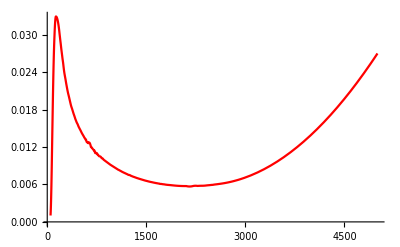
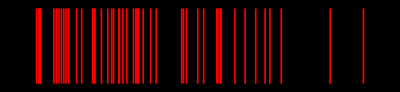
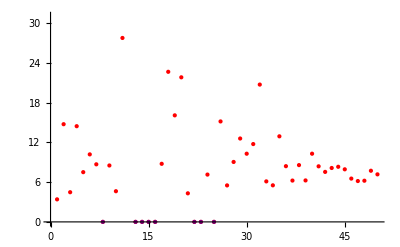
{{channl=175,Energy=59.6387,Fwhm=3.40456,NPA=15276.}
-Graphics-
 | G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI
59.6387 | True | {Am-241} | {True} | 213.969 | 175 | 3.40456 | {165, 184}
74.9675 | False | -- | -- | -- | 220 | 14.7546 | {210, 224}
77.352 | False | -- | -- | -- | 227 | 4.48198 | {224, 231}
84.5054 | False | -- | -- | -- | 248 | 14.4533 | {244, 252}
87.5712 | True | {Cd-109} | {False} | 5.13027 | 257 | 7.5121 | {252, 261}
89.9556 | False | -- | -- | -- | 264 | 10.1973 | {261, 269}
186.357 | True | {U-235, Ra-226} | {True, False} | 6.58721 | 547 | 8.69627 | {538, 553}
204.411 | True | {U-235} | {True} | 0.591549 | 600 | Erorr | {593, 607}
223.827 | False | -- | -- | -- | 657 | 8.51947 | {654, 658}
241.881 | True | {Pb-214} | {True} | 12.402 | 710 | 4.63476 | {705, 718}
259.254 | True | {Pa-234m} | {False} | 1.86203 | 761 | 27.7794 | {753, 771}
274.923 | True | {Cs-136, Ba-133} | {False, False} | 0.394481 | 807 | 48.7486 | {797, 809}
295.361 | True | {Pb-214, Au-194, Xe-139} | {True, False, True} | 32.2203 | 867 | Erorr | {859, 877}
351.908 | True | {Pb-214} | {True} | 61.8326 | 1033 | Erorr | {1023, 1040}
389.378 | False | -- | -- | -- | 1143 | Erorr | {1137, 1152}
469.088 | False | -- | -- | -- | 1377 | Erorr | {1368, 1382}
480.329 | False | -- | -- | -- | 1410 | 8.77298 | {1406, 1413}
487.142 | False | -- | -- | -- | 1430 | 22.6688 | {1420, 1433}
533.809 | False | -- | -- | -- | 1567 | 16.0919 | {1561, 1573}
580.136 | False | -- | -- | -- | 1703 | 21.8354 | {1693, 1709}
609.091 | True | {Bi-214} | {True} | 71.6779 | 1788 | 4.31585 | {1778, 1798}
622.376 | False | -- | -- | -- | 1827 | Erorr | {1820, 1828}
661.209 | True | {Cs-137} | {True} | 50.595 | 1941 | Erorr | {1931, 1947}
664.956 | False | -- | -- | -- | 1952 | 7.14635 | {1947, 1960}
690.504 | False | -- | -- | -- | 2027 | Erorr | {2026, 2028}
719.458 | False | -- | -- | -- | 2112 | 15.1732 | {2103, 2120}
768.17 | True | {Zn-65, Pa-234m} | {False, False} | 8.10734 | 2255 | 5.51186 | {2245, 2264}
785.542 | True | {Pb-214, Pa-234m} | {True, False} | 2.42456 | 2306 | 9.0541 | {2299, 2316}
795.08 | True | {Cs-134} | {True} | 0.501527 | 2334 | 12.594 | {2328, 2339}
805.64 | True | {Ag-99} | {False} | 2.54244 | 2365 | 10.2983 | {2357, 2375}
838.682 | False | -- | -- | -- | 2462 | 11.7554 | {2453, 2470}
893.866 | False | -- | -- | -- | 2624 | 20.7396 | {2617, 2631}
933.721 | False | -- | -- | -- | 2741 | 6.11852 | {2731, 2747}
1120.05 | True | {Bi-214} | {True} | 24.9387 | 3288 | 5.52403 | {3278, 3296}
1133. | False | -- | -- | -- | 3326 | 12.9242 | {3319, 3332}
1155.14 | False | -- | -- | -- | 3391 | 8.41531 | {3383, 3401}
1237.57 | True | {Bi-214, Cs-136} | {True, False} | 9.47725 | 3633 | 6.24278 | {3627, 3643}
1280.49 | False | -- | -- | -- | 3759 | 8.57629 | {3750, 3769}
1377.23 | False | -- | -- | -- | 4043 | 6.26235 | {4033, 4053}
1385.07 | True | {Y-88} | {False} | 1.89004 | 4066 | 10.2993 | {4056, 4072}
1401.42 | False | -- | -- | -- | 4114 | 8.39314 | {4104, 4124}
1407.89 | False | -- | -- | -- | 4133 | 7.55101 | {4123, 4143}
1509.06 | False | -- | -- | -- | 4430 | 8.14247 | {4423, 4440}
1583.32 | False | -- | -- | -- | 4648 | 8.32475 | {4641, 4657}
1660.99 | False | -- | -- | -- | 4876 | 7.94111 | {4867, 4883}
1729.46 | False | -- | -- | -- | 5077 | 6.54162 | {5067, 5087}
1764.54 | True | {Bi-214} | {True} | 25.8327 | 5180 | 6.17045 | {5170, 5190}
1847.66 | True | {Bi-203} | {False} | 3.16738 | 5424 | 6.21983 | {5414, 5434}
2204.99 | True | {Bi-214} | {True} | 6.79715 | 6473 | 7.72435 | {6463, 6482}
2448.21 | False | -- | -- | -- | 7187 | 7.17989 | {7177, 7197},Am-241
-Graphics-
 | Statistic | P-Value
Anderson-Darling | 3.26545 | 2.9065×10^-7
Baringhaus-Henze | 2.3741 | 0.000128622
Cramér-von Mises | 0.626803 | 0.
Jarque-Bera ALM | 23.3939 | 0.00675482
Mardia Combined | 23.3939 | 0.00675482
Mardia Kurtosis | 1.75528 | 0.0792107
Mardia Skewness | 11.1601 | 0.000835736
Pearson χ^2 | 27.6 | 0.0000150313
Shapiro-Wilk | 0.634369 | 6.82973×10^-6
-Graphics-
-Graphics-}

```mathematica
c=1;
{Column[{{ "channl="<>ToString[β2[[;;,1]][[c]]],"Energy="<>ToString[fchanll[β2[[;;,1]][[c]]]],"Fwhm="<>ToString[fw[[c]]],"NPA="<>ToString[NPA[β2[[;;,1]][[c]]]]},a11,tab12}],Column[{name[1],Plot[eff[u],{u,50,5000},PlotStyle->Red],αα3[[1]],Graphics[{Red,Thickness[0.003],Line[{{#,-1},{#,1}}]&/@β2[[;;,1]]},Frame->False,Background->Black,AspectRatio->3/(8GoldenRatio)],ListPlot[fw/.u_?StringQ->0,PlotStyle->{Red,PointSize[Medium]}]}]}
```

```mathematica
c=.
```

```mathematica
ξ=.
```

```mathematica
name[3]
```

Knwon

```mathematica
Select[]
```

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

Select[]

```mathematica
Text[Style[bb[[1,2]],Large,Bold,Red]]
```

Am-241

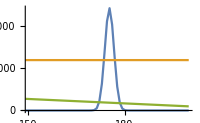
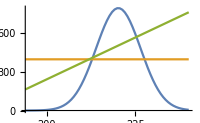
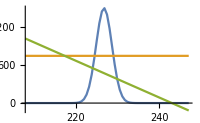
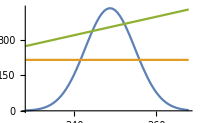
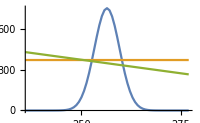
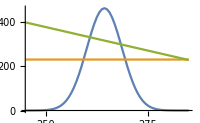
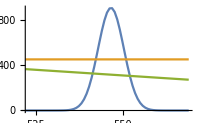
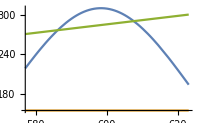
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
αα2
```

```mathematica
f
```

f

```mathematica
q={fchanll/@β2[[;;,1]],NPA/@β2[[;;,1]]}//Transpose
```

{{59.6387,15276.},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.},{204.411,291.5},{223.827,126.},{241.881,5430.},{259.254,768.},{274.923,156.5},{295.361,12083.},{351.908,20294.},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5},{622.376,53.5},{661.209,10502.5},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.},{795.08,91.},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5},{1133.,79},{1155.14,445.},{1237.57,1231.5},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5},{1847.66,323.5},{2203.97,695.5},{2204.99,674.},{2448.21,235}}

```mathematica
bbb
```

{{True},--,--,--,{False},--,{True,True},{True},--,{True},{False},{False,False},{True,False,False},{True},--,--,--,--,--,--,{True},--,{True},--,--,--,{False,False},{True,False},{False},{False},--,--,--,{True},--,--,{True,False},--,--,{False},{False},--,--,--,--,--,--,{True},{False},{True},{True},--}

```mathematica
B=Table[If[A[H[[;;,1]][[ii]]],H[[ii,3;;]],"--"],{ii,Length[H[[;;,1]]]}];
CC=Table[If[A[H[[;;,1]][[ii]]],H[[ii,3;;]],"--"],{ii,Length[H[[;;,1]]]}];
```

```mathematica
Activc1
```

{213.969,--,--,--,--,--,6.58721,--,--,12.402,--,--,32.2203,61.8326,--,--,--,--,--,--,71.6779,--,50.595,--,--,--,8.10734,--,0.501527,2.54244,--,--,--,24.9387,--,--,--,--,--,--,--,--,--,--,--,--,--,25.8327,--,--,--,--}

```mathematica
r=;
```

```mathematica
eff:=Interpolation[r,InterpolationOrder->2]
```

```mathematica
eff
```

InterpolatingFunction[…]

```mathematica
Plot[eff[u],{u,50,5000},PlotStyle->Red]
```

-Graphics-

```mathematica
NPA[175]
```

15276.

```mathematica
bbb=Table[If[u=={},"--",(Or@@eFil[#])&/@u],{u,H[[;;,3;;]]}]
```

{{True},--,--,--,{False},--,{True,True},{True},--,{True},{False},{False,False},{True,False,False},{True},--,--,--,--,--,--,{True},--,{True},--,--,--,{False,False},{True,False},{False},{False},--,--,--,{True},--,--,{True,False},--,--,{False},{False},--,--,--,--,--,--,{True},{False},{True},{True},--}

```mathematica
o
```

{{{59.6387,15276.,Am-241}},{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1237.57,1231.5,Bi-214},{1764.54,2687.5,Bi-214},{2203.97,695.5,Bi-214},{2204.99,674.,Bi-214}},{{661.209,10502.5,Cs-137}},{{241.881,5430.,Pb-214},{295.361,12083.,Pb-214},{351.908,20294.,Pb-214},{785.542,441.,Pb-214}},{{186.357,3433.,U-235,Ra-226}},{{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235}}}

```mathematica
ξ=.
```

```mathematica
Activc2[c_]:=Module[{τ=24*3600,wight=0.2,ξ,ee,ξ2},
If[MemberQ[bb[[;;,1,1]],β2[[;;,1]][[c]]],
ξ=Position[bb[[;;,1,1]],β2[[;;,1]][[c]]][[1,1]];
ξ2=Position[o,bb[[;;,2]][[ξ]]][[1,1]];
ee=A/@o[[ξ2,;;,1]];
Acti:=Table[If[ee[[i]],(o[[ξ2,;;,2]][[i]])/(eff[o[[ξ2,;;,1]][[i]]]*τ*wight),"--"] ,{i,Length[ee]}];Acti,"--"]]
```

```mathematica
Activc[7]
```

{6.58721}

```mathematica
A/@o[[;;,;;,1]]
```

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

Between::pair: Argument {0,2.47877,2.47877} is expected to be a pair, a list of pairs or an Interval object.

Between::pair: Argument {0,2.4981,2.4981} is expected to be a pair, a list of pairs or an Interval object.

{True,False,True,False,True,False}

```mathematica
o[[2,;;,1]]
```

{609.091,1120.05,1237.57,1764.54,2203.97,2204.99}

```mathematica
bbb
```

{{True},--,--,--,{False},--,{True,True},{True},--,{True},{False},{False,False},{True,False,False},{True},--,--,--,--,--,--,{True},--,{True},--,--,--,{False,False},{True,False},{False},{False},--,--,--,{True},--,--,{True,False},--,--,{False},{False},--,--,--,--,--,--,{True},{False},{True},{True},--}

```mathematica
/
```

```mathematica
ToString/@(Roi/@β2[[;;,1]])
```

{{165, 184},{210, 224},{224, 231},{244, 252},{252, 261},{261, 269},{538, 553},{593, 607},{654, 658},{705, 718},{753, 771},{797, 809},{859, 877},{1023, 1040},{1137, 1152},{1368, 1382},{1406, 1413},{1420, 1433},{1561, 1573},{1693, 1709},{1778, 1798},{1820, 1828},{1931, 1947},{1947, 1960},{2026, 2028},{2103, 2120},{2245, 2264},{2299, 2316},{2328, 2339},{2357, 2375},{2453, 2470},{2617, 2631},{2731, 2747},{3278, 3296},{3319, 3332},{3383, 3401},{3627, 3643},{3750, 3769},{4033, 4053},{4056, 4072},{4056, 4072},{4104, 4124},{4123, 4143},{4423, 4440},{4641, 4657},{4867, 4883},{5067, 5087},{5170, 5190},{5414, 5434},{6460, 6480},{6463, 6482},{7177, 7197}}

```mathematica
tab1[34]
```

| G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI
609.091 | True | {Bi-214} | {True} | 71.6779 | 1788 | If[Abs[Subtract[1788]] <= 3, Erorr, Erorr] | {1778, 1798}
1120.05 | True | {Bi-214} | {True} | 24.9387 | 3288 | If[Abs[Subtract[3288]] <= 3, Erorr, Erorr] | {3278, 3296}
1237.57 | False | {Bi-214} | {True} | -- | 3633 | If[Abs[Subtract[3633]] <= 3, Erorr, Erorr] | {3627, 3643}
1764.54 | True | {Bi-214} | {True} | 25.8327 | 5180 | If[Abs[Subtract[5180]] <= 3, Erorr, Erorr] | {5170, 5190}
2203.97 | False | {Bi-214} | {True} | -- | 6470 | If[Abs[Subtract[6470]] <= 3, Erorr, Erorr] | {6460, 6480}
2204.99 | False | {Bi-214} | {True} | -- | 6473 | If[Abs[Subtract[6473]] <= 3, Erorr, Erorr] | {6463, 6482}

```mathematica
tab11[[34]]
```

| G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI
609.091 | True | {Bi-214} | {True} | 71.6779 | 1788 | If[Abs[Subtract[1788]] <= 3, Erorr, Erorr] | {1778, 1798}
1120.05 | True | {Bi-214} | {True} | 24.9387 | 3288 | If[Abs[Subtract[3288]] <= 3, Erorr, Erorr] | {3278, 3296}
1237.57 | False | {Bi-214} | {True} | -- | 3633 | If[Abs[Subtract[3633]] <= 3, Erorr, Erorr] | {3627, 3643}
1764.54 | True | {Bi-214} | {True} | 25.8327 | 5180 | If[Abs[Subtract[5180]] <= 3, Erorr, Erorr] | {5170, 5190}
2203.97 | False | {Bi-214} | {True} | -- | 6470 | If[Abs[Subtract[6470]] <= 3, Erorr, Erorr] | {6460, 6480}
2204.99 | False | {Bi-214} | {True} | -- | 6473 | If[Abs[Subtract[6473]] <= 3, Erorr, Erorr] | {6463, 6482}

```mathematica
MemberQ[bb[[;;,1,1]],β2[[;;,1]][[37]]]
```

True

```mathematica
A[g_]:=Or@@Table[G[i,g]&&T[i,6,g],{i,1,100,3}]
```

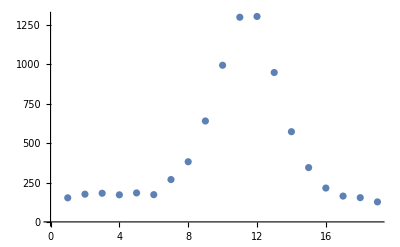

```mathematica
ListPlot[{153.,176.,182.,172.,184.,173.,269.,382.,641.,995.,1300.,1305.,949.,573.,345.,215.,164.,154.,127.}]
```

```mathematica
Total[%86]
```

| Statistic | P-Value
Anderson-Darling | 0.643724 | 0.0883023
Baringhaus-Henze | 0.306354 | 0.0892076
Cramér-von Mises | 0.0890035 | 0.156879
Mardia Combined | 9.86063 | 0.958923
Mardia Kurtosis | 0.63405 | 0.526048
Mardia Skewness | 2.57659 | 0.108455
Pearson χ^2 | 0.444444 | 0.800737
Shapiro-Wilk | 0.820594 | 0.0339047+ | Statistic | P-Value
Anderson-Darling | 0.166314 | 0.956631
Baringhaus-Henze | 0.0168904 | 0.997754
Cramér-von Mises | 0.0237509 | 0.938031
Jarque-Bera ALM | 0.205038 | 0.903497
Mardia Combined | 0.205038 | 0.903497
Mardia Kurtosis | -0.273343 | 0.784589
Mardia Skewness | 0.145149 | 0.703215
Pearson χ^2 | 2.35294 | 0.671148
Shapiro-Wilk | 0.980404 | 0.960689+ | Statistic | P-Value
Anderson-Darling | 0.196213 | 0.901169
Baringhaus-Henze | 0.016879 | 0.995978
Cramér-von Mises | 0.0237507 | 0.938034
Jarque-Bera ALM | 0.337532 | 0.844199
Mardia Combined | 0.337532 | 0.844199
Mardia Kurtosis | -0.620026 | 0.53524
Mardia Skewness | 0.0356177 | 0.850307
Pearson χ^2 | 1.30769 | 0.727307
Shapiro-Wilk | 0.96856 | 0.876522+ | Statistic | P-Value
Anderson-Darling | 0.286527 | 0.666298
Baringhaus-Henze | 0.0165095 | 0.940992
Kolmogorov-Smirnov | 0.262027 | 0.889478
Kuiper | 0.354206 | 0.112419
Mardia Combined | Indeterminate | Indeterminate
Mardia Kurtosis | -0.53033 | 0.595883
Mardia Skewness | 0.0605428 | 0.80564
Pearson χ^2 | 1. | 0.317311
Watson U^2 | 0.0424064 | 0.883828+ | Statistic | P-Value
Anderson-Darling | 0.413473 | 0.338029
Baringhaus-Henze | 0.184206 | 0.346026
Cramér-von Mises | 0.0506842 | 0.507777
Jarque-Bera ALM | 4.91006 | 0.0863816
Mardia Combined | 4.91006 | 0.0863816
Mardia Kurtosis | 0.499632 | 0.617334
Mardia Skewness | 2.19782 | 0.138206
Pearson χ^2 | 3. | 0.391625
Shapiro-Wilk | 0.910677 | 0.138685+ | Statistic | P-Value
Anderson-Darling | 0.431283 | 0.306326
Baringhaus-Henze | 0.233247 | 0.261276
Cramér-von Mises | 0.0649701 | 0.331818
Jarque-Bera ALM | 1.6483 | 0.301162
Mardia Combined | 1.6483 | 0.301162
Mardia Kurtosis | -1.0357 | 0.300342
Mardia Skewness | 0.218701 | 0.640032
Pearson χ^2 | 3.17647 | 0.52874
Shapiro-Wilk | 0.930185 | 0.219199+ | Statistic | P-Value
Anderson-Darling | 0.442283 | 0.288007
Baringhaus-Henze | 0.231182 | 0.275239
Cramér-von Mises | 0.0777899 | 0.222878
Jarque-Bera ALM | 1.39159 | 0.377047
Mardia Combined | 1.39159 | 0.377047
Mardia Kurtosis | -0.482897 | 0.629169
Mardia Skewness | 0.933474 | 0.333962
Pearson χ^2 | 4.55556 | 0.336011
Shapiro-Wilk | 0.945911 | 0.364518+ | Statistic | P-Value
Anderson-Darling | 0.509615 | 0.19565
Baringhaus-Henze | 0.210573 | 0.270742
Cramér-von Mises | 0.0745717 | 0.246049
Jarque-Bera ALM | 1.54552 | 0.330165
Mardia Combined | 1.54552 | 0.330165
Mardia Kurtosis | -0.0416431 | 0.966783
Mardia Skewness | 0.889379 | 0.345646
Pearson χ^2 | 4.85714 | 0.182562
Shapiro-Wilk | 0.925253 | 0.261462+ | Statistic | P-Value
Anderson-Darling | 0.551569 | 0.15322
Baringhaus-Henze | 0.28765 | 0.134846
Cramér-von Mises | 0.102936 | 0.101467
Jarque-Bera ALM | 2.66646 | 0.161129
Mardia Combined | 2.66646 | 0.161129
Mardia Kurtosis | 0.0421419 | 0.966386
Mardia Skewness | 1.36303 | 0.243013
Pearson χ^2 | 6. | 0.11161
Shapiro-Wilk | 0.916537 | 0.258517+ | Statistic | P-Value
Anderson-Darling | 0.564519 | 0.142976
Baringhaus-Henze | 0.343001 | 0.112141
Cramér-von Mises | 0.0951217 | 0.129764
Jarque-Bera ALM | 2.57815 | 0.168039
Mardia Combined | 2.57815 | 0.168039
Mardia Kurtosis | 0.03894 | 0.968938
Mardia Skewness | 1.54563 | 0.213782
Pearson χ^2 | 1.4 | 0.705535
Shapiro-Wilk | 0.923527 | 0.217977+ | Statistic | P-Value
Anderson-Darling | 0.606392 | 0.111373
Baringhaus-Henze | 0.358227 | 0.0953832
Cramér-von Mises | 0.0975173 | 0.120393
Jarque-Bera ALM | 2.03412 | 0.22941
Mardia Combined | 2.03412 | 0.22941
Mardia Kurtosis | -0.565166 | 0.571961
Mardia Skewness | 1.21535 | 0.270275
Pearson χ^2 | 4.85714 | 0.182562
Shapiro-Wilk | 0.896535 | 0.100462+ | Statistic | P-Value
Anderson-Darling | 0.611902 | 0.107865
Baringhaus-Henze | 0.39465 | 0.0755756
Cramér-von Mises | 0.0886465 | 0.158625
Jarque-Bera ALM | 2.73905 | 0.154677
Mardia Combined | 2.73905 | 0.154677
Mardia Kurtosis | -0.27045 | 0.786814
Mardia Skewness | 1.80228 | 0.179438
Pearson χ^2 | 1.42857 | 0.698851
Shapiro-Wilk | 0.884017 | 0.0663214+ | Statistic | P-Value
Anderson-Darling | 0.623582 | 0.101142
Baringhaus-Henze | 0.43672 | 0.0666622
Cramér-von Mises | 0.109108 | 0.0836312
Jarque-Bera ALM | 2.01463 | 0.233987
Mardia Combined | 2.01463 | 0.233987
Mardia Kurtosis | -0.683588 | 0.494236
Mardia Skewness | 1.12879 | 0.288034
Pearson χ^2 | 4.125 | 0.389353
Shapiro-Wilk | 0.909553 | 0.114455+ | Statistic | P-Value
Anderson-Darling | 0.647716 | 0.0874055
Baringhaus-Henze | 0.421756 | 0.0592773
Cramér-von Mises | 0.112334 | 0.0757115
Jarque-Bera ALM | 3.64286 | 0.117746
Mardia Combined | 3.64286 | 0.117746
Mardia Kurtosis | 0.0263696 | 0.978963
Mardia Skewness | 2.09913 | 0.147383
Pearson χ^2 | 3.15385 | 0.368508
Shapiro-Wilk | 0.893048 | 0.107377+2  | Statistic | P-Value
Anderson-Darling | 0.775531 | 0.0417183
Baringhaus-Henze | 0.519742 | 0.0444021
Cramér-von Mises | 0.140876 | 0.0307329
Jarque-Bera ALM | 2.05058 | 0.22803
Mardia Combined | 2.05058 | 0.22803
Mardia Kurtosis | -0.842607 | 0.399448
Mardia Skewness | 0.926849 | 0.335683
Pearson χ^2 | 8.94118 | 0.0625867
Shapiro-Wilk | 0.90232 | 0.0742809+ | Statistic | P-Value
Anderson-Darling | 0.797342 | 0.0366152
Baringhaus-Henze | 0.557952 | 0.031705
Cramér-von Mises | 0.132434 | 0.0401673
Jarque-Bera ALM | 20.5487 | 0.00835282
Mardia Combined | 20.5487 | 0.00835282
Mardia Kurtosis | 1.84101 | 0.0656195
Mardia Skewness | 5.79088 | 0.0161095
Pearson χ^2 | 7. | 0.0718978
Shapiro-Wilk | 0.849866 | 0.0172901+ | Statistic | P-Value
Anderson-Darling | 0.9036 | 0.0198498
Baringhaus-Henze | 0.583628 | 0.0337443
Cramér-von Mises | 0.145851 | 0.026478
Jarque-Bera ALM | 2.75247 | 0.152449
Mardia Combined | 2.75247 | 0.152449
Mardia Kurtosis | -0.543049 | 0.587096
Mardia Skewness | 1.86913 | 0.171574
Pearson χ^2 | 8.44444 | 0.0765892
Shapiro-Wilk | 0.876269 | 0.0226049+ | Statistic | P-Value
Anderson-Darling | 0.911102 | 0.0189911
Baringhaus-Henze | 0.602553 | 0.0306838
Cramér-von Mises | 0.15374 | 0.0207622
Jarque-Bera ALM | 2.66395 | 0.160213
Mardia Combined | 2.66395 | 0.160213
Mardia Kurtosis | -0.67951 | 0.496815
Mardia Skewness | 1.65603 | 0.198141
Pearson χ^2 | 10.7778 | 0.0291783
Shapiro-Wilk | 0.874818 | 0.0213806+ | Statistic | P-Value
Anderson-Darling | 0.954447 | 0.0147572
Baringhaus-Henze | 0.769944 | 0.0149102
Cramér-von Mises | 0.179136 | 0.009333
Jarque-Bera ALM | 5.34413 | 0.0772848
Mardia Combined | 5.34413 | 0.0772848
Mardia Kurtosis | 0.424434 | 0.67125
Mardia Skewness | 3.16837 | 0.0750771
Pearson χ^2 | 7.15789 | 0.127776
Shapiro-Wilk | 0.893728 | 0.0375176+ | Statistic | P-Value
Anderson-Darling | 0.95886 | 0.0144166
Baringhaus-Henze | 0.642185 | 0.0297216
Cramér-von Mises | 0.153694 | 0.0207924
Jarque-Bera ALM | 3.40796 | 0.123555
Mardia Combined | 3.40796 | 0.123555
Mardia Kurtosis | -0.351849 | 0.724951
Mardia Skewness | 2.56117 | 0.109518
Pearson χ^2 | 14.6667 | 0.00544493
Shapiro-Wilk | 0.871192 | 0.0100684+ | Statistic | P-Value
Anderson-Darling | 0.983883 | 0.0123379
Baringhaus-Henze | 0.650707 | 0.0242439
Cramér-von Mises | 0.171019 | 0.0120141
Jarque-Bera ALM | 2.59538 | 0.166228
Mardia Combined | 2.59538 | 0.166228
Mardia Kurtosis | -0.957753 | 0.338187
Mardia Skewness | 1.11552 | 0.290885
Pearson χ^2 | 9.22222 | 0.0557787
Shapiro-Wilk | 0.870004 | 0.0177953+ | Statistic | P-Value
Anderson-Darling | 1.09377 | 0.00650439
Baringhaus-Henze | 0.675251 | 0.0202415
Cramér-von Mises | 0.182321 | 0.00844584
Jarque-Bera ALM | 2.75014 | 0.152927
Mardia Combined | 2.75014 | 0.152927
Mardia Kurtosis | -1.03914 | 0.298741
Mardia Skewness | 0.990517 | 0.319616
Pearson χ^2 | 14.7059 | 0.00535177
Shapiro-Wilk | 0.845074 | 0.00902889+ | Statistic | P-Value
Anderson-Darling | 1.09858 | 0.00636087
Baringhaus-Henze | 0.851916 | 0.0117979
Cramér-von Mises | 0.19697 | 0.00535424
Jarque-Bera ALM | 3.44004 | 0.122199
Mardia Combined | 3.44004 | 0.122199
Mardia Kurtosis | -0.434034 | 0.664263
Mardia Skewness | 2.55113 | 0.110215
Pearson χ^2 | 11.3333 | 0.0230625
Shapiro-Wilk | 0.875774 | 0.0122062+ | Statistic | P-Value
Anderson-Darling | 1.1231 | 0.00549342
Baringhaus-Henze | 0.618672 | 0.0316422
Cramér-von Mises | 0.166553 | 0.0137935
Jarque-Bera ALM | 2.82673 | 0.147772
Mardia Combined | 2.82673 | 0.147772
Mardia Kurtosis | -1.24796 | 0.212046
Mardia Skewness | 0.602223 | 0.437731
Pearson χ^2 | 22. | 0.00020042
Shapiro-Wilk | 0.85108 | 0.00555741+ | Statistic | P-Value
Anderson-Darling | 1.13911 | 0.00500639
Baringhaus-Henze | 0.595992 | 0.0335491
Cramér-von Mises | 0.20391 | 0.00433485
Jarque-Bera ALM | 2.69784 | 0.15702
Mardia Combined | 2.69784 | 0.15702
Mardia Kurtosis | -0.614182 | 0.539095
Mardia Skewness | 1.79006 | 0.180919
Pearson χ^2 | 14.5263 | 0.00579157
Shapiro-Wilk | 0.860162 | 0.00986088+ | Statistic | P-Value
Anderson-Darling | 1.15293 | 0.00463591
Baringhaus-Henze | 0.95689 | 0.00733974
Cramér-von Mises | 0.191507 | 0.00633965
Jarque-Bera ALM | 3.59007 | 0.115755
Mardia Combined | 3.59007 | 0.115755
Mardia Kurtosis | -0.567059 | 0.570674
Mardia Skewness | 2.53101 | 0.111628
Pearson χ^2 | 10.8 | 0.0289061
Shapiro-Wilk | 0.859824 | 0.00782186+ | Statistic | P-Value
Anderson-Darling | 1.15825 | 0.00449149
Baringhaus-Henze | 1.00072 | 0.00583448
Cramér-von Mises | 0.200674 | 0.00478173
Jarque-Bera ALM | 7.36262 | 0.0487579
Mardia Combined | 7.36262 | 0.0487579
Mardia Kurtosis | 0.397986 | 0.69064
Mardia Skewness | 4.70677 | 0.0300441
Pearson χ^2 | 11.5789 | 0.020773
Shapiro-Wilk | 0.845221 | 0.00561439+ | Statistic | P-Value
Anderson-Darling | 1.21977 | 0.00310274
Baringhaus-Henze | 0.780356 | 0.0125262
Cramér-von Mises | 0.239516 | 0.00150872
Jarque-Bera ALM | 4.86962 | 0.0861255
Mardia Combined | 4.86962 | 0.0861255
Mardia Kurtosis | 0.0848095 | 0.932413
Mardia Skewness | 3.22722 | 0.0724235
Pearson χ^2 | 8.94118 | 0.0625867
Shapiro-Wilk | 0.848385 | 0.0101341+ | Statistic | P-Value
Anderson-Darling | 1.31671 | 0.0017357
Baringhaus-Henze | 0.757251 | 0.0176115
Cramér-von Mises | 0.201545 | 0.00465677
Jarque-Bera ALM | 3.0429 | 0.138981
Mardia Combined | 3.0429 | 0.138981
Mardia Kurtosis | -1.22333 | 0.221205
Mardia Skewness | 0.880901 | 0.347955
Pearson χ^2 | 24.6667 | 0.0000587003
Shapiro-Wilk | 0.837847 | 0.00264177+ | Statistic | P-Value
Anderson-Darling | 1.4484 | 0.000845337
Baringhaus-Henze | 1.14086 | 0.00396481
Cramér-von Mises | 0.271769 | 0.000588507
Jarque-Bera ALM | 4.07234 | 0.0981858
Mardia Combined | 4.07234 | 0.0981858
Mardia Kurtosis | -0.438926 | 0.660715
Mardia Skewness | 3.02627 | 0.0819262
Pearson χ^2 | 15.3333 | 0.00405752
Shapiro-Wilk | 0.845326 | 0.00353263+ | Statistic | P-Value
Anderson-Darling | 1.46382 | 0.000777087
Baringhaus-Henze | 1.15776 | 0.00373926
Cramér-von Mises | 0.237495 | 0.00159912
Jarque-Bera ALM | 5.57871 | 0.072637
Mardia Combined | 5.57871 | 0.072637
Mardia Kurtosis | -0.0950459 | 0.924278
Mardia Skewness | 4.17696 | 0.0409771
Pearson χ^2 | 18.6667 | 0.000913746
Shapiro-Wilk | 0.819731 | 0.00133521+ | Statistic | P-Value
Anderson-Darling | 1.6069 | 0.000358015
Baringhaus-Henze | 1.2423 | 0.00280966
Cramér-von Mises | 0.277619 | 0.000486228
Jarque-Bera ALM | 3.79361 | 0.107258
Mardia Combined | 3.79361 | 0.107258
Mardia Kurtosis | -0.85403 | 0.393088
Mardia Skewness | 2.32397 | 0.127395
Pearson χ^2 | 22.6667 | 0.000147597
Shapiro-Wilk | 0.812923 | 0.00104101+ | Statistic | P-Value
Anderson-Darling | 1.64221 | 0.000294541
Baringhaus-Henze | 1.06332 | 0.00462176
Cramér-von Mises | 0.276295 | 0.000507922
Jarque-Bera ALM | 3.68427 | 0.112427
Mardia Combined | 3.68427 | 0.112427
Mardia Kurtosis | -0.727202 | 0.467102
Mardia Skewness | 2.37008 | 0.123681
Pearson χ^2 | 20.4211 | 0.000412336
Shapiro-Wilk | 0.792137 | 0.000880555+ | Statistic | P-Value
Anderson-Darling | 1.66144 | 0.000263712
Baringhaus-Henze | 1.16806 | 0.00360889
Cramér-von Mises | 0.286879 | 0.000358792
Jarque-Bera ALM | 3.77223 | 0.108162
Mardia Combined | 3.77223 | 0.108162
Mardia Kurtosis | -0.796809 | 0.425562
Mardia Skewness | 2.40657 | 0.120827
Pearson χ^2 | 24. | 0.0000798748
Shapiro-Wilk | 0.809277 | 0.000912595+ | Statistic | P-Value
Anderson-Darling | 1.74243 | 0.000163291
Baringhaus-Henze | 1.18925 | 0.00335688
Cramér-von Mises | 0.319676 | 0.000134175
Jarque-Bera ALM | 5.28454 | 0.0776264
Mardia Combined | 5.28454 | 0.0776264
Mardia Kurtosis | -0.152514 | 0.878782
Mardia Skewness | 3.9775 | 0.0461119
Pearson χ^2 | 22.6667 | 0.000147597
Shapiro-Wilk | 0.806758 | 0.000833774+ | Statistic | P-Value
Anderson-Darling | 1.7955 | 0.000116679
Baringhaus-Henze | 1.10583 | 0.00343807
Cramér-von Mises | 0.319244 | 0.000135902
Jarque-Bera ALM | 4.4851 | 0.0924437
Mardia Combined | 4.4851 | 0.0924437
Mardia Kurtosis | -0.356972 | 0.721113
Mardia Skewness | 3.16722 | 0.07513
Pearson χ^2 | 26.2353 | 0.0000283688
Shapiro-Wilk | 0.758034 | 0.000569934+ | Statistic | P-Value
Anderson-Darling | 2.45172 | 5.14566×10^-7
Baringhaus-Henze | 1.55071 | 0.000880689
Cramér-von Mises | 0.453598 | 3.82623×10^-6
Jarque-Bera ALM | 8.11476 | 0.0462573
Mardia Combined | 8.11476 | 0.0462573
Mardia Kurtosis | 0.248337 | 0.803873
Mardia Skewness | 5.41656 | 0.0199467
Pearson χ^2 | 27.1111 | 0.0000188767
Shapiro-Wilk | 0.699449 | 0.0000786849+ | Statistic | P-Value
Anderson-Darling | 2.81158 | 0.
Baringhaus-Henze | 1.83984 | 0.000428115
Cramér-von Mises | 0.524554 | 1.16104×10^-6
Jarque-Bera ALM | 11.0532 | 0.036003
Mardia Combined | 11.0532 | 0.036003
Mardia Kurtosis | 0.608776 | 0.542673
Mardia Skewness | 6.90323 | 0.008604
Pearson χ^2 | 24.1053 | 0.0000760863
Shapiro-Wilk | 0.671376 | 0.0000258456+ | Statistic | P-Value
Anderson-Darling | 2.90049 | 0.
Baringhaus-Henze | 1.95903 | 0.00036291
Cramér-von Mises | 0.542075 | 6.96132×10^-7
Jarque-Bera ALM | 8.81007 | 0.0434888
Mardia Combined | 8.81007 | 0.0434888
Mardia Kurtosis | 0.246019 | 0.805668
Mardia Skewness | 6.27759 | 0.0122274
Pearson χ^2 | 34.6667 | 5.43839×10^-7
Shapiro-Wilk | 0.69495 | 0.0000238335+ | Statistic | P-Value
Anderson-Darling | 3.26545 | 2.9065×10^-7
Baringhaus-Henze | 2.3741 | 0.000128622
Cramér-von Mises | 0.626803 | 0.
Jarque-Bera ALM | 23.3939 | 0.00675482
Mardia Combined | 23.3939 | 0.00675482
Mardia Kurtosis | 1.75528 | 0.0792107
Mardia Skewness | 11.1601 | 0.000835736
Pearson χ^2 | 27.6 | 0.0000150313
Shapiro-Wilk | 0.634369 | 6.82973×10^-6+ | Statistic | P-Value
Anderson-Darling | 0.300809 | 0.605814
Baringhaus-Henze | 0.0410717 | 0.795135
Kolmogorov-Smirnov | 0.258101 | 0.458096
Kuiper | 0.30072 | 0.248268
Mardia Combined | 1.23744 | 0.568438
Mardia Kurtosis | -0.306771 | 0.759018
Mardia Skewness | 0.252303 | 0.615458
Pearson χ^2 | 0.6 | 0.438578
Shapiro-Wilk | 0.942123 | 0.681392
Watson U^2 | 0.0443803 | 0.754762+ | Statistic | P-Value
Anderson-Darling | 0.243889 | 0.775769
Baringhaus-Henze | 0.0556632 | 0.80162
Cramér-von Mises | 0.0327309 | 0.805634
Kolmogorov-Smirnov | 0.145589 | 0.874545
Kuiper | 0.164692 | 0.807629
Mardia Combined | 1.05859 | 0.496715
Mardia Kurtosis | -0.827292 | 0.408072
Mardia Skewness | 0.00748277 | 0.931067
Pearson χ^2 | 1.55556 | 0.459426
Shapiro-Wilk | 0.946751 | 0.655611
Watson U^2 | 0.0326687 | 0.895628+ | Statistic | P-Value
Anderson-Darling | 0.259462 | 0.728664
Baringhaus-Henze | 0.0637964 | 0.749223
Cramér-von Mises | 0.0356964 | 0.753879
Kolmogorov-Smirnov | 0.169302 | 0.692247
Kuiper | 0.177729 | 0.74092
Mardia Combined | 0.995246 | 0.467843
Mardia Kurtosis | -0.781972 | 0.434231
Mardia Skewness | 0.0769667 | 0.781451
Pearson χ^2 | 1.55556 | 0.459426
Shapiro-Wilk | 0.945177 | 0.63836
Watson U^2 | 0.0350166 | 0.854322+ | Statistic | P-Value
Anderson-Darling | 0.264488 | 0.713874
Baringhaus-Henze | 0.00593738 | 0.999859
Cramér-von Mises | 0.0424718 | 0.636553
Kolmogorov-Smirnov | 0.171987 | 0.748741
Kuiper | 0.207164 | 0.594237
Mardia Combined | 0.0501075 | 0.0210834
Mardia Kurtosis | -0.434548 | 0.66389
Mardia Skewness | 0.0170846 | 0.896006
Pearson χ^2 | 7. | 0.0301974
Shapiro-Wilk | 0.958002 | 0.792314
Watson U^2 | 0.0424049 | 0.72365+ | Statistic | P-Value
Anderson-Darling | 0.346045 | 0.481969
Baringhaus-Henze | 0.106899 | 0.473559
Cramér-von Mises | 0.0559847 | 0.434736
Kolmogorov-Smirnov | 0.211216 | 0.425393
Kuiper | 0.214975 | 0.550367
Mardia Combined | 1.2269 | 0.564236
Mardia Kurtosis | -0.729153 | 0.465908
Mardia Skewness | 0.24822 | 0.618331
Pearson χ^2 | 0.75 | 0.687289
Shapiro-Wilk | 0.921833 | 0.444576
Watson U^2 | 0.0535713 | 0.509622+ | Statistic | P-Value
Anderson-Darling | 0.677517 | 0.072701
Baringhaus-Henze | 0.239963 | 0.165838
Cramér-von Mises | 0.115792 | 0.0679846
Jarque-Bera ALM | 2.09416 | 0.216289
Kolmogorov-Smirnov | 0.227893 | 0.178054
Kuiper | 0.3132 | 0.0953176
Mardia Combined | 2.09416 | 0.216289
Mardia Kurtosis | -0.983023 | 0.325596
Mardia Skewness | 0.233234 | 0.629136
Pearson χ^2 | 3.2 | 0.361805
Shapiro-Wilk | 0.859989 | 0.0743065
Watson U^2 | 0.113088 | 0.057123+ | Statistic | P-Value
Anderson-Darling | 0.986193 | 0.0120901
Baringhaus-Henze | 0.750941 | 0.0122972
Cramér-von Mises | 0.16947 | 0.0126015
Jarque-Bera ALM | 5.39113 | 0.0786139
Kolmogorov-Smirnov | 0.213553 | 0.0731994
Kuiper | 0.313108 | 0.0325623
Mardia Combined | 5.39113 | 0.0786139
Mardia Kurtosis | 0.114826 | 0.908583
Mardia Skewness | 3.34952 | 0.0672247
Pearson χ^2 | 11. | 0.0117259
Shapiro-Wilk | 0.838365 | 0.0119348
Watson U^2 | 0.146039 | 0.0180243+ | Statistic | P-Value
Anderson-Darling | 1.30279 | 0.00187218
Baringhaus-Henze | 0.811781 | 0.0109258
Cramér-von Mises | 0.216173 | 0.00299707
Jarque-Bera ALM | 3.05048 | 0.139241
Kolmogorov-Smirnov | 0.236612 | 0.0151904
Kuiper | 0.334599 | 0.00900728
Mardia Combined | 3.05048 | 0.139241
Mardia Kurtosis | -0.836414 | 0.402922
Mardia Skewness | 1.64663 | 0.199418
Pearson χ^2 | 18.8235 | 0.00085123
Shapiro-Wilk | 0.817802 | 0.00359656
Watson U^2 | 0.200043 | 0.00282456+ | Statistic | P-Value
Anderson-Darling | 1.45782 | 0.00080357
Baringhaus-Henze | 0.848594 | 0.00732675
Cramér-von Mises | 0.266043 | 0.000705384
Jarque-Bera ALM | 3.88651 | 0.107707
Kolmogorov-Smirnov | 0.278461 | 0.00639976
Kuiper | 0.419291 | 0.000900463
Mardia Combined | 3.88651 | 0.107707
Mardia Kurtosis | -0.36045 | 0.718511
Mardia Skewness | 2.55494 | 0.10995
Pearson χ^2 | 19.4286 | 0.000222914
Shapiro-Wilk | 0.768978 | 0.00211592
Watson U^2 | 0.243584 | 0.000781871+ | Statistic | P-Value
Anderson-Darling | 1.93003 | 0.0000430071
Baringhaus-Henze | 1.23641 | 0.00200902
Cramér-von Mises | 0.363978 | 0.0000341073
Jarque-Bera ALM | 8.61889 | 0.0447862
Kolmogorov-Smirnov | 0.331913 | 0.0000940404
Kuiper | 0.484101 | 0.0000281885
Mardia Combined | 8.61889 | 0.0447862
Mardia Kurtosis | 0.432528 | 0.665358
Mardia Skewness | 5.0857 | 0.024124
Pearson χ^2 | 17.25 | 0.00172827
Shapiro-Wilk | 0.734623 | 0.000417223
Watson U^2 | 0.328703 | 0.000136096+ | Statistic | P-Value
Anderson-Darling | 2.01357 | 0.0000233457
Baringhaus-Henze | 1.41038 | 0.00154428
Cramér-von Mises | 0.360884 | 0.0000380721
Jarque-Bera ALM | 5.55516 | 0.0732054
Kolmogorov-Smirnov | 0.277857 | 0.000429498
Kuiper | 0.427102 | 0.0000568605
Mardia Combined | 5.55516 | 0.0732054
Mardia Kurtosis | -0.224999 | 0.82198
Mardia Skewness | 4.13851 | 0.0419181
Pearson χ^2 | 24.8 | 0.0000551891
Shapiro-Wilk | 0.770564 | 0.000324669
Watson U^2 | 0.327023 | 0.00014688

```mathematica
N/@DistributionFitTest[x[[Roi[538][[1]];;Roi[538][[2]]]][[;;,2]],Automatic,"HypothesisTestData"]["TestDataTable",All]
```

DistributionFitTest::rctnln: The argument {335} at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

DistributionFitTest[{335},Automatic,HypothesisTestData][TestDataTable,All]

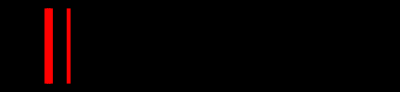

```mathematica
tabspect[[10]]
```

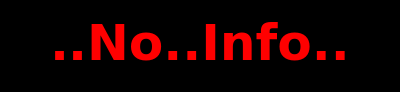

```mathematica
Graphics[{Red,Thickness[0.004],Text[Style["..No..Info..",50,Bold,Red]]},Frame->False,Background->Black,AspectRatio->3/(8GoldenRatio)]
```

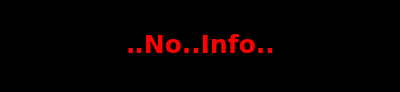

```mathematica
spect[6]
```

```mathematica
Table[spect[i],{i,Length[β2[[;;,1]]]}];
```

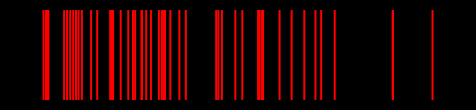

```mathematica
Graphics[{Red,Thickness[0.003],Line[{{#,-1},{#,1}}]&/@H[[;;,1]]},Frame->False,Background->Black,AspectRatio->3/(8GoldenRatio)]
```

```mathematica
H[[;;,1]]
```

{59.6387,74.9675,77.352,84.5054,87.5712,89.9556,186.357,204.411,223.827,241.881,259.254,274.923,295.361,351.908,389.378,469.088,480.329,487.142,533.809,580.136,609.091,622.376,661.209,664.956,690.504,719.458,768.17,785.542,795.08,805.64,838.682,893.866,933.721,1120.05,1133.,1155.14,1237.57,1280.49,1377.23,1385.07,1385.07,1401.42,1407.89,1509.06,1583.32,1660.99,1729.46,1764.54,1847.66,2203.97,2204.99,2448.21}

```mathematica
f[u_,ch_]:=Interpolation[x[[Roi[ch][[1]];;Roi[ch][[2]]]],InterpolationOrder->3][u]
```

```mathematica
f1[u_,ch_]:=Simplify[Normal@NonlinearModelFit[data,x[[ch]][[2]]*Exp[-b*(t-ch)^2],{b},t]]/.t->u
model[u_]:=a1 (Exp[-(b1(u-x1))^2])
f2[u_,ch_]:=model[u]/.FindFit[x[[Roi[ch][[1]];;Roi[ch][[2]]]],model[uu],{{a1,x[[ch]][[2]]},{b1,1},{x1,ch}},uu]
```

```mathematica
Graphics/@pol/@β2[[;;,1]];
```

```mathematica
blin[#,t]&/@β2[[;;,1]];
```

```mathematica
Ω2[1827]
```

{{ω→1806.89},{ω→1806.89}}

```mathematica
β2[[;;,1]]
```

{175,220,227,248,257,264,547,600,657,710,761,807,867,1033,1143,1377,1410,1430,1567,1703,1788,1827,1941,1952,2027,2112,2255,2306,2334,2365,2462,2624,2741,3288,3326,3391,3633,3759,4043,4066,4066,4114,4133,4430,4648,4876,5077,5180,5424,6470,6473,7187}

```mathematica
NPA/@β2[[;;,1]]
```

{15276.,2018.,3357.,401.5,1844.,678.,3433.,291.5,126.,5430.,768.,156.5,12083.,20294.,177.,224.,182.,234.,257.5,61.5,15844.5,53.5,10502.5,466.,16.5,238.,1513.,441.,91.,459.5,237.,41.,791.5,3495.5,79,445.,1231.5,403.,962.5,226.5,226.5,210.,552.5,404.,190.5,225,626,2687.5,323.5,695.5,674.,235}

```mathematica
Fwhm3[175]
```

3.40456

```mathematica
fw=Fwhm3[#]&/@β2[[;;,1]]
```

{3.40456,14.7546,4.48198,14.4533,7.5121,10.1973,8.69627,0.,8.51947,4.63476,27.7794,48.7486,0.,0.,2.27374×10^-13,0.,8.77298,22.6688,16.0919,21.8354,4.31585,1.13687×10^-12,2.27374×10^-13,7.14635,0,15.1732,5.51186,9.0541,12.594,10.2983,11.7554,20.7396,6.11852,5.52403,12.9242,8.41531,6.24278,8.57629,6.26235,10.2993,10.2993,8.39314,7.55101,8.14247,8.32475,7.94111,6.54162,6.17045,6.21983,8.41696,7.72435,7.17989}

```mathematica
fw[[{1,13,14,15}]]
```

{3.40456,0.,0.,2.27374×10^-13}

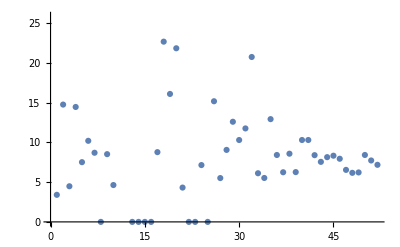

```mathematica
ListPlot[fw]
```

```mathematica
ROI2[ch_]:=Module[{j=ch,
t,
i,
k,l,v},
{ v={x[[j]]};
i=0;
While[i<10,If[x[[j-i]][[2]]>=x[[j-i-1]][[2]],v=AppendTo[v,x[[j-i-1]]],Break[]];i++];v,

v={x[[j]]};
i=0;
While[i<10,If[x[[j+i]][[2]]>=x[[j+i+1]][[2]],v=AppendTo[v,x[[j+i+1]]],Break[]];i++];v}]
```

```mathematica
ROI2[1143]
```

{{{1143,168},{1142,157}},{{1143,168},{1144,132},{1145,121},{1146,105}}}

```mathematica
ROI3[1143]
```

ROI3[1143]

```mathematica
NPA/@β2[[;;,1]]
```

{14293.,1966.,3357.,48.,1844.,678.,3352.,67.,126.,5430.,347.,163.,11905.5,20341.5,28.,24.,182.,240.,29.,134.,16055.,33,10491.,466.,16.5,57.5,1553.,45.,32.,186.5,92.,18,830.,3523.,36.5,114.,1281.,232.,816.,8,8,179,431.5,132.,130.5,27.5,445.,2716,337.5,10.5,-28.,13.5}

```mathematica
Show[ListPlot[x,PlotTheme->"Default",GridLines->Full,ImageSize->700,Axes->True,PlotRange->Full,Joined->True,InterpolationOrder->1,Mesh->Full],ListPlot[bb,PlotStyle->Red,PlotRange->All]]
```

-Graphics-

```mathematica
h1[ch_]:=RoiFun[ch,FirstPosition[ROI[ch],Nearest[#,(x[[ch]][[2]])/2]&/@ROI[ch][[;;,;;,2]]/.{u_ ...}->u]]
```

```mathematica
RoiFun[ch_,{a_,b_}]:=ROI[ch][[a,b]]
h1[ch_]:=RoiFun[ch,FirstPosition[ROI[ch],Max[Nearest[#,(x[[ch]][[2]])/2]&/@ROI[ch][[;;,;;,2]]/.{u_ ...}->u]][[1;;2]]]
FWHM[ch_]:={h1[ch],f[,ch]}
```

```mathematica
mroi[ch_]:=Cases[ROI2[ch][[2,;;]],{_,u_}/;u<=Min[ROI2[ch][[1,;;,2]]]]
mRoi[ch_]:={Min[ROI2[ch][[1,;;,1]]],If[Length[mroi[ch]]!=0,First[Last[mroi[ch]]],Max[ROI2[ch][[2,;;,1]]]]}
Roi[ch_]:={Min[ROI2[ch][[1,;;,1]]],Max[ROI2[ch][[2,;;,1]]]}
cor1Roi[ch_]:={Min[cor1ROI[ch][[1,;;,1]]],Max[cor1ROI[ch][[2,;;,1]]]}
NPA[ch_]:=Total[x[[Roi[ch][[1]];;Roi[ch][[2]]]][[;;,2]]-Table[blin[ch,N@i],{i,Range@@Roi[ch]}]]
```

```mathematica
Roi[#]&/@β2[[;;,1]]
```

{{170,180},{216,224},{224,231},{244,249},{252,261},{261,269},{541,553},{599,602},{654,658},{705,718},{755,764},{801,809},{859,873},{1026,1040},{1142,1146},{1375,1378},{1406,1413},{1425,1433},{1566,1569},{1696,1705},{1779,1796},{1824,1828},{1934,1947},{1947,1960},{2026,2028},{2106,2114},{2249,2264},{2305,2316},{2332,2336},{2363,2369},{2458,2464},{2622,2625},{2734,2747},{3279,3294},{3324,3328},{3389,3399},{3627,3642},{3756,3767},{4037,4051},{4065,4067},{4065,4067},{4110,4118},{4126,4140},{4426,4432},{4641,4651},{4869,4877},{5069,5081},{5171,5190},{5417,5433},{6464,6472},{6471,6482},{7177,7189}}

```mathematica
cor1Roi[1377]
```

Part::partd: Part specification ROI[1377,{0.3,1.8}]⟦2,1;;All,1⟧ is longer than depth of object.

{Integer[],ROI[1377,{0.3,1.8}]⟦2,1;;All,1⟧}

```mathematica
Range@@Roi[175]
```

{170,171,172,173,174,175,176,177,178,179,180}

```mathematica
x[[Roi[175][[1]];;Roi[175][[2]]]][[;;,2]]-Table[blin[175,N@i],{i,Range@@Roi[175]}]
```

{0.,51.,269.,884.,2642.,4416.,3950.,1677.,344.,60.,0.}

```mathematica
Table[blin[175,N@i],{i,Range@@Roi[175]}]
```

{522.,503.,484.,465.,446.,427.,408.,389.,370.,351.,332.}

```mathematica
Cases[ROI[ch][[2,;;]],{_,u_}/;u<=Min[ROI[ch][[1,;;,2]]]]
```

Part::partw: Part 2 of ROI[ch] does not exist.

{}

```mathematica
x[[289;;306]][[;;,2]]
```

{309,329,331,330,310,292,331,329,295,310,352,330,329,295,334,346,302,303}

```mathematica
FWHM1[ch_]:=Max[Nearest[#,(x[[ch]][[2]])/2]&/@ROI[ch]/.{u_ ...}->u]
```

```mathematica
{σ1=0.5,σ2=2.8};
ROI[ch_/;MemberQ[β2[[;;,1]] ,ch]] :=Module[{j=ch,
t,
i,
k,l,v},{v={x[[j]]};
t=0;
i=0;
k=0;

While[i+t+k<30,If[x[[j-i]][[2]]>=x[[j-i-1]][[2]],v=AppendTo[v,x[[j-i-1]]];t++;i++,
l=i;k=0;While[Between[(x[[j-l-k]][[2]])/(x[[j-l-k-1]][[2]]),{σ1,σ2}]&&(!MemberQ[β2[[;;,1]],j-k-l-1])&&k<=8,v=AppendTo[v,x[[j-l-k]]];k++;t++]];If[k>1,i+=k,t++]];v,
v={x[[j]]};
t=0;
i=0;
k=0;
While[i+t+k<30,If[x[[j+i]][[2]]>=x[[j+i+1]][[2]],If[MemberQ[v,x[[j+i+1]],2],Null,v=AppendTo[v,x[[j+i+1]]];t++;i++],
l=i;k=0;While[Between[(x[[j+l+k]][[2]])/(x[[j+l+k+1]][[2]]),{σ1,σ2}]&&(!MemberQ[β2[[;;,1]],j+k+l+1])&&k<=8,v=AppendTo[v,x[[j+l+k]]];k++;t++]];If[k>1,i+=k,t++]];v
}]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit::cvmit will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

InterpolatingFunction::dmval: Input value {4281.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

InterpolatingFunction::dmval: Input value {4281.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4275.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

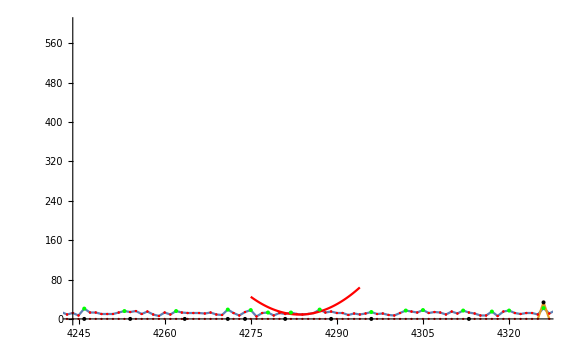

{{4285,10},{4286,12},{4287,19},{4288,13}}

{{4285,503},{4286,504},{4287,499},{4288,322}}

```mathematica
Show[ListLinePlot[{x[[;;,2]],γ2},Epilog->{ Green,PointSize[0.005],Point/@FindPeaks[x[[;;,2]],1],Black,Point/@FindPeaks[γ2,1],RandomColor[],Opacity[0.3],pol/@β2[[;;,1]],Black,Thick,lin[4286]},PlotRange->{Roi[4286]+1{-40,40},{0,600}},GridLines->Full,ImageSize->Large,InterpolationOrder->1,PlotLegends->"Expressions",Mesh->Full,MeshStyle->Red],Plot[f[u,4286],{u,4275,4294},PlotStyle->{Red},PlotRange->Full]]

x[[4285;;4288]]
{{4285,503},{4286,504},{4287,499},{4288,322}}
```

```mathematica
d[n_]:=(x[[;;,2]]-MeanFilter[x[[;;,2]],n])
```

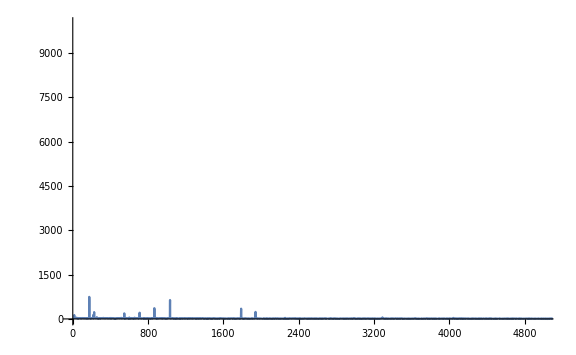

```mathematica
ListLinePlot[d[1],PlotRange->{{0,5000},{0,10000}},GridLines->Full,ImageSize->Large]
```

```mathematica
ff[u_,n_,t_:0]:=({u[[;;,1]],u[[;;,2]]*PeakDetect[u[[;;,2]],n,t]}//Thread)/.{{_,0}->Nothing}
```

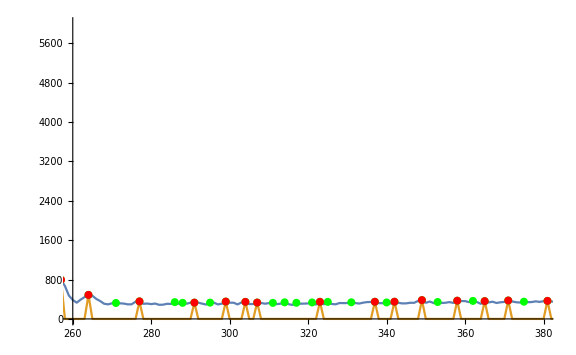

```mathematica
ListLinePlot[{x[[;;,2]],x[[;;,2]]*PeakDetect[x[[;;,2]],1.7]},Epilog->{ Green,PointSize[0.01],Point/@FindPeaks[x[[;;,2]],1],Red,Point/@ff[x,1.7]},PlotRange->{{260,380},{0,6000}},ImageSize->Large]
```

```mathematica
ListPlot[{y,x[[;;,2]]*PeakDetect[x[[;;,2]],1.7,1.1],MeanFilter[x[[;;,2]],2]},Epilog->{ Pink,PointSize[0.005],Point/@FindPeaks[x[[;;,2]],5],Red,Point/@ff[x,1.7],Blue},Filling->Axis,Joined->{False, True},PlotRange->{{850,1000},{0,1300}},ImageSize->700]
```

ListPlot::lpn: {{},{{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},«8182»},{{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.2},{10.,0.2},«8182»}} is not a list of numbers or pairs of numbers.

ListPlot[1]
 |  |  |  |

```mathematica
ListPlot[{y,x[[;;,2]]*PeakDetect[x[[;;,2]],1.7,1.1],g,s},Filling->Axis,Joined->{False, True},PlotRange->{{350,4000},{0,2000}},ImageSize->700]
```

ListPlot::lpn: {{},{{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},«8182»},{},{}} is not a list of numbers or pairs of numbers.

ListPlot[1]
 |  |  |  |

```mathematica
ListPlot[{y,GradientFilter[y,1],s},Joined->True,PlotRange->{{260,380},{0,6000}},ImageSize->700]
```

-Graphics-

```mathematica
GaussianFilter[%,2]
```

-Graphics-

```mathematica
δ=TransformedDistribution[u+b,{u\[Distributed]NormalDistribution[μ,σ],b\[Distributed]RayleighDistribution[γ]}]
```

TransformedDistribution[x1+x2,{x1\[Distributed]NormalDistribution[μ,σ],x2\[Distributed]RayleighDistribution[γ]}]